# CFD Eigenvalue Stability

## BYU GR Research Group

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]]
```

C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks

# A4 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat2List={(*1*)0.2,(*2*)0.63,(*3*)1.05,(*4*)1.14,(*5*)1.62,(*6*)2.25,(*7*)2.73,(*8*)3.39,(*9*)3.93,(*10*)4.38,(*11*)4.80};
yHat1List={(*1*)0.69,(*2*)0.99,(*3*)1.65,(*4*)1.95,(*5*)2.13,(*6*)2.55,(*7*)3.06,(*8*)3.12,(*9*)3.42,(*10*)4.23,(*11*)4.35};
yHat0List={(*1*)0.87,(*2*)1.89,(*3*)2.97,(*4*)4.17,(*5*)4.26};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
ParallelEvaluate[Get["P4_interiorCoeffs.mx"]]
ParallelEvaluate[Get["P4_bdCoeffs0.mx"]]
ParallelEvaluate[Get["P4_bdCoeffs1.mx"]]
ParallelEvaluate[Get["P4_bdCoeffs2.mx"]]
```

{Null,Null,Null,Null}

{Null,Null,Null,Null}

{Null,Null,Null,Null}

«1 more identical outputs»

```mathematica
DistributeDefinitions[yHat0List,yHat1List,yHat2List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,yHat2List,LHS,LHSRows,RHS,RHSRows,k}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsP4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]]},Max[Re[eigs]]},

{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{{{{0.87,0.69,0.2},0.00370991},{{1.89,0.69,0.2},0.0111186},{{2.97,0.69,0.2},0.147291},{{4.17,0.69,0.2},0.493195},{{4.26,0.69,0.2},3.97985}},{{{0.87,0.99,0.2},0.00217669},{{1.89,0.99,0.2},0.00742813},{{2.97,0.99,0.2},0.206115},{{4.17,0.99,0.2},0.391625},{{4.26,0.99,0.2},0.290874}},{{{0.87,1.65,0.2},0.00686492},{{1.89,1.65,0.2},0.00409089},{{2.97,1.65,0.2},0.227377},{{4.17,1.65,0.2},0.192915},{{4.26,1.65,0.2},0.0786411}},{{{0.87,1.95,0.2},0.00944871},{{1.89,1.95,0.2},0.00658153},{{2.97,1.95,0.2},0.00560796},{{4.17,1.95,0.2},0.899116},{{4.26,1.95,0.2},0.0123911}},{{{0.87,2.13,0.2},0.016068},{{1.89,2.13,0.2},0.00445062},{{2.97,2.13,0.2},0.0446824},{{4.17,2.13,0.2},0.474341},{{4.26,2.13,0.2},43.9323}},{{{0.87,2.55,0.2},0.314104},{{1.89,2.55,0.2},0.00274006},{{2.97,2.55,0.2},0.113729},{{4.17,2.55,0.2},0.348797},{{4.26,2.55,0.2},0.338476}},{{{0.87,3.06,0.2},0.19087},{{1.89,3.06,0.2},0.00163145},{{2.97,3.06,0.2},0.159668},{{4.17,3.06,0.2},0.456057},{{4.26,3.06,0.2},0.212747}},{{{0.87,3.12,0.2},0.201018},{{1.89,3.12,0.2},1.49672},{{2.97,3.12,0.2},0.157895},{{4.17,3.12,0.2},1.73073},{{4.26,3.12,0.2},0.206948}},{{{0.87,3.42,0.2},0.737666},{{1.89,3.42,0.2},0.00522346},{{2.97,3.42,0.2},0.159796},{{4.17,3.42,0.2},0.294625},{{4.26,3.42,0.2},0.687213}},{{{0.87,4.23,0.2},1.44782},{{1.89,4.23,0.2},0.0271597},{{2.97,4.23,0.2},0.20518},{{4.17,4.23,0.2},0.24278},{{4.26,4.23,0.2},4.4524}},{{{0.87,4.35,0.2},13.7383},{{1.89,4.35,0.2},0.00722745},{{2.97,4.35,0.2},0.154801},{{4.17,4.35,0.2},0.237776},{{4.26,4.35,0.2},0.00460657}}},{{{{0.87,0.69,0.63},0.00528961},{{1.89,0.69,0.63},0.0104879},{{2.97,0.69,0.63},0.217047},{{4.17,0.69,0.63},2.05808},{{4.26,0.69,0.63},6.35376}},{{{0.87,0.99,0.63},0.00135212},{{1.89,0.99,0.63},0.00883387},{{2.97,0.99,0.63},0.328871},{{4.17,0.99,0.63},10.0069},{{4.26,0.99,0.63},4.1886}},{{{0.87,1.65,0.63},0.00968873},{{1.89,1.65,0.63},0.0075007},{{2.97,1.65,0.63},6.22897},{{4.17,1.65,0.63},8.61912},{{4.26,1.65,0.63},3.2046}},{{{0.87,1.95,0.63},0.0100095},{{1.89,1.95,0.63},0.00968781},{{2.97,1.95,0.63},0.00400526},{{4.17,1.95,0.63},0.00692491},{{4.26,1.95,0.63},0.903768}},{{{0.87,2.13,0.63},0.0101971},{{1.89,2.13,0.63},0.00751622},{{2.97,2.13,0.63},0.0338836},{{4.17,2.13,0.63},0.132361},{{4.26,2.13,0.63},22.5387}},{{{0.87,2.55,0.63},2.46989},{{1.89,2.55,0.63},0.00609304},{{2.97,2.55,0.63},0.140028},{{4.17,2.55,0.63},4.05525},{{4.26,2.55,0.63},5.07272}},{{{0.87,3.06,0.63},0.251784},{{1.89,3.06,0.63},0.0240125},{{2.97,3.06,0.63},0.204303},{{4.17,3.06,0.63},0.0792608},{{4.26,3.06,0.63},2.61584}},{{{0.87,3.12,0.63},0.220135},{{1.89,3.12,0.63},1.54158},{{2.97,3.12,0.63},0.196069},{{4.17,3.12,0.63},0.140052},{{4.26,3.12,0.63},1.64074}},{{{0.87,3.42,0.63},0.132586},{{1.89,3.42,0.63},0.0181495},{{2.97,3.42,0.63},0.192347},{{4.17,3.42,0.63},0.606898},{{4.26,3.42,0.63},9.38398}},{{{0.87,4.23,0.63},2.42877},{{1.89,4.23,0.63},0.523249},{{2.97,4.23,0.63},1.8271},{{4.17,4.23,0.63},3.01878},{{4.26,4.23,0.63},11.6685}},{{{0.87,4.35,0.63},0.124245},{{1.89,4.35,0.63},0.0143602},{{2.97,4.35,0.63},0.215768},{{4.17,4.35,0.63},3.14369},{{4.26,4.35,0.63},5.99487}}},{{{{0.87,0.69,1.05},0.0031788},{{1.89,0.69,1.05},0.0100769},{{2.97,0.69,1.05},0.211461},{{4.17,0.69,1.05},1.91009},{{4.26,0.69,1.05},6.28589}},{{{0.87,0.99,1.05},0.00176513},{{1.89,0.99,1.05},0.00704724},{{2.97,0.99,1.05},0.193548},{{4.17,0.99,1.05},0.388741},{{4.26,0.99,1.05},0.276912}},{{{0.87,1.65,1.05},0.00666026},{{1.89,1.65,1.05},-7.48025×10^-6},{{2.97,1.65,1.05},0.348888},{{4.17,1.65,1.05},0.0119891},{{4.26,1.65,1.05},0.00594917}},{{{0.87,1.95,1.05},0.00943599},{{1.89,1.95,1.05},0.00553514},{{2.97,1.95,1.05},0.234359},{{4.17,1.95,1.05},2.44198},{{4.26,1.95,1.05},0.0078281}},{{{0.87,2.13,1.05},0.0152244},{{1.89,2.13,1.05},0.00139321},{{2.97,2.13,1.05},0.210963},{{4.17,2.13,1.05},11.6435},{{4.26,2.13,1.05},1.45704}},{{{0.87,2.55,1.05},0.432177},{{1.89,2.55,1.05},0.218306},{{2.97,2.55,1.05},0.0155373},{{4.17,2.55,1.05},0.413834},{{4.26,2.55,1.05},0.41209}},{{{0.87,3.06,1.05},0.202176},{{1.89,3.06,1.05},0.672443},{{2.97,3.06,1.05},0.157052},{{4.17,3.06,1.05},0.174371},{{4.26,3.06,1.05},0.178956}},{{{0.87,3.12,1.05},0.205917},{{1.89,3.12,1.05},0.56696},{{2.97,3.12,1.05},0.0971659},{{4.17,3.12,1.05},0.189501},{{4.26,3.12,1.05},0.189124}},{{{0.87,3.42,1.05},0.286899},{{1.89,3.42,1.05},0.237265},{{2.97,3.42,1.05},0.361975},{{4.17,3.42,1.05},0.275862},{{4.26,3.42,1.05},0.285739}},{{{0.87,4.23,1.05},1.63331},{{1.89,4.23,1.05},1.2992},{{2.97,4.23,1.05},0.158148},{{4.17,4.23,1.05},13.4543},{{4.26,4.23,1.05},2.68783}},{{{0.87,4.35,1.05},15.1065},{{1.89,4.35,1.05},94.1173},{{2.97,4.35,1.05},20.5793},{{4.17,4.35,1.05},20.8198},{{4.26,4.35,1.05},17.555}}},{{{{0.87,0.69,1.14},0.00292866},{{1.89,0.69,1.14},0.00978143},{{2.97,0.69,1.14},0.230766},{{4.17,0.69,1.14},2.76925},{{4.26,0.69,1.14},6.99058}},{{{0.87,0.99,1.14},0.00146102},{{1.89,0.99,1.14},0.0069323},{{2.97,0.99,1.14},0.218963},{{4.17,0.99,1.14},0.386103},{{4.26,0.99,1.14},0.311214}},{{{0.87,1.65,1.14},0.00667723},{{1.89,1.65,1.14},-0.0000116672},{{2.97,1.65,1.14},0.303635},{{4.17,1.65,1.14},0.0126504},{{4.26,1.65,1.14},0.00633744}},{{{0.87,1.95,1.14},0.00948553},{{1.89,1.95,1.14},0.00563738},{{2.97,1.95,1.14},0.229244},{{4.17,1.95,1.14},2.36981},{{4.26,1.95,1.14},0.00757969}},{{{0.87,2.13,1.14},0.0139563},{{1.89,2.13,1.14},0.00208916},{{2.97,2.13,1.14},0.212225},{{4.17,2.13,1.14},8.18153},{{4.26,2.13,1.14},1.12575}},{{{0.87,2.55,1.14},0.665451},{{1.89,2.55,1.14},0.113261},{{2.97,2.55,1.14},0.107623},{{4.17,2.55,1.14},0.616171},{{4.26,2.55,1.14},0.622048}},{{{0.87,3.06,1.14},0.215665},{{1.89,3.06,1.14},0.643364},{{2.97,3.06,1.14},0.18563},{{4.17,3.06,1.14},0.181171},{{4.26,3.06,1.14},0.190854}},{{{0.87,3.12,1.14},0.210926},{{1.89,3.12,1.14},0.566704},{{2.97,3.12,1.14},0.148039},{{4.17,3.12,1.14},0.185982},{{4.26,3.12,1.14},0.1909}},{{{0.87,3.42,1.14},0.233012},{{1.89,3.42,1.14},0.250966},{{2.97,3.42,1.14},0.491353},{{4.17,3.42,1.14},0.229026},{{4.26,3.42,1.14},0.233349}},{{{0.87,4.23,1.14},1.84188},{{1.89,4.23,1.14},1.26417},{{2.97,4.23,1.14},0.19305},{{4.17,4.23,1.14},4.67628},{{4.26,4.23,1.14},2.44637}},{{{0.87,4.35,1.14},4.28146},{{1.89,4.35,1.14},28.1733},{{2.97,4.35,1.14},0.524767},{{4.17,4.35,1.14},5.67137},{{4.26,4.35,1.14},4.85808}}},{{{{0.87,0.69,1.62},0.00808822},{{1.89,0.69,1.62},0.0083357},{{2.97,0.69,1.62},10.062},{{4.17,0.69,1.62},1.49861},{{4.26,0.69,1.62},48.3294}},{{{0.87,0.99,1.62},0.100829},{{1.89,0.99,1.62},0.00893766},{{2.97,0.99,1.62},12.3495},{{4.17,0.99,1.62},0.00729812},{{4.26,0.99,1.62},0.00243358}},{{{0.87,1.65,1.62},0.00511377},{{1.89,1.65,1.62},0.00375924},{{2.97,1.65,1.62},3.93954},{{4.17,1.65,1.62},2.833},{{4.26,1.65,1.62},0.17256}},{{{0.87,1.95,1.62},0.0132883},{{1.89,1.95,1.62},0.00542204},{{2.97,1.95,1.62},16.1769},{{4.17,1.95,1.62},0.00806506},{{4.26,1.95,1.62},0.00534994}},{{{0.87,2.13,1.62},0.00806977},{{1.89,2.13,1.62},0.00183651},{{2.97,2.13,1.62},25.4533},{{4.17,2.13,1.62},0.00748614},{{4.26,2.13,1.62},0.00511338}},{{{0.87,2.55,1.62},0.00460939},{{1.89,2.55,1.62},0.00318002},{{2.97,2.55,1.62},18.2554},{{4.17,2.55,1.62},0.00565308},{{4.26,2.55,1.62},0.00433841}},{{{0.87,3.06,1.62},1.86129},{{1.89,3.06,1.62},7.12674},{{2.97,3.06,1.62},31.6869},{{4.17,3.06,1.62},0.197993},{{4.26,3.06,1.62},0.433279}},{{{0.87,3.12,1.62},0.252028},{{1.89,3.12,1.62},0.328499},{{2.97,3.12,1.62},377.071},{{4.17,3.12,1.62},0.139393},{{4.26,3.12,1.62},0.195923}},{{{0.87,3.42,1.62},0.0573975},{{1.89,3.42,1.62},0.0389747},{{2.97,3.42,1.62},0.669245},{{4.17,3.42,1.62},0.0585761},{{4.26,3.42,1.62},0.0539869}},{{{0.87,4.23,1.62},3.9632},{{1.89,4.23,1.62},8.2341},{{2.97,4.23,1.62},17.7796},{{4.17,4.23,1.62},0.0494013},{{4.26,4.23,1.62},0.966895}},{{{0.87,4.35,1.62},0.0893272},{{1.89,4.35,1.62},0.104455},{{2.97,4.35,1.62},8.45433},{{4.17,4.35,1.62},0.0506288},{{4.26,4.35,1.62},0.0611935}}},{{{{0.87,0.69,2.25},0.00538717},{{1.89,0.69,2.25},0.00809026},{{2.97,0.69,2.25},0.0797585},{{4.17,0.69,2.25},0.189605},{{4.26,0.69,2.25},4.51634}},{{{0.87,0.99,2.25},0.00383564},{{1.89,0.99,2.25},0.00683288},{{2.97,0.99,2.25},0.0537653},{{4.17,0.99,2.25},0.0181042},{{4.26,0.99,2.25},0.0189296}},{{{0.87,1.65,2.25},0.00676432},{{1.89,1.65,2.25},0.00280836},{{2.97,1.65,2.25},0.293336},{{4.17,1.65,2.25},0.00891902},{{4.26,1.65,2.25},0.00593718}},{{{0.87,1.95,2.25},0.00825216},{{1.89,1.95,2.25},0.00520441},{{2.97,1.95,2.25},0.125224},{{4.17,1.95,2.25},2.31907},{{4.26,1.95,2.25},0.00658611}},{{{0.87,2.13,2.25},0.0125555},{{1.89,2.13,2.25},0.00395592},{{2.97,2.13,2.25},0.0874447},{{4.17,2.13,2.25},13.5383},{{4.26,2.13,2.25},1.68489}},{{{0.87,2.55,2.25},0.00882078},{{1.89,2.55,2.25},0.00874212},{{2.97,2.55,2.25},1.80059},{{4.17,2.55,2.25},0.0102211},{{4.26,2.55,2.25},0.00705923}},{{{0.87,3.06,2.25},0.0976562},{{1.89,3.06,2.25},0.612043},{{2.97,3.06,2.25},0.0116587},{{4.17,3.06,2.25},0.114364},{{4.26,3.06,2.25},0.0907147}},{{{0.87,3.12,2.25},0.13918},{{1.89,3.12,2.25},0.532782},{{2.97,3.12,2.25},0.00429893},{{4.17,3.12,2.25},0.160218},{{4.26,3.12,2.25},0.138023}},{{{0.87,3.42,2.25},4.37868},{{1.89,3.42,2.25},0.205378},{{2.97,3.42,2.25},0.213501},{{4.17,3.42,2.25},2.44038},{{4.26,3.42,2.25},6.62526}},{{{0.87,4.23,2.25},0.572313},{{1.89,4.23,2.25},1.62565},{{2.97,4.23,2.25},0.0367535},{{4.17,4.23,2.25},10.6389},{{4.26,4.23,2.25},3.77308}},{{{0.87,4.35,2.25},2.52645},{{1.89,4.35,2.25},13.8323},{{2.97,4.35,2.25},0.848035},{{4.17,4.35,2.25},9.73167},{{4.26,4.35,2.25},5.22681}}},{{{{0.87,0.69,2.73},0.272979},{{1.89,0.69,2.73},0.00854035},{{2.97,0.69,2.73},0.356467},{{4.17,0.69,2.73},0.00117963},{{4.26,0.69,2.73},12.8821}},{{{0.87,0.99,2.73},0.414366},{{1.89,0.99,2.73},1.91333},{{2.97,0.99,2.73},0.311103},{{4.17,0.99,2.73},0.0618801},{{4.26,0.99,2.73},0.131151}},{{{0.87,1.65,2.73},0.452566},{{1.89,1.65,2.73},0.00704971},{{2.97,1.65,2.73},10.8228},{{4.17,1.65,2.73},33.1177},{{4.26,1.65,2.73},2.33019}},{{{0.87,1.95,2.73},9.36496},{{1.89,1.95,2.73},4.55214},{{2.97,1.95,2.73},-0.000021273},{{4.17,1.95,2.73},0.00398171},{{4.26,1.95,2.73},0.00201736}},{{{0.87,2.13,2.73},0.0038189},{{1.89,2.13,2.73},0.021817},{{2.97,2.13,2.73},0.00110258},{{4.17,2.13,2.73},0.00445256},{{4.26,2.13,2.73},0.00292912}},{{{0.87,2.55,2.73},0.0931198},{{1.89,2.55,2.73},0.00273298},{{2.97,2.55,2.73},0.0908699},{{4.17,2.55,2.73},0.192719},{{4.26,2.55,2.73},0.140445}},{{{0.87,3.06,2.73},0.711736},{{1.89,3.06,2.73},2.83207},{{2.97,3.06,2.73},0.135668},{{4.17,3.06,2.73},0.118116},{{4.26,3.06,2.73},0.145416}},{{{0.87,3.12,2.73},0.14828},{{1.89,3.12,2.73},0.481423},{{2.97,3.12,2.73},0.142818},{{4.17,3.12,2.73},0.125254},{{4.26,3.12,2.73},0.129215}},{{{0.87,3.42,2.73},0.149978},{{1.89,3.42,2.73},0.0204819},{{2.97,3.42,2.73},0.154719},{{4.17,3.42,2.73},0.192529},{{4.26,3.42,2.73},0.18022}},{{{0.87,4.23,2.73},5.70633},{{1.89,4.23,2.73},6.25461},{{2.97,4.23,2.73},0.355001},{{4.17,4.23,2.73},0.186498},{{4.26,4.23,2.73},1.2081}},{{{0.87,4.35,2.73},0.244215},{{1.89,4.35,2.73},0.0874326},{{2.97,4.35,2.73},0.164701},{{4.17,4.35,2.73},0.174396},{{4.26,4.35,2.73},0.241268}}},{{{{0.87,0.69,3.39},0.185565},{{1.89,0.69,3.39},0.0434107},{{2.97,0.69,3.39},0.221914},{{4.17,0.69,3.39},1.79307},{{4.26,0.69,3.39},5.24151}},{{{0.87,0.99,3.39},0.124441},{{1.89,0.99,3.39},0.0879812},{{2.97,0.99,3.39},0.203841},{{4.17,0.99,3.39},0.214309},{{4.26,0.99,3.39},0.222553}},{{{0.87,1.65,3.39},0.143027},{{1.89,1.65,3.39},6.85878},{{2.97,1.65,3.39},0.364192},{{4.17,1.65,3.39},0.0411373},{{4.26,1.65,3.39},0.0750448}},{{{0.87,1.95,3.39},0.0845351},{{1.89,1.95,3.39},0.0668467},{{2.97,1.95,3.39},0.334627},{{4.17,1.95,3.39},2.1616},{{4.26,1.95,3.39},0.00873118}},{{{0.87,2.13,3.39},0.00538044},{{1.89,2.13,3.39},0.301905},{{2.97,2.13,3.39},0.33669},{{4.17,2.13,3.39},17.7193},{{4.26,2.13,3.39},2.26703}},{{{0.87,2.55,3.39},0.276206},{{1.89,2.55,3.39},190.399},{{2.97,2.55,3.39},0.00553592},{{4.17,2.55,3.39},0.284978},{{4.26,2.55,3.39},0.27616}},{{{0.87,3.06,3.39},0.206188},{{1.89,3.06,3.39},2.23513},{{2.97,3.06,3.39},0.272208},{{4.17,3.06,3.39},0.1382},{{4.26,3.06,3.39},0.1659}},{{{0.87,3.12,3.39},0.190326},{{1.89,3.12,3.39},0.392282},{{2.97,3.12,3.39},0.0540059},{{4.17,3.12,3.39},0.128379},{{4.26,3.12,3.39},0.152326}},{{{0.87,3.42,3.39},1.71295},{{1.89,3.42,3.39},0.00453752},{{2.97,3.42,3.39},0.155065},{{4.17,3.42,3.39},0.258028},{{4.26,3.42,3.39},0.487256}},{{{0.87,4.23,3.39},1.4162},{{1.89,4.23,3.39},1.86862},{{2.97,4.23,3.39},0.155585},{{4.17,4.23,3.39},139.974},{{4.26,4.23,3.39},3.04985}},{{{0.87,4.35,3.39},0.381245},{{1.89,4.35,3.39},0.046799},{{2.97,4.35,3.39},0.226251},{{4.17,4.35,3.39},46.3296},{{4.26,4.35,3.39},4.3206}}},{{{{0.87,0.69,3.93},0.16438},{{1.89,0.69,3.93},0.976253},{{2.97,0.69,3.93},0.284144},{{4.17,0.69,3.93},0.0518243},{{4.26,0.69,3.93},-0.00006365}},{{{0.87,0.99,3.93},0.175385},{{1.89,0.99,3.93},0.157766},{{2.97,0.99,3.93},0.246085},{{4.17,0.99,3.93},0.282333},{{4.26,0.99,3.93},0.265698}},{{{0.87,1.65,3.93},0.191571},{{1.89,1.65,3.93},-0.0000128871},{{2.97,1.65,3.93},2.36528},{{4.17,1.65,3.93},4.43016},{{4.26,1.65,3.93},0.440088}},{{{0.87,1.95,3.93},0.250062},{{1.89,1.95,3.93},0.178872},{{2.97,1.95,3.93},0.000136771},{{4.17,1.95,3.93},0.00326061},{{4.26,1.95,3.93},10.03}},{{{0.87,2.13,3.93},0.0405131},{{1.89,2.13,3.93},-7.8543×10^-6},{{2.97,2.13,3.93},-5.73943×10^-6},{{4.17,2.13,3.93},-8.25917×10^-6},{{4.26,2.13,3.93},-8.45923×10^-6}},{{{0.87,2.55,3.93},0.152366},{{1.89,2.55,3.93},-0.0000182401},{{2.97,2.55,3.93},0.0591952},{{4.17,2.55,3.93},0.266339},{{4.26,2.55,3.93},0.179844}},{{{0.87,3.06,3.93},0.2757},{{1.89,3.06,3.93},0.035064},{{2.97,3.06,3.93},0.0852472},{{4.17,3.06,3.93},0.25289},{{4.26,3.06,3.93},0.801586}},{{{0.87,3.12,3.93},0.384087},{{1.89,3.12,3.93},1.31977},{{2.97,3.12,3.93},0.103653},{{4.17,3.12,3.93},0.100739},{{4.26,3.12,3.93},1.88775}},{{{0.87,3.42,3.93},0.0561015},{{1.89,3.42,3.93},0.00402688},{{2.97,3.42,3.93},0.136451},{{4.17,3.42,3.93},0.157722},{{4.26,3.42,3.93},0.104023}},{{{0.87,4.23,3.93},0.501966},{{1.89,4.23,3.93},1.3308},{{2.97,4.23,3.93},0.325929},{{4.17,4.23,3.93},0.237228},{{4.26,4.23,3.93},0.538297}},{{{0.87,4.35,3.93},0.0826259},{{1.89,4.35,3.93},0.00605262},{{2.97,4.35,3.93},0.12787},{{4.17,4.35,3.93},0.237324},{{4.26,4.35,3.93},0.213892}}},{{{{0.87,0.69,4.38},19.4829},{{1.89,0.69,4.38},0.0137234},{{2.97,0.69,4.38},3.44649},{{4.17,0.69,4.38},51.2156},{{4.26,0.69,4.38},19.9282}},{{{0.87,0.99,4.38},9.59125},{{1.89,0.99,4.38},2.70724},{{2.97,0.99,4.38},6.70393},{{4.17,0.99,4.38},91.6013},{{4.26,0.99,4.38},26.1299}},{{{0.87,1.65,4.38},7.47501},{{1.89,1.65,4.38},0.00290672},{{2.97,1.65,4.38},4.05599},{{4.17,1.65,4.38},1.06629},{{4.26,1.65,4.38},0.116651}},{{{0.87,1.95,4.38},1.40773},{{1.89,1.95,4.38},1.6687},{{2.97,1.95,4.38},6.02939},{{4.17,1.95,4.38},0.00442665},{{4.26,1.95,4.38},0.00515402}},{{{0.87,2.13,4.38},0.00361398},{{1.89,2.13,4.38},0.00247956},{{2.97,2.13,4.38},0.00192426},{{4.17,2.13,4.38},0.00286713},{{4.26,2.13,4.38},0.00281728}},{{{0.87,2.55,4.38},4.79507},{{1.89,2.55,4.38},0.00282222},{{2.97,2.55,4.38},0.0491547},{{4.17,2.55,4.38},0.000941252},{{4.26,2.55,4.38},0.00262603}},{{{0.87,3.06,4.38},3.12363},{{1.89,3.06,4.38},1494.16},{{2.97,3.06,4.38},0.00714217},{{4.17,3.06,4.38},0.138906},{{4.26,3.06,4.38},0.0167727}},{{{0.87,3.12,4.38},1.16015},{{1.89,3.12,4.38},0.783758},{{2.97,3.12,4.38},0.0654632},{{4.17,3.12,4.38},0.11825},{{4.26,3.12,4.38},0.114764}},{{{0.87,3.42,4.38},0.00201425},{{1.89,3.42,4.38},0.00930311},{{2.97,3.42,4.38},0.142311},{{4.17,3.42,4.38},0.0970755},{{4.26,3.42,4.38},0.0128125}},{{{0.87,4.23,4.38},3.96411},{{1.89,4.23,4.38},50.9832},{{2.97,4.23,4.38},0.826036},{{4.17,4.23,4.38},0.213016},{{4.26,4.23,4.38},1.18745}},{{{0.87,4.35,4.38},0.0017141},{{1.89,4.35,4.38},0.00622176},{{2.97,4.35,4.38},0.137445},{{4.17,4.35,4.38},0.221518},{{4.26,4.35,4.38},0.0289969}}},{{{{0.87,0.69,4.8},-2.37723×10^-6},{{1.89,0.69,4.8},0.732563},{{2.97,0.69,4.8},0.0593525},{{4.17,0.69,4.8},-0.000153683},{{4.26,0.69,4.8},0.483824}},{{{0.87,0.99,4.8},-6.60917×10^-7},{{1.89,0.99,4.8},0.000228918},{{2.97,0.99,4.8},0.00328944},{{4.17,0.99,4.8},0.0409775},{{4.26,0.99,4.8},0.0104245}},{{{0.87,1.65,4.8},0.000176138},{{1.89,1.65,4.8},0.00137503},{{2.97,1.65,4.8},34.9904},{{4.17,1.65,4.8},5.13783},{{4.26,1.65,4.8},0.287402}},{{{0.87,1.95,4.8},0.00216116},{{1.89,1.95,4.8},0.000456001},{{2.97,1.95,4.8},-0.0000472476},{{4.17,1.95,4.8},0.0021725},{{4.26,1.95,4.8},2.74479}},{{{0.87,2.13,4.8},0.17486},{{1.89,2.13,4.8},0.000965358},{{2.97,2.13,4.8},0.000164699},{{4.17,2.13,4.8},-0.0000287247},{{4.26,2.13,4.8},-0.0000390485}},{{{0.87,2.55,4.8},-3.35931×10^-6},{{1.89,2.55,4.8},0.000805607},{{2.97,2.55,4.8},0.0606703},{{4.17,2.55,4.8},0.116987},{{4.26,2.55,4.8},0.000260348}},{{{0.87,3.06,4.8},0.0147845},{{1.89,3.06,4.8},0.229701},{{2.97,3.06,4.8},0.0469148},{{4.17,3.06,4.8},0.146249},{{4.26,3.06,4.8},0.589479}},{{{0.87,3.12,4.8},0.137237},{{1.89,3.12,4.8},1.40901},{{2.97,3.12,4.8},0.0927344},{{4.17,3.12,4.8},0.100954},{{4.26,3.12,4.8},0.112294}},{{{0.87,3.42,4.8},-0.0000245104},{{1.89,3.42,4.8},0.00592471},{{2.97,3.42,4.8},0.135526},{{4.17,3.42,4.8},0.117026},{{4.26,3.42,4.8},0.0132669}},{{{0.87,4.23,4.8},0.349116},{{1.89,4.23,4.8},0.885402},{{2.97,4.23,4.8},0.293124},{{4.17,4.23,4.8},0.205571},{{4.26,4.23,4.8},0.301544}},{{{0.87,4.35,4.8},-0.0000123981},{{1.89,4.35,4.8},0.00616451},{{2.97,4.35,4.8},0.124366},{{4.17,4.35,4.8},0.209675},{{4.26,4.35,4.8},0.0989907}}}}

```mathematica
DumpSave["A4_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["A4_MaxReList.mx"]
```

```mathematica
maxReList//TableForm
Dimensions@maxrelist
trimmed=Flatten[maxReList,2];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

## Run Eigenvalue Spectra on All Operators

```mathematica
eigSpectraList=ParallelTable[
Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];

(*Define ŷ values*)
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsP4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]],

{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
Print["Kernel ",$KernelID," working on ",m];

(*Define ŷ values*)
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsP4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]],

{m,1,Length@stable}]
```

# B4 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=4;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==3&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==5),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==1&&j==7),a17Bar,
If[(i==1&&j==8),a18Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,
If[(i==2&&j==7),a27Bar,
If[(i==2&&j==8),a28Bar,

If[(i==3&&j==1),a31Bar,
If[(i==3&&j==2),a32Bar,
If[(i==3&&j==3),a33Bar,
If[(i==3&&j==4),a34Bar,
If[(i==3&&j==5),a35Bar,
If[(i==3&&j==6),a36Bar,
If[(i==3&&j==7),a37Bar,
If[(i==3&&j==8),a38Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k&&j==k-7),-a07,
If[(i==k&&j==k-8),-a08,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-1&&j==k-7),-a17,
If[(i==k-1&&j==k-8),-a18,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,
If[(i==k-2&&j==k-7),-a27,
If[(i==k-2&&j==k-8),-a28,
If[(i==k-3&&j==k),-a30,
If[(i==k-3&&j==k-1),-a31,
If[(i==k-3&&j==k-2),-a32,
If[(i==k-3&&j==k-3),-a33,
If[(i==k-3&&j==k-4),-a34,
If[(i==k-3&&j==k-5),-a35,
If[(i==k-3&&j==k-6),-a36,
If[(i==k-3&&j==k-7),-a37,
If[(i==k-3&&j==k-8),-a38,


If[i-4==j,-a4,
If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
If[i+4==j,a4,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat3List={(*1*)2.97,(*2*)4.38};
yHat2List={(*1*)2.07,(*2*)2.40,(*3*)2.85,(*4*)3.90,(*5*)4.14,(*6*)4.41};
yHat1List={(*1*)1.80,(*2*)2.85,(*3*)3.12,(*4*)3.51,(*5*)4.14,(*6*)4.71};
yHat0List={(*1*)1.10,(*2*)2.80,(*3*)3.10,(*4*)4.10};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
ParallelEvaluate[Get["B4_interiorCoeffs.mx"]]
ParallelEvaluate[Get["B4_bdCoeffs0.mx"]]
ParallelEvaluate[Get["B4_bdCoeffs1.mx"]]
ParallelEvaluate[Get["B4_bdCoeffs2.mx"]]
ParallelEvaluate[Get["B4_bdCoeffs3.mx"]]
```

{Null,Null,Null,Null}

{Null,Null,Null,Null}

{Null,Null,Null,Null}

«2 more identical outputs»

```mathematica
DistributeDefinitions[yHat0List,yHat1List,yHat2List,yHat3List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,yHat2List,yHat3List,LHS,LHSRows,RHS,RHSRows,k}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{ww,xx,yy,zz}];*)

(*Define ŷ values*)
yHat3=yHat3List[[ww]];
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsB4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]],yHat3List[[ww]]},Max[Re[eigs]]},

{ww,1,Length@yHat3List},{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{{{{{1.1,1.8,2.07,2.97},0.0659447},{{2.8,1.8,2.07,2.97},0.000113837},{{3.1,1.8,2.07,2.97},0.0981299},{{4.1,1.8,2.07,2.97},0.068744}},{{{1.1,2.85,2.07,2.97},5.0144×10^-6},{{2.8,2.85,2.07,2.97},0.0607694},{{3.1,2.85,2.07,2.97},5.65569},{{4.1,2.85,2.07,2.97},0.0199579}},{{{1.1,3.12,2.07,2.97},0.0199395},{{2.8,3.12,2.07,2.97},0.00019609},{{3.1,3.12,2.07,2.97},0.0506722},{{4.1,3.12,2.07,2.97},0.0000722286}},{{{1.1,3.51,2.07,2.97},0.0293151},{{2.8,3.51,2.07,2.97},0.00761975},{{3.1,3.51,2.07,2.97},0.0815296},{{4.1,3.51,2.07,2.97},3.88108}},{{{1.1,4.14,2.07,2.97},0.0000338086},{{2.8,4.14,2.07,2.97},0.0000146206},{{3.1,4.14,2.07,2.97},1.557},{{4.1,4.14,2.07,2.97},0.0000292393}},{{{1.1,4.71,2.07,2.97},0.0264843},{{2.8,4.71,2.07,2.97},0.0000791115},{{3.1,4.71,2.07,2.97},0.0480387},{{4.1,4.71,2.07,2.97},0.00563965}}},{{{{1.1,1.8,2.4,2.97},0.00176463},{{2.8,1.8,2.4,2.97},1.51122},{{3.1,1.8,2.4,2.97},0.00018441},{{4.1,1.8,2.4,2.97},0.963641}},{{{1.1,2.85,2.4,2.97},0.000793573},{{2.8,2.85,2.4,2.97},0.194989},{{3.1,2.85,2.4,2.97},0.120275},{{4.1,2.85,2.4,2.97},0.099951}},{{{1.1,3.12,2.4,2.97},0.000216431},{{2.8,3.12,2.4,2.97},0.000518907},{{3.1,3.12,2.4,2.97},0.0463921},{{4.1,3.12,2.4,2.97},0.000352104}},{{{1.1,3.51,2.4,2.97},0.00643556},{{2.8,3.51,2.4,2.97},3.60811},{{3.1,3.51,2.4,2.97},0.141789},{{4.1,3.51,2.4,2.97},3.00418}},{{{1.1,4.14,2.4,2.97},0.000594915},{{2.8,4.14,2.4,2.97},0.252655},{{3.1,4.14,2.4,2.97},0.0706795},{{4.1,4.14,2.4,2.97},0.142202}},{{{1.1,4.71,2.4,2.97},0.00023156},{{2.8,4.71,2.4,2.97},0.00339962},{{3.1,4.71,2.4,2.97},0.0383563},{{4.1,4.71,2.4,2.97},0.00657024}}},{{{{1.1,1.8,2.85,2.97},2.48736},{{2.8,1.8,2.85,2.97},12.5138},{{3.1,1.8,2.85,2.97},4.94666},{{4.1,1.8,2.85,2.97},21.9674}},{{{1.1,2.85,2.85,2.97},0.000904441},{{2.8,2.85,2.85,2.97},0.181042},{{3.1,2.85,2.85,2.97},0.137253},{{4.1,2.85,2.85,2.97},0.0879459}},{{{1.1,3.12,2.85,2.97},0.00782996},{{2.8,3.12,2.85,2.97},0.000360535},{{3.1,3.12,2.85,2.97},0.0459715},{{4.1,3.12,2.85,2.97},0.000193534}},{{{1.1,3.51,2.85,2.97},1.01058},{{2.8,3.51,2.85,2.97},0.00716512},{{3.1,3.51,2.85,2.97},0.869533},{{4.1,3.51,2.85,2.97},0.00617294}},{{{1.1,4.14,2.85,2.97},0.00058726},{{2.8,4.14,2.85,2.97},0.253253},{{3.1,4.14,2.85,2.97},0.0770385},{{4.1,4.14,2.85,2.97},0.138648}},{{{1.1,4.71,2.85,2.97},0.000157337},{{2.8,4.71,2.85,2.97},0.000867552},{{3.1,4.71,2.85,2.97},0.0360244},{{4.1,4.71,2.85,2.97},0.000610395}}},{{{{1.1,1.8,3.9,2.97},3.49328},{{2.8,1.8,3.9,2.97},2.99998},{{3.1,1.8,3.9,2.97},3.31984},{{4.1,1.8,3.9,2.97},3.04841}},{{{1.1,2.85,3.9,2.97},0.000245329},{{2.8,2.85,3.9,2.97},0.214919},{{3.1,2.85,3.9,2.97},0.087938},{{4.1,2.85,3.9,2.97},0.121952}},{{{1.1,3.12,3.9,2.97},0.0000591141},{{2.8,3.12,3.9,2.97},0.000755733},{{3.1,3.12,3.9,2.97},0.385426},{{4.1,3.12,3.9,2.97},0.000578632}},{{{1.1,3.51,3.9,2.97},8.37042},{{2.8,3.51,3.9,2.97},5.89387},{{3.1,3.51,3.9,2.97},20.3507},{{4.1,3.51,3.9,2.97},6.86841}},{{{1.1,4.14,3.9,2.97},0.460587},{{2.8,4.14,3.9,2.97},0.821227},{{3.1,4.14,3.9,2.97},0.613683},{{4.1,4.14,3.9,2.97},0.741325}},{{{1.1,4.71,3.9,2.97},0.000105602},{{2.8,4.71,3.9,2.97},0.00790938},{{3.1,4.71,3.9,2.97},0.598288},{{4.1,4.71,3.9,2.97},0.243638}}},{{{{1.1,1.8,4.14,2.97},4.09377},{{2.8,1.8,4.14,2.97},249.902},{{3.1,1.8,4.14,2.97},6.39482},{{4.1,1.8,4.14,2.97},47.2452}},{{{1.1,2.85,4.14,2.97},0.000922857},{{2.8,2.85,4.14,2.97},0.19609},{{3.1,2.85,4.14,2.97},0.116752},{{4.1,2.85,4.14,2.97},0.102782}},{{{1.1,3.12,4.14,2.97},0.000127549},{{2.8,3.12,4.14,2.97},0.000424793},{{3.1,3.12,4.14,2.97},0.0428565},{{4.1,3.12,4.14,2.97},0.000251057}},{{{1.1,3.51,4.14,2.97},1.61982},{{2.8,3.51,4.14,2.97},0.697026},{{3.1,3.51,4.14,2.97},1.48315},{{4.1,3.51,4.14,2.97},0.647284}},{{{1.1,4.14,4.14,2.97},0.000340115},{{2.8,4.14,4.14,2.97},0.273039},{{3.1,4.14,4.14,2.97},0.0495167},{{4.1,4.14,4.14,2.97},0.160784}},{{{1.1,4.71,4.14,2.97},0.000111183},{{2.8,4.71,4.14,2.97},0.00140848},{{3.1,4.71,4.14,2.97},0.027445},{{4.1,4.71,4.14,2.97},0.00119735}}},{{{{1.1,1.8,4.41,2.97},0.557919},{{2.8,1.8,4.41,2.97},0.264801},{{3.1,1.8,4.41,2.97},0.680993},{{4.1,1.8,4.41,2.97},0.215004}},{{{1.1,2.85,4.41,2.97},0.718586},{{2.8,2.85,4.41,2.97},0.154305},{{3.1,2.85,4.41,2.97},0.178985},{{4.1,2.85,4.41,2.97},0.0803463}},{{{1.1,3.12,4.41,2.97},0.00411186},{{2.8,3.12,4.41,2.97},0.000447458},{{3.1,3.12,4.41,2.97},0.0463056},{{4.1,3.12,4.41,2.97},0.000275567}},{{{1.1,3.51,4.41,2.97},0.216561},{{2.8,3.51,4.41,2.97},0.228115},{{3.1,3.51,4.41,2.97},0.219788},{{4.1,3.51,4.41,2.97},0.236935}},{{{1.1,4.14,4.41,2.97},8.70001},{{2.8,4.14,4.41,2.97},0.179555},{{3.1,4.14,4.41,2.97},0.164334},{{4.1,4.14,4.41,2.97},0.107666}},{{{1.1,4.71,4.41,2.97},0.000215855},{{2.8,4.71,4.41,2.97},0.00348719},{{3.1,4.71,4.41,2.97},0.0352399},{{4.1,4.71,4.41,2.97},0.00659194}}}},{{{{{1.1,1.8,2.07,4.38},0.0669338},{{2.8,1.8,2.07,4.38},0.0000987177},{{3.1,1.8,2.07,4.38},0.099163},{{4.1,1.8,2.07,4.38},0.0738579}},{{{1.1,2.85,2.07,4.38},0.0000105935},{{2.8,2.85,2.07,4.38},0.0617733},{{3.1,2.85,2.07,4.38},5.67248},{{4.1,2.85,2.07,4.38},0.0208739}},{{{1.1,3.12,2.07,4.38},0.0192278},{{2.8,3.12,2.07,4.38},0.000197927},{{3.1,3.12,2.07,4.38},0.0503725},{{4.1,3.12,2.07,4.38},0.0000737754}},{{{1.1,3.51,2.07,4.38},0.0297326},{{2.8,3.51,2.07,4.38},0.00651974},{{3.1,3.51,2.07,4.38},0.0822473},{{4.1,3.51,2.07,4.38},3.14786}},{{{1.1,4.14,2.07,4.38},0.0000249653},{{2.8,4.14,2.07,4.38},9.50548×10^-6},{{3.1,4.14,2.07,4.38},1.78849},{{4.1,4.14,2.07,4.38},0.000025192}},{{{1.1,4.71,2.07,4.38},0.0242546},{{2.8,4.71,2.07,4.38},0.0000924876},{{3.1,4.71,2.07,4.38},0.0465011},{{4.1,4.71,2.07,4.38},0.0000446961}}},{{{{1.1,1.8,2.4,4.38},0.00107183},{{2.8,1.8,2.4,4.38},2.39671},{{3.1,1.8,2.4,4.38},0.000125609},{{4.1,1.8,2.4,4.38},1.74513}},{{{1.1,2.85,2.4,4.38},0.000344999},{{2.8,2.85,2.4,4.38},0.204976},{{3.1,2.85,2.4,4.38},0.107976},{{4.1,2.85,2.4,4.38},0.108571}},{{{1.1,3.12,2.4,4.38},0.00011423},{{2.8,3.12,2.4,4.38},0.000648291},{{3.1,3.12,2.4,4.38},0.0442859},{{4.1,3.12,2.4,4.38},0.000459811}},{{{1.1,3.51,2.4,4.38},0.0131978},{{2.8,3.51,2.4,4.38},4.32319},{{3.1,3.51,2.4,4.38},0.000218327},{{4.1,3.51,2.4,4.38},3.38198}},{{{1.1,4.14,2.4,4.38},0.000237869},{{2.8,4.14,2.4,4.38},0.557292},{{3.1,4.14,2.4,4.38},0.0566762},{{4.1,4.14,2.4,4.38},0.1548}},{{{1.1,4.71,2.4,4.38},0.000109236},{{2.8,4.71,2.4,4.38},0.00483025},{{3.1,4.71,2.4,4.38},0.0331488},{{4.1,4.71,2.4,4.38},0.055685}}},{{{{1.1,1.8,2.85,4.38},2.21286},{{2.8,1.8,2.85,4.38},10.6106},{{3.1,1.8,2.85,4.38},4.7325},{{4.1,1.8,2.85,4.38},17.3708}},{{{1.1,2.85,2.85,4.38},0.000704865},{{2.8,2.85,2.85,4.38},0.189261},{{3.1,2.85,2.85,4.38},0.126641},{{4.1,2.85,2.85,4.38},0.0951097}},{{{1.1,3.12,2.85,4.38},0.00473239},{{2.8,3.12,2.85,4.38},0.000378523},{{3.1,3.12,2.85,4.38},0.044474},{{4.1,3.12,2.85,4.38},0.000222062}},{{{1.1,3.51,2.85,4.38},1.52706},{{2.8,3.51,2.85,4.38},0.0834176},{{3.1,3.51,2.85,4.38},1.26982},{{4.1,3.51,2.85,4.38},0.0561269}},{{{1.1,4.14,2.85,4.38},0.000344179},{{2.8,4.14,2.85,4.38},0.612782},{{3.1,4.14,2.85,4.38},0.0635653},{{4.1,4.14,2.85,4.38},0.151585}},{{{1.1,4.71,2.85,4.38},0.000108976},{{2.8,4.71,2.85,4.38},0.00100594},{{3.1,4.71,2.85,4.38},0.0320328},{{4.1,4.71,2.85,4.38},0.000752035}}},{{{{1.1,1.8,3.9,4.38},2.83356},{{2.8,1.8,3.9,4.38},4.5948},{{3.1,1.8,3.9,4.38},3.32991},{{4.1,1.8,3.9,4.38},4.3757}},{{{1.1,2.85,3.9,4.38},1.8256},{{2.8,2.85,3.9,4.38},2.23365},{{3.1,2.85,3.9,4.38},2.04654},{{4.1,2.85,3.9,4.38},2.14689}},{{{1.1,3.12,3.9,4.38},1.5315},{{2.8,3.12,3.9,4.38},0.000712708},{{3.1,3.12,3.9,4.38},2.07841},{{4.1,3.12,3.9,4.38},0.0714166}},{{{1.1,3.51,3.9,4.38},6.09299},{{2.8,3.51,3.9,4.38},6.7496},{{3.1,3.51,3.9,4.38},6.32509},{{4.1,3.51,3.9,4.38},6.71082}},{{{1.1,4.14,3.9,4.38},1.95906},{{2.8,4.14,3.9,4.38},2.86383},{{3.1,4.14,3.9,4.38},2.29707},{{4.1,4.14,3.9,4.38},2.68651}},{{{1.1,4.71,3.9,4.38},1.63423},{{2.8,4.71,3.9,4.38},0.0532061},{{3.1,4.71,3.9,4.38},2.19298},{{4.1,4.71,3.9,4.38},0.779587}}},{{{{1.1,1.8,4.14,4.38},3.35871},{{2.8,1.8,4.14,4.38},44.9868},{{3.1,1.8,4.14,4.38},5.81826},{{4.1,1.8,4.14,4.38},4403.}},{{{1.1,2.85,4.14,4.38},0.000284117},{{2.8,2.85,4.14,4.38},0.207869},{{3.1,2.85,4.14,4.38},0.101734},{{4.1,2.85,4.14,4.38},0.112943}},{{{1.1,3.12,4.14,4.38},0.0000635009},{{2.8,3.12,4.14,4.38},0.000464243},{{3.1,3.12,4.14,4.38},0.453668},{{4.1,3.12,4.14,4.38},0.000337044}},{{{1.1,3.51,4.14,4.38},3.0051},{{2.8,3.51,4.14,4.38},1.01171},{{3.1,3.51,4.14,4.38},2.65402},{{4.1,3.51,4.14,4.38},0.986245}},{{{1.1,4.14,4.14,4.38},0.000219192},{{2.8,4.14,4.14,4.38},2.03398},{{3.1,4.14,4.14,4.38},0.619593},{{4.1,4.14,4.14,4.38},1.45818}},{{{1.1,4.71,4.14,4.38},0.0000856496},{{2.8,4.71,4.14,4.38},0.00176861},{{3.1,4.71,4.14,4.38},0.680263},{{4.1,4.71,4.14,4.38},0.0016824}}},{{{{1.1,1.8,4.41,4.38},0.67728},{{2.8,1.8,4.41,4.38},0.279837},{{3.1,1.8,4.41,4.38},0.905692},{{4.1,1.8,4.41,4.38},0.225934}},{{{1.1,2.85,4.41,4.38},3.33045},{{2.8,2.85,4.41,4.38},0.162716},{{3.1,2.85,4.41,4.38},0.158729},{{4.1,2.85,4.41,4.38},0.0878793}},{{{1.1,3.12,4.41,4.38},0.000121687},{{2.8,3.12,4.41,4.38},0.000513604},{{3.1,3.12,4.41,4.38},0.0442475},{{4.1,3.12,4.41,4.38},0.000363929}},{{{1.1,3.51,4.41,4.38},0.266874},{{2.8,3.51,4.41,4.38},0.257982},{{3.1,3.51,4.41,4.38},0.2654},{{4.1,3.51,4.41,4.38},0.253479}},{{{1.1,4.14,4.41,4.38},7.0487},{{2.8,4.14,4.41,4.38},0.192783},{{3.1,4.14,4.41,4.38},0.288987},{{4.1,4.14,4.41,4.38},0.119292}},{{{1.1,4.71,4.41,4.38},0.000095079},{{2.8,4.71,4.41,4.38},0.00529348},{{3.1,4.71,4.41,4.38},0.0290146},{{4.1,4.71,4.41,4.38},0.0867938}}}}}

```mathematica
DumpSave["B4_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["B4_MaxReList.mx"]
maxReList
```

{{{{{{1.1,1.77,2.07,2.94},0.069282},{{2.8,1.77,2.07,2.94},0.0102496},{{3.1,1.77,2.07,2.94},0.0991029},{{4.1,1.77,2.07,2.94},0.077854}},{{{1.1,2.85,2.07,2.94},0.0000432125},{{2.8,2.85,2.07,2.94},0.0539793},{{3.1,2.85,2.07,2.94},22.1718},{{4.1,2.85,2.07,2.94},0.0232438}},{{{1.1,3.48,2.07,2.94},0.0202968},{{2.8,3.48,2.07,2.94},0.000568977},{{3.1,3.48,2.07,2.94},0.0813532},{{4.1,3.48,2.07,2.94},0.000837856}},{{{1.1,4.14,2.07,2.94},0.0000319195},{{2.8,4.14,2.07,2.94},0.0118403},{{3.1,4.14,2.07,2.94},0.396571},{{4.1,4.14,2.07,2.94},0.00655337}}},{{{{1.1,1.77,2.85,2.94},15.5254},{{2.8,1.77,2.85,2.94},55.4902},{{3.1,1.77,2.85,2.94},12.9102},{{4.1,1.77,2.85,2.94},40.0806}},{{{1.1,2.85,2.85,2.94},0.21893},{{2.8,2.85,2.85,2.94},0.148787},{{3.1,2.85,2.85,2.94},0.18897},{{4.1,2.85,2.85,2.94},0.0742782}},{{{1.1,3.48,2.85,2.94},0.359166},{{2.8,3.48,2.85,2.94},1.00758},{{3.1,3.48,2.85,2.94},0.297548},{{4.1,3.48,2.85,2.94},0.214277}},{{{1.1,4.14,2.85,2.94},0.0108779},{{2.8,4.14,2.85,2.94},0.237209},{{3.1,4.14,2.85,2.94},0.0760478},{{4.1,4.14,2.85,2.94},0.128883}}},{{{{1.1,1.77,3.9,2.94},0.989462},{{2.8,1.77,3.9,2.94},2.55475},{{3.1,1.77,3.9,2.94},13.6205},{{4.1,1.77,3.9,2.94},2.9312}},{{{1.1,2.85,3.9,2.94},0.389326},{{2.8,2.85,3.9,2.94},0.181563},{{3.1,2.85,3.9,2.94},0.121108},{{4.1,2.85,3.9,2.94},0.102817}},{{{1.1,3.48,3.9,2.94},0.477142},{{2.8,3.48,3.9,2.94},2.52963},{{3.1,3.48,3.9,2.94},0.577374},{{4.1,3.48,3.9,2.94},4.72755}},{{{1.1,4.14,3.9,2.94},1.37821},{{2.8,4.14,3.9,2.94},0.519388},{{3.1,4.14,3.9,2.94},0.31295},{{4.1,4.14,3.9,2.94},0.44367}}},{{{{1.1,1.77,4.14,2.94},4.63694},{{2.8,1.77,4.14,2.94},18.1845},{{3.1,1.77,4.14,2.94},13.2829},{{4.1,1.77,4.14,2.94},24.1897}},{{{1.1,2.85,4.14,2.94},0.306118},{{2.8,2.85,4.14,2.94},0.163241},{{3.1,2.85,4.14,2.94},0.161186},{{4.1,2.85,4.14,2.94},0.0866187}},{{{1.1,3.48,4.14,2.94},0.427903},{{2.8,3.48,4.14,2.94},7.55634},{{3.1,3.48,4.14,2.94},0.374701},{{4.1,3.48,4.14,2.94},1.29256}},{{{1.1,4.14,4.14,2.94},0.701879},{{2.8,4.14,4.14,2.94},0.258149},{{3.1,4.14,4.14,2.94},0.0368424},{{4.1,4.14,4.14,2.94},0.149135}}}},{{{{{1.1,1.77,2.07,4.41},0.0703956},{{2.8,1.77,2.07,4.41},0.0128736},{{3.1,1.77,2.07,4.41},0.0999582},{{4.1,1.77,2.07,4.41},0.0809842}},{{{1.1,2.85,2.07,4.41},0.0000318686},{{2.8,2.85,2.07,4.41},0.0545362},{{3.1,2.85,2.07,4.41},25.7494},{{4.1,2.85,2.07,4.41},0.0238922}},{{{1.1,3.48,2.07,4.41},0.0212445},{{2.8,3.48,2.07,4.41},0.000548163},{{3.1,3.48,2.07,4.41},0.0820481},{{4.1,3.48,2.07,4.41},0.000735917}},{{{1.1,4.14,2.07,4.41},0.00103068},{{2.8,4.14,2.07,4.41},0.0132674},{{3.1,4.14,2.07,4.41},0.687309},{{4.1,4.14,2.07,4.41},0.00821918}}},{{{{1.1,1.77,2.85,4.41},2.18928},{{2.8,1.77,2.85,4.41},12.6119},{{3.1,1.77,2.85,4.41},24.3686},{{4.1,1.77,2.85,4.41},15.0491}},{{{1.1,2.85,2.85,4.41},0.292085},{{2.8,2.85,2.85,4.41},0.156526},{{3.1,2.85,2.85,4.41},0.172689},{{4.1,2.85,2.85,4.41},0.0799897}},{{{1.1,3.48,2.85,4.41},0.431607},{{2.8,3.48,2.85,4.41},1.0056},{{3.1,3.48,2.85,4.41},0.348599},{{4.1,3.48,2.85,4.41},0.350537}},{{{1.1,4.14,2.85,4.41},0.00692345},{{2.8,4.14,2.85,4.41},0.65457},{{3.1,4.14,2.85,4.41},0.0571594},{{4.1,4.14,2.85,4.41},0.141441}}},{{{{1.1,1.77,3.9,4.41},6.22575},{{2.8,1.77,3.9,4.41},4.6625},{{3.1,1.77,3.9,4.41},3.38292},{{4.1,1.77,3.9,4.41},4.51491}},{{{1.1,2.85,3.9,4.41},2.86119},{{2.8,2.85,3.9,4.41},2.10449},{{3.1,2.85,3.9,4.41},1.89899},{{4.1,2.85,3.9,4.41},2.00308}},{{{1.1,3.48,3.9,4.41},2.79667},{{2.8,3.48,3.9,4.41},4.91448},{{3.1,3.48,3.9,4.41},1.04284},{{4.1,3.48,3.9,4.41},5.93513}},{{{1.1,4.14,3.9,4.41},78.576},{{2.8,4.14,3.9,4.41},2.90451},{{3.1,4.14,3.9,4.41},2.09008},{{4.1,4.14,3.9,4.41},2.66384}}},{{{{1.1,1.77,4.14,4.41},5.52279},{{2.8,1.77,4.14,4.41},67.8489},{{3.1,1.77,4.14,4.41},15.0727},{{4.1,1.77,4.14,4.41},137.678}},{{{1.1,2.85,4.14,4.41},0.944024},{{2.8,2.85,4.14,4.41},0.175329},{{3.1,2.85,4.14,4.41},0.1365},{{4.1,2.85,4.14,4.41},0.095568}},{{{1.1,3.48,4.14,4.41},1.22433},{{2.8,3.48,4.14,4.41},5.26702},{{3.1,3.48,4.14,4.41},0.482049},{{4.1,3.48,4.14,4.41},2.00791}},{{{1.1,4.14,4.14,4.41},0.349936},{{2.8,4.14,4.14,4.41},2.13219},{{3.1,4.14,4.14,4.41},0.3647},{{4.1,4.14,4.14,4.41},1.43356}}}}}

```mathematica
maxReList//TableForm
Dimensions@maxReList
trimmed=Flatten[maxReList,3];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

1.1 | 1.8 | 2.07 | 2.97
0.0659447 |  |  |  | 2.8 | 1.8 | 2.07 | 2.97
0.000113837 |  |  |  | 3.1 | 1.8 | 2.07 | 2.97
0.0981299 |  |  |  | 4.1 | 1.8 | 2.07 | 2.97
0.068744 |  |  | 
1.1 | 2.85 | 2.07 | 2.97
5.0144×10^-6 |  |  |  | 2.8 | 2.85 | 2.07 | 2.97
0.0607694 |  |  |  | 3.1 | 2.85 | 2.07 | 2.97
5.65569 |  |  |  | 4.1 | 2.85 | 2.07 | 2.97
0.0199579 |  |  | 
1.1 | 3.12 | 2.07 | 2.97
0.0199395 |  |  |  | 2.8 | 3.12 | 2.07 | 2.97
0.00019609 |  |  |  | 3.1 | 3.12 | 2.07 | 2.97
0.0506722 |  |  |  | 4.1 | 3.12 | 2.07 | 2.97
0.0000722286 |  |  | 
1.1 | 3.51 | 2.07 | 2.97
0.0293151 |  |  |  | 2.8 | 3.51 | 2.07 | 2.97
0.00761975 |  |  |  | 3.1 | 3.51 | 2.07 | 2.97
0.0815296 |  |  |  | 4.1 | 3.51 | 2.07 | 2.97
3.88108 |  |  | 
1.1 | 4.14 | 2.07 | 2.97
0.0000338086 |  |  |  | 2.8 | 4.14 | 2.07 | 2.97
0.0000146206 |  |  |  | 3.1 | 4.14 | 2.07 | 2.97
1.557 |  |  |  | 4.1 | 4.14 | 2.07 | 2.97
0.0000292393 |  |  | 
1.1 | 4.71 | 2.07 | 2.97
0.0264843 |  |  |  | 2.8 | 4.71 | 2.07 | 2.97
0.0000791115 |  |  |  | 3.1 | 4.71 | 2.07 | 2.97
0.0480387 |  |  |  | 4.1 | 4.71 | 2.07 | 2.97
0.00563965 |  |  |  | 1.1 | 1.8 | 2.4 | 2.97
0.00176463 |  |  |  | 2.8 | 1.8 | 2.4 | 2.97
1.51122 |  |  |  | 3.1 | 1.8 | 2.4 | 2.97
0.00018441 |  |  |  | 4.1 | 1.8 | 2.4 | 2.97
0.963641 |  |  | 
1.1 | 2.85 | 2.4 | 2.97
0.000793573 |  |  |  | 2.8 | 2.85 | 2.4 | 2.97
0.194989 |  |  |  | 3.1 | 2.85 | 2.4 | 2.97
0.120275 |  |  |  | 4.1 | 2.85 | 2.4 | 2.97
0.099951 |  |  | 
1.1 | 3.12 | 2.4 | 2.97
0.000216431 |  |  |  | 2.8 | 3.12 | 2.4 | 2.97
0.000518907 |  |  |  | 3.1 | 3.12 | 2.4 | 2.97
0.0463921 |  |  |  | 4.1 | 3.12 | 2.4 | 2.97
0.000352104 |  |  | 
1.1 | 3.51 | 2.4 | 2.97
0.00643556 |  |  |  | 2.8 | 3.51 | 2.4 | 2.97
3.60811 |  |  |  | 3.1 | 3.51 | 2.4 | 2.97
0.141789 |  |  |  | 4.1 | 3.51 | 2.4 | 2.97
3.00418 |  |  | 
1.1 | 4.14 | 2.4 | 2.97
0.000594915 |  |  |  | 2.8 | 4.14 | 2.4 | 2.97
0.252655 |  |  |  | 3.1 | 4.14 | 2.4 | 2.97
0.0706795 |  |  |  | 4.1 | 4.14 | 2.4 | 2.97
0.142202 |  |  | 
1.1 | 4.71 | 2.4 | 2.97
0.00023156 |  |  |  | 2.8 | 4.71 | 2.4 | 2.97
0.00339962 |  |  |  | 3.1 | 4.71 | 2.4 | 2.97
0.0383563 |  |  |  | 4.1 | 4.71 | 2.4 | 2.97
0.00657024 |  |  |  | 1.1 | 1.8 | 2.85 | 2.97
2.48736 |  |  |  | 2.8 | 1.8 | 2.85 | 2.97
12.5138 |  |  |  | 3.1 | 1.8 | 2.85 | 2.97
4.94666 |  |  |  | 4.1 | 1.8 | 2.85 | 2.97
21.9674 |  |  | 
1.1 | 2.85 | 2.85 | 2.97
0.000904441 |  |  |  | 2.8 | 2.85 | 2.85 | 2.97
0.181042 |  |  |  | 3.1 | 2.85 | 2.85 | 2.97
0.137253 |  |  |  | 4.1 | 2.85 | 2.85 | 2.97
0.0879459 |  |  | 
1.1 | 3.12 | 2.85 | 2.97
0.00782996 |  |  |  | 2.8 | 3.12 | 2.85 | 2.97
0.000360535 |  |  |  | 3.1 | 3.12 | 2.85 | 2.97
0.0459715 |  |  |  | 4.1 | 3.12 | 2.85 | 2.97
0.000193534 |  |  | 
1.1 | 3.51 | 2.85 | 2.97
1.01058 |  |  |  | 2.8 | 3.51 | 2.85 | 2.97
0.00716512 |  |  |  | 3.1 | 3.51 | 2.85 | 2.97
0.869533 |  |  |  | 4.1 | 3.51 | 2.85 | 2.97
0.00617294 |  |  | 
1.1 | 4.14 | 2.85 | 2.97
0.00058726 |  |  |  | 2.8 | 4.14 | 2.85 | 2.97
0.253253 |  |  |  | 3.1 | 4.14 | 2.85 | 2.97
0.0770385 |  |  |  | 4.1 | 4.14 | 2.85 | 2.97
0.138648 |  |  | 
1.1 | 4.71 | 2.85 | 2.97
0.000157337 |  |  |  | 2.8 | 4.71 | 2.85 | 2.97
0.000867552 |  |  |  | 3.1 | 4.71 | 2.85 | 2.97
0.0360244 |  |  |  | 4.1 | 4.71 | 2.85 | 2.97
0.000610395 |  |  |  | 1.1 | 1.8 | 3.9 | 2.97
3.49328 |  |  |  | 2.8 | 1.8 | 3.9 | 2.97
2.99998 |  |  |  | 3.1 | 1.8 | 3.9 | 2.97
3.31984 |  |  |  | 4.1 | 1.8 | 3.9 | 2.97
3.04841 |  |  | 
1.1 | 2.85 | 3.9 | 2.97
0.000245329 |  |  |  | 2.8 | 2.85 | 3.9 | 2.97
0.214919 |  |  |  | 3.1 | 2.85 | 3.9 | 2.97
0.087938 |  |  |  | 4.1 | 2.85 | 3.9 | 2.97
0.121952 |  |  | 
1.1 | 3.12 | 3.9 | 2.97
0.0000591141 |  |  |  | 2.8 | 3.12 | 3.9 | 2.97
0.000755733 |  |  |  | 3.1 | 3.12 | 3.9 | 2.97
0.385426 |  |  |  | 4.1 | 3.12 | 3.9 | 2.97
0.000578632 |  |  | 
1.1 | 3.51 | 3.9 | 2.97
8.37042 |  |  |  | 2.8 | 3.51 | 3.9 | 2.97
5.89387 |  |  |  | 3.1 | 3.51 | 3.9 | 2.97
20.3507 |  |  |  | 4.1 | 3.51 | 3.9 | 2.97
6.86841 |  |  | 
1.1 | 4.14 | 3.9 | 2.97
0.460587 |  |  |  | 2.8 | 4.14 | 3.9 | 2.97
0.821227 |  |  |  | 3.1 | 4.14 | 3.9 | 2.97
0.613683 |  |  |  | 4.1 | 4.14 | 3.9 | 2.97
0.741325 |  |  | 
1.1 | 4.71 | 3.9 | 2.97
0.000105602 |  |  |  | 2.8 | 4.71 | 3.9 | 2.97
0.00790938 |  |  |  | 3.1 | 4.71 | 3.9 | 2.97
0.598288 |  |  |  | 4.1 | 4.71 | 3.9 | 2.97
0.243638 |  |  |  | 1.1 | 1.8 | 4.14 | 2.97
4.09377 |  |  |  | 2.8 | 1.8 | 4.14 | 2.97
249.902 |  |  |  | 3.1 | 1.8 | 4.14 | 2.97
6.39482 |  |  |  | 4.1 | 1.8 | 4.14 | 2.97
47.2452 |  |  | 
1.1 | 2.85 | 4.14 | 2.97
0.000922857 |  |  |  | 2.8 | 2.85 | 4.14 | 2.97
0.19609 |  |  |  | 3.1 | 2.85 | 4.14 | 2.97
0.116752 |  |  |  | 4.1 | 2.85 | 4.14 | 2.97
0.102782 |  |  | 
1.1 | 3.12 | 4.14 | 2.97
0.000127549 |  |  |  | 2.8 | 3.12 | 4.14 | 2.97
0.000424793 |  |  |  | 3.1 | 3.12 | 4.14 | 2.97
0.0428565 |  |  |  | 4.1 | 3.12 | 4.14 | 2.97
0.000251057 |  |  | 
1.1 | 3.51 | 4.14 | 2.97
1.61982 |  |  |  | 2.8 | 3.51 | 4.14 | 2.97
0.697026 |  |  |  | 3.1 | 3.51 | 4.14 | 2.97
1.48315 |  |  |  | 4.1 | 3.51 | 4.14 | 2.97
0.647284 |  |  | 
1.1 | 4.14 | 4.14 | 2.97
0.000340115 |  |  |  | 2.8 | 4.14 | 4.14 | 2.97
0.273039 |  |  |  | 3.1 | 4.14 | 4.14 | 2.97
0.0495167 |  |  |  | 4.1 | 4.14 | 4.14 | 2.97
0.160784 |  |  | 
1.1 | 4.71 | 4.14 | 2.97
0.000111183 |  |  |  | 2.8 | 4.71 | 4.14 | 2.97
0.00140848 |  |  |  | 3.1 | 4.71 | 4.14 | 2.97
0.027445 |  |  |  | 4.1 | 4.71 | 4.14 | 2.97
0.00119735 |  |  |  | 1.1 | 1.8 | 4.41 | 2.97
0.557919 |  |  |  | 2.8 | 1.8 | 4.41 | 2.97
0.264801 |  |  |  | 3.1 | 1.8 | 4.41 | 2.97
0.680993 |  |  |  | 4.1 | 1.8 | 4.41 | 2.97
0.215004 |  |  | 
1.1 | 2.85 | 4.41 | 2.97
0.718586 |  |  |  | 2.8 | 2.85 | 4.41 | 2.97
0.154305 |  |  |  | 3.1 | 2.85 | 4.41 | 2.97
0.178985 |  |  |  | 4.1 | 2.85 | 4.41 | 2.97
0.0803463 |  |  | 
1.1 | 3.12 | 4.41 | 2.97
0.00411186 |  |  |  | 2.8 | 3.12 | 4.41 | 2.97
0.000447458 |  |  |  | 3.1 | 3.12 | 4.41 | 2.97
0.0463056 |  |  |  | 4.1 | 3.12 | 4.41 | 2.97
0.000275567 |  |  | 
1.1 | 3.51 | 4.41 | 2.97
0.216561 |  |  |  | 2.8 | 3.51 | 4.41 | 2.97
0.228115 |  |  |  | 3.1 | 3.51 | 4.41 | 2.97
0.219788 |  |  |  | 4.1 | 3.51 | 4.41 | 2.97
0.236935 |  |  | 
1.1 | 4.14 | 4.41 | 2.97
8.70001 |  |  |  | 2.8 | 4.14 | 4.41 | 2.97
0.179555 |  |  |  | 3.1 | 4.14 | 4.41 | 2.97
0.164334 |  |  |  | 4.1 | 4.14 | 4.41 | 2.97
0.107666 |  |  | 
1.1 | 4.71 | 4.41 | 2.97
0.000215855 |  |  |  | 2.8 | 4.71 | 4.41 | 2.97
0.00348719 |  |  |  | 3.1 | 4.71 | 4.41 | 2.97
0.0352399 |  |  |  | 4.1 | 4.71 | 4.41 | 2.97
0.00659194 |  |  | 
1.1 | 1.8 | 2.07 | 4.38
0.0669338 |  |  |  | 2.8 | 1.8 | 2.07 | 4.38
0.0000987177 |  |  |  | 3.1 | 1.8 | 2.07 | 4.38
0.099163 |  |  |  | 4.1 | 1.8 | 2.07 | 4.38
0.0738579 |  |  | 
1.1 | 2.85 | 2.07 | 4.38
0.0000105935 |  |  |  | 2.8 | 2.85 | 2.07 | 4.38
0.0617733 |  |  |  | 3.1 | 2.85 | 2.07 | 4.38
5.67248 |  |  |  | 4.1 | 2.85 | 2.07 | 4.38
0.0208739 |  |  | 
1.1 | 3.12 | 2.07 | 4.38
0.0192278 |  |  |  | 2.8 | 3.12 | 2.07 | 4.38
0.000197927 |  |  |  | 3.1 | 3.12 | 2.07 | 4.38
0.0503725 |  |  |  | 4.1 | 3.12 | 2.07 | 4.38
0.0000737754 |  |  | 
1.1 | 3.51 | 2.07 | 4.38
0.0297326 |  |  |  | 2.8 | 3.51 | 2.07 | 4.38
0.00651974 |  |  |  | 3.1 | 3.51 | 2.07 | 4.38
0.0822473 |  |  |  | 4.1 | 3.51 | 2.07 | 4.38
3.14786 |  |  | 
1.1 | 4.14 | 2.07 | 4.38
0.0000249653 |  |  |  | 2.8 | 4.14 | 2.07 | 4.38
9.50548×10^-6 |  |  |  | 3.1 | 4.14 | 2.07 | 4.38
1.78849 |  |  |  | 4.1 | 4.14 | 2.07 | 4.38
0.000025192 |  |  | 
1.1 | 4.71 | 2.07 | 4.38
0.0242546 |  |  |  | 2.8 | 4.71 | 2.07 | 4.38
0.0000924876 |  |  |  | 3.1 | 4.71 | 2.07 | 4.38
0.0465011 |  |  |  | 4.1 | 4.71 | 2.07 | 4.38
0.0000446961 |  |  |  | 1.1 | 1.8 | 2.4 | 4.38
0.00107183 |  |  |  | 2.8 | 1.8 | 2.4 | 4.38
2.39671 |  |  |  | 3.1 | 1.8 | 2.4 | 4.38
0.000125609 |  |  |  | 4.1 | 1.8 | 2.4 | 4.38
1.74513 |  |  | 
1.1 | 2.85 | 2.4 | 4.38
0.000344999 |  |  |  | 2.8 | 2.85 | 2.4 | 4.38
0.204976 |  |  |  | 3.1 | 2.85 | 2.4 | 4.38
0.107976 |  |  |  | 4.1 | 2.85 | 2.4 | 4.38
0.108571 |  |  | 
1.1 | 3.12 | 2.4 | 4.38
0.00011423 |  |  |  | 2.8 | 3.12 | 2.4 | 4.38
0.000648291 |  |  |  | 3.1 | 3.12 | 2.4 | 4.38
0.0442859 |  |  |  | 4.1 | 3.12 | 2.4 | 4.38
0.000459811 |  |  | 
1.1 | 3.51 | 2.4 | 4.38
0.0131978 |  |  |  | 2.8 | 3.51 | 2.4 | 4.38
4.32319 |  |  |  | 3.1 | 3.51 | 2.4 | 4.38
0.000218327 |  |  |  | 4.1 | 3.51 | 2.4 | 4.38
3.38198 |  |  | 
1.1 | 4.14 | 2.4 | 4.38
0.000237869 |  |  |  | 2.8 | 4.14 | 2.4 | 4.38
0.557292 |  |  |  | 3.1 | 4.14 | 2.4 | 4.38
0.0566762 |  |  |  | 4.1 | 4.14 | 2.4 | 4.38
0.1548 |  |  | 
1.1 | 4.71 | 2.4 | 4.38
0.000109236 |  |  |  | 2.8 | 4.71 | 2.4 | 4.38
0.00483025 |  |  |  | 3.1 | 4.71 | 2.4 | 4.38
0.0331488 |  |  |  | 4.1 | 4.71 | 2.4 | 4.38
0.055685 |  |  |  | 1.1 | 1.8 | 2.85 | 4.38
2.21286 |  |  |  | 2.8 | 1.8 | 2.85 | 4.38
10.6106 |  |  |  | 3.1 | 1.8 | 2.85 | 4.38
4.7325 |  |  |  | 4.1 | 1.8 | 2.85 | 4.38
17.3708 |  |  | 
1.1 | 2.85 | 2.85 | 4.38
0.000704865 |  |  |  | 2.8 | 2.85 | 2.85 | 4.38
0.189261 |  |  |  | 3.1 | 2.85 | 2.85 | 4.38
0.126641 |  |  |  | 4.1 | 2.85 | 2.85 | 4.38
0.0951097 |  |  | 
1.1 | 3.12 | 2.85 | 4.38
0.00473239 |  |  |  | 2.8 | 3.12 | 2.85 | 4.38
0.000378523 |  |  |  | 3.1 | 3.12 | 2.85 | 4.38
0.044474 |  |  |  | 4.1 | 3.12 | 2.85 | 4.38
0.000222062 |  |  | 
1.1 | 3.51 | 2.85 | 4.38
1.52706 |  |  |  | 2.8 | 3.51 | 2.85 | 4.38
0.0834176 |  |  |  | 3.1 | 3.51 | 2.85 | 4.38
1.26982 |  |  |  | 4.1 | 3.51 | 2.85 | 4.38
0.0561269 |  |  | 
1.1 | 4.14 | 2.85 | 4.38
0.000344179 |  |  |  | 2.8 | 4.14 | 2.85 | 4.38
0.612782 |  |  |  | 3.1 | 4.14 | 2.85 | 4.38
0.0635653 |  |  |  | 4.1 | 4.14 | 2.85 | 4.38
0.151585 |  |  | 
1.1 | 4.71 | 2.85 | 4.38
0.000108976 |  |  |  | 2.8 | 4.71 | 2.85 | 4.38
0.00100594 |  |  |  | 3.1 | 4.71 | 2.85 | 4.38
0.0320328 |  |  |  | 4.1 | 4.71 | 2.85 | 4.38
0.000752035 |  |  |  | 1.1 | 1.8 | 3.9 | 4.38
2.83356 |  |  |  | 2.8 | 1.8 | 3.9 | 4.38
4.5948 |  |  |  | 3.1 | 1.8 | 3.9 | 4.38
3.32991 |  |  |  | 4.1 | 1.8 | 3.9 | 4.38
4.3757 |  |  | 
1.1 | 2.85 | 3.9 | 4.38
1.8256 |  |  |  | 2.8 | 2.85 | 3.9 | 4.38
2.23365 |  |  |  | 3.1 | 2.85 | 3.9 | 4.38
2.04654 |  |  |  | 4.1 | 2.85 | 3.9 | 4.38
2.14689 |  |  | 
1.1 | 3.12 | 3.9 | 4.38
1.5315 |  |  |  | 2.8 | 3.12 | 3.9 | 4.38
0.000712708 |  |  |  | 3.1 | 3.12 | 3.9 | 4.38
2.07841 |  |  |  | 4.1 | 3.12 | 3.9 | 4.38
0.0714166 |  |  | 
1.1 | 3.51 | 3.9 | 4.38
6.09299 |  |  |  | 2.8 | 3.51 | 3.9 | 4.38
6.7496 |  |  |  | 3.1 | 3.51 | 3.9 | 4.38
6.32509 |  |  |  | 4.1 | 3.51 | 3.9 | 4.38
6.71082 |  |  | 
1.1 | 4.14 | 3.9 | 4.38
1.95906 |  |  |  | 2.8 | 4.14 | 3.9 | 4.38
2.86383 |  |  |  | 3.1 | 4.14 | 3.9 | 4.38
2.29707 |  |  |  | 4.1 | 4.14 | 3.9 | 4.38
2.68651 |  |  | 
1.1 | 4.71 | 3.9 | 4.38
1.63423 |  |  |  | 2.8 | 4.71 | 3.9 | 4.38
0.0532061 |  |  |  | 3.1 | 4.71 | 3.9 | 4.38
2.19298 |  |  |  | 4.1 | 4.71 | 3.9 | 4.38
0.779587 |  |  |  | 1.1 | 1.8 | 4.14 | 4.38
3.35871 |  |  |  | 2.8 | 1.8 | 4.14 | 4.38
44.9868 |  |  |  | 3.1 | 1.8 | 4.14 | 4.38
5.81826 |  |  |  | 4.1 | 1.8 | 4.14 | 4.38
4403. |  |  | 
1.1 | 2.85 | 4.14 | 4.38
0.000284117 |  |  |  | 2.8 | 2.85 | 4.14 | 4.38
0.207869 |  |  |  | 3.1 | 2.85 | 4.14 | 4.38
0.101734 |  |  |  | 4.1 | 2.85 | 4.14 | 4.38
0.112943 |  |  | 
1.1 | 3.12 | 4.14 | 4.38
0.0000635009 |  |  |  | 2.8 | 3.12 | 4.14 | 4.38
0.000464243 |  |  |  | 3.1 | 3.12 | 4.14 | 4.38
0.453668 |  |  |  | 4.1 | 3.12 | 4.14 | 4.38
0.000337044 |  |  | 
1.1 | 3.51 | 4.14 | 4.38
3.0051 |  |  |  | 2.8 | 3.51 | 4.14 | 4.38
1.01171 |  |  |  | 3.1 | 3.51 | 4.14 | 4.38
2.65402 |  |  |  | 4.1 | 3.51 | 4.14 | 4.38
0.986245 |  |  | 
1.1 | 4.14 | 4.14 | 4.38
0.000219192 |  |  |  | 2.8 | 4.14 | 4.14 | 4.38
2.03398 |  |  |  | 3.1 | 4.14 | 4.14 | 4.38
0.619593 |  |  |  | 4.1 | 4.14 | 4.14 | 4.38
1.45818 |  |  | 
1.1 | 4.71 | 4.14 | 4.38
0.0000856496 |  |  |  | 2.8 | 4.71 | 4.14 | 4.38
0.00176861 |  |  |  | 3.1 | 4.71 | 4.14 | 4.38
0.680263 |  |  |  | 4.1 | 4.71 | 4.14 | 4.38
0.0016824 |  |  |  | 1.1 | 1.8 | 4.41 | 4.38
0.67728 |  |  |  | 2.8 | 1.8 | 4.41 | 4.38
0.279837 |  |  |  | 3.1 | 1.8 | 4.41 | 4.38
0.905692 |  |  |  | 4.1 | 1.8 | 4.41 | 4.38
0.225934 |  |  | 
1.1 | 2.85 | 4.41 | 4.38
3.33045 |  |  |  | 2.8 | 2.85 | 4.41 | 4.38
0.162716 |  |  |  | 3.1 | 2.85 | 4.41 | 4.38
0.158729 |  |  |  | 4.1 | 2.85 | 4.41 | 4.38
0.0878793 |  |  | 
1.1 | 3.12 | 4.41 | 4.38
0.000121687 |  |  |  | 2.8 | 3.12 | 4.41 | 4.38
0.000513604 |  |  |  | 3.1 | 3.12 | 4.41 | 4.38
0.0442475 |  |  |  | 4.1 | 3.12 | 4.41 | 4.38
0.000363929 |  |  | 
1.1 | 3.51 | 4.41 | 4.38
0.266874 |  |  |  | 2.8 | 3.51 | 4.41 | 4.38
0.257982 |  |  |  | 3.1 | 3.51 | 4.41 | 4.38
0.2654 |  |  |  | 4.1 | 3.51 | 4.41 | 4.38
0.253479 |  |  | 
1.1 | 4.14 | 4.41 | 4.38
7.0487 |  |  |  | 2.8 | 4.14 | 4.41 | 4.38
0.192783 |  |  |  | 3.1 | 4.14 | 4.41 | 4.38
0.288987 |  |  |  | 4.1 | 4.14 | 4.41 | 4.38
0.119292 |  |  | 
1.1 | 4.71 | 4.41 | 4.38
0.000095079 |  |  |  | 2.8 | 4.71 | 4.41 | 4.38
0.00529348 |  |  |  | 3.1 | 4.71 | 4.41 | 4.38
0.0290146 |  |  |  | 4.1 | 4.71 | 4.41 | 4.38
0.0867938 |  |  |

{2,6,6,4,2}

{}

0

## Run Eigenvalue Spectra on All Operators

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{ww,xx,yy,zz}];*)

(*Define ŷ values*)
yHat3=yHat3List[[ww]];
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsB4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2],", (ŷ)_3 = ",ToString[yHat3]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat1/5,yHat2/5,yHat3/5]],

{ww,1,Length@yHat3List},{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat3=stable[[m,1,4]];
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsB4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2],", (ŷ)_3 = ",ToString[yHat3]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat1/5,yHat2/5,yHat3/5]],

{m,1,Length@stable}]
```

# C4 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["β"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,

If[(i==2&&j==1),a1Bar,
If[(i==2&&j==2),a2Bar,
If[(i==2&&j==3),a3Bar,
If[(i==2&&j==4),a4Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,


If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
0]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat1List={(*1*)-0.01,(*2*)0.29,(*3*)1.19,(*4*)1.76,(*5*)2.30,(*6*)3.02,(*7*)3.35};
yHat0List={(*1*)-0.39,(*2*)0.48,(*3*)1.29,(*4*)1.80,(*5*)2.85,(*6*)3.03};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
ParallelEvaluate[Get["C4_interiorCoeffs.mx"]]
ParallelEvaluate[Get["C4_bdCoeffs0.mx"]]
ParallelEvaluate[Get["C4_bdCoeffs1.mx"]]
```

{Null,Null,Null,Null}

{Null,Null,Null,Null}

{Null,Null,Null,Null}

```mathematica
DistributeDefinitions[yHat0List,yHat1List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,LHS,LHSRows,RHS,RHSRows,k}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{yy,zz}];*)

(*Define ŷ values*)
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

{{yHat0List[[zz]],yHat1List[[yy]]},Max[Re[eigs]]},

{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{{{-0.39,-0.01},0.00420344},{{0.48,-0.01},0.000413337},{{1.29,-0.01},0.000674568},{{1.8,-0.01},0.0956986},{{2.85,-0.01},0.000268737},{{3.03,-0.01},11.9591}},{{{-0.39,0.29},-5.42333×10^-6},{{0.48,0.29},1.58918},{{1.29,0.29},-6.96416×10^-6},{{1.8,0.29},0.278738},{{2.85,0.29},-2.59677×10^-6},{{3.03,0.29},9.34105}},{{{-0.39,1.19},0.000781791},{{0.48,1.19},0.000556396},{{1.29,1.19},0.0476631},{{1.8,1.19},0.0037037},{{2.85,1.19},0.000322336},{{3.03,1.19},5.68874}},{{{-0.39,1.76},0.00126293},{{0.48,1.76},8.03732},{{1.29,1.76},-6.00418×10^-6},{{1.8,1.76},0.0276911},{{2.85,1.76},-6.07016×10^-6},{{3.03,1.76},9.90715}},{{{-0.39,2.3},0.175429},{{0.48,2.3},0.0194137},{{1.29,2.3},0.310512},{{1.8,2.3},0.119217},{{2.85,2.3},0.627969},{{3.03,2.3},2.99562}},{{{-0.39,3.02},1.5539},{{0.48,3.02},2.91338},{{1.29,3.02},0.860083},{{1.8,3.02},2.44651},{{2.85,3.02},0.0149055},{{3.03,3.02},3.93235}},{{{-0.39,3.35},0.00147257},{{0.48,3.35},0.172876},{{1.29,3.35},0.000756498},{{1.8,3.35},1.78433},{{2.85,3.35},0.000744669},{{3.03,3.35},18.8091}}}

```mathematica
DumpSave["C4_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["C4_MaxReList.mx"]
```

```mathematica
maxReList//TableForm
Dimensions@maxReList
trimmed=Flatten[maxReList,1];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

-0.39 | -0.01
0.00420344 |  | 0.48 | -0.01
0.000413337 |  | 1.29 | -0.01
0.000674568 |  | 1.8 | -0.01
0.0956986 |  | 2.85 | -0.01
0.000268737 |  | 3.03 | -0.01
11.9591 | 
-0.39 | 0.29
-5.42333×10^-6 |  | 0.48 | 0.29
1.58918 |  | 1.29 | 0.29
-6.96416×10^-6 |  | 1.8 | 0.29
0.278738 |  | 2.85 | 0.29
-2.59677×10^-6 |  | 3.03 | 0.29
9.34105 | 
-0.39 | 1.19
0.000781791 |  | 0.48 | 1.19
0.000556396 |  | 1.29 | 1.19
0.0476631 |  | 1.8 | 1.19
0.0037037 |  | 2.85 | 1.19
0.000322336 |  | 3.03 | 1.19
5.68874 | 
-0.39 | 1.76
0.00126293 |  | 0.48 | 1.76
8.03732 |  | 1.29 | 1.76
-6.00418×10^-6 |  | 1.8 | 1.76
0.0276911 |  | 2.85 | 1.76
-6.07016×10^-6 |  | 3.03 | 1.76
9.90715 | 
-0.39 | 2.3
0.175429 |  | 0.48 | 2.3
0.0194137 |  | 1.29 | 2.3
0.310512 |  | 1.8 | 2.3
0.119217 |  | 2.85 | 2.3
0.627969 |  | 3.03 | 2.3
2.99562 | 
-0.39 | 3.02
1.5539 |  | 0.48 | 3.02
2.91338 |  | 1.29 | 3.02
0.860083 |  | 1.8 | 3.02
2.44651 |  | 2.85 | 3.02
0.0149055 |  | 3.03 | 3.02
3.93235 | 
-0.39 | 3.35
0.00147257 |  | 0.48 | 3.35
0.172876 |  | 1.29 | 3.35
0.000756498 |  | 1.8 | 3.35
1.78433 |  | 2.85 | 3.35
0.000744669 |  | 3.03 | 3.35
18.8091 |

{7,6,2}

{{{-0.39,0.29},-5.42333×10^-6},{{1.29,0.29},-6.96416×10^-6},{{2.85,0.29},-2.59677×10^-6},{{1.29,1.76},-6.00418×10^-6},{{2.85,1.76},-6.07016×10^-6}}

5

## Run Eigenvalue Spectra on All Operators

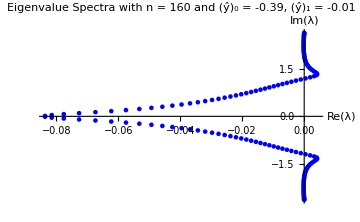
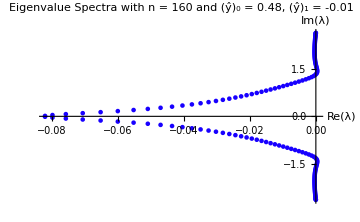
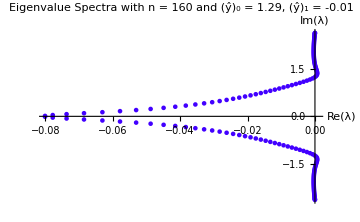
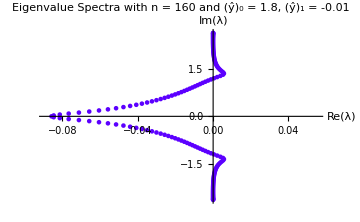
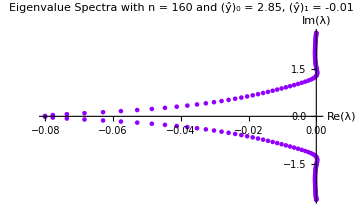
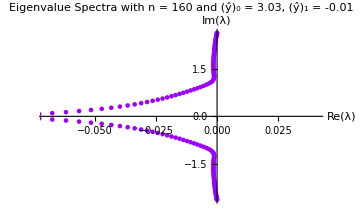
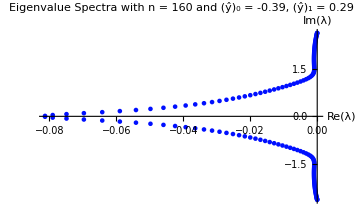
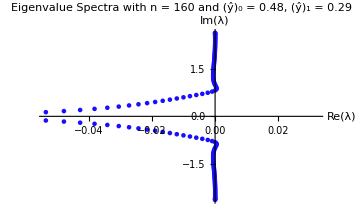

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{yy,zz}];*)

(*Define ŷ values*)
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,1]],

{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,1]],

{m,1,Length@stable}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Dendro Output for All Stable Operators

```mathematica
ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Dendro Output HIDE Block*)
derivativeOrder=1;
interiorOrder=4;
totalBoundRows=2;
LHSBandCount=5;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList={a1,a2};
interiorParametersValues=interiorNate/.{α->alpha,β->beta};
boundaryParametersValues=boundaryNate/.{γ01->gamma01,γ02->gamma02,γ10->gamma10,γ12->gamma12,γ13->gamma13};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a10,a11,a12,a13,a14};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)

(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str];
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
];

(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]];
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]];
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]];

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]];

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
];


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>ToString[Total[t1List]]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
];

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];



(*Dendro Output SHOW Block*)
outExt="h";
(*Print header*)
(*Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];*)
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_C4_1st_Op",ToString[m],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]],
{m,1,Length@stable}]
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_C4_1st_Op1.h

Saved to file: BYU_C4_1st_Op3.h

Saved to file: BYU_C4_1st_Op4.h

Saved to file: BYU_C4_1st_Op5.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_C4_1st_Op2.h

{Null,Null,Null,Null,Null}

# A6 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat2List={(*1*)0.90,(*2*)1.41,(*3*)2.25,(*4*)2.73,(*5*)3.60,(*6*)3.99};
yHat1List={(*1*)0.33,(*2*)0.69,(*3*)1.77,(*4*)2.19,(*5*)3.30,(*6*)3.63};
yHat0List={(*1*)1.50,(*2*)1.59,(*3*)3.12,(*4*)3.27};

yHat2List={(*1*)0.45,(*2*)0.99,(*3*)1.59,(*4*)2.13,(*5*)2.88,(*6*)3.36,(*7*)4.02,(*8*)4.41};
yHat1List={(*1*)-0.16,(*2*)0.17,(*3*)1.07,(*4*)1.52,(*5*)2.45,(*6*)2.87,(*7*)3.80,(*8*)4.10};
yHat0List={(*1*)0.72,(*2*)2.19,(*3*)2.37,(*4*)3.84};

yHat2List={(*1*)0.12,(*2*)0.60,(*3*)1.02,(*4*)1.62,(*5*)2.25,(*6*)2.73,(*7*)3.39,(*8*)3.93,(*9*)4.74};
yHat1List={(*1*)-0.52,(*2*)-0.28,(*3*)0.47,(*4*)0.95,(*5*)1.76,(*6*)2.21,(*7*)3.02,(*8*)3.47,(*9*)4.25,(*10*)4.49};
yHat0List={(*1*)0.03,(*2*)1.50,(*3*)3.06,(*4*)4.32};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
ParallelEvaluate[Get["A6_interiorCoeffs.mx"]]
ParallelEvaluate[Get["A6_bdCoeffs0.mx"]]
ParallelEvaluate[Get["A6_bdCoeffs1.mx"]]
ParallelEvaluate[Get["A6_bdCoeffs2.mx"]]
```

{Null,Null,Null,Null}

{Null,Null,Null,Null}

{Null,Null,Null,Null}

«1 more identical outputs»

```mathematica
DistributeDefinitions[yHat0List,yHat1List,yHat2List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,yHat2List,LHS,LHSRows,RHS,RHSRows,k}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]]},Max[Re[eigs]]},

{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{{{{0.03,-0.52,0.12},0.116895},{{1.5,-0.52,0.12},0.162133},{{3.06,-0.52,0.12},0.258725},{{4.32,-0.52,0.12},0.473582}},{{{0.03,-0.28,0.12},0.489787},{{1.5,-0.28,0.12},0.27257},{{3.06,-0.28,0.12},0.240901},{{4.32,-0.28,0.12},0.2482}},{{{0.03,0.47,0.12},0.115906},{{1.5,0.47,0.12},0.134153},{{3.06,0.47,0.12},0.27771},{{4.32,0.47,0.12},14.5975}},{{{0.03,0.95,0.12},4.96917},{{1.5,0.95,0.12},0.163524},{{3.06,0.95,0.12},0.251462},{{4.32,0.95,0.12},0.349867}},{{{0.03,1.76,0.12},0.143365},{{1.5,1.76,0.12},0.146974},{{3.06,1.76,0.12},0.519838},{{4.32,1.76,0.12},0.138005}},{{{0.03,2.21,0.12},3.14325},{{1.5,2.21,0.12},0.159897},{{3.06,2.21,0.12},0.263903},{{4.32,2.21,0.12},0.513052}},{{{0.03,3.02,0.12},0.28432},{{1.5,3.02,0.12},0.28255},{{3.06,3.02,0.12},0.267627},{{4.32,3.02,0.12},0.280044}},{{{0.03,3.47,0.12},2.05789},{{1.5,3.47,0.12},0.254916},{{3.06,3.47,0.12},0.223253},{{4.32,3.47,0.12},0.683482}},{{{0.03,4.25,0.12},0.448318},{{1.5,4.25,0.12},0.416133},{{3.06,4.25,0.12},0.211057},{{4.32,4.25,0.12},4.92923}},{{{0.03,4.49,0.12},1.09138},{{1.5,4.49,0.12},0.432516},{{3.06,4.49,0.12},0.214762},{{4.32,4.49,0.12},0.0156211}}},{{{{0.03,-0.52,0.6},0.187145},{{1.5,-0.52,0.6},0.370473},{{3.06,-0.52,0.6},0.41278},{{4.32,-0.52,0.6},0.456503}},{{{0.03,-0.28,0.6},2.47797},{{1.5,-0.28,0.6},0.217975},{{3.06,-0.28,0.6},0.374226},{{4.32,-0.28,0.6},0.45461}},{{{0.03,0.47,0.6},0.133412},{{1.5,0.47,0.6},0.10319},{{3.06,0.47,0.6},0.0229607},{{4.32,0.47,0.6},0.208481}},{{{0.03,0.95,0.6},2.41452},{{1.5,0.95,0.6},0.156187},{{3.06,0.95,0.6},0.320322},{{4.32,0.95,0.6},0.464923}},{{{0.03,1.76,0.6},0.303856},{{1.5,1.76,0.6},0.168751},{{3.06,1.76,0.6},12.953},{{4.32,1.76,0.6},0.382467}},{{{0.03,2.21,0.6},0.241169},{{1.5,2.21,0.6},0.153476},{{3.06,2.21,0.6},0.251791},{{4.32,2.21,0.6},0.409249}},{{{0.03,3.02,0.6},0.672853},{{1.5,3.02,0.6},0.413442},{{3.06,3.02,0.6},0.27115},{{4.32,3.02,0.6},0.433856}},{{{0.03,3.47,0.6},0.156694},{{1.5,3.47,0.6},0.193758},{{3.06,3.47,0.6},0.288069},{{4.32,3.47,0.6},0.404907}},{{{0.03,4.25,0.6},2.50906},{{1.5,4.25,0.6},2.50777},{{3.06,4.25,0.6},2.47349},{{4.32,4.25,0.6},2.71613}},{{{0.03,4.49,0.6},0.161792},{{1.5,4.49,0.6},0.227731},{{3.06,4.49,0.6},0.337991},{{4.32,4.49,0.6},0.465238}}},{{{{0.03,-0.52,1.02},0.116643},{{1.5,-0.52,1.02},0.157648},{{3.06,-0.52,1.02},0.261414},{{4.32,-0.52,1.02},0.476631}},{{{0.03,-0.28,1.02},0.292762},{{1.5,-0.28,1.02},0.306589},{{3.06,-0.28,1.02},0.203953},{{4.32,-0.28,1.02},0.187182}},{{{0.03,0.47,1.02},0.116136},{{1.5,0.47,1.02},0.138561},{{3.06,0.47,1.02},0.313879},{{4.32,0.47,1.02},5.95972}},{{{0.03,0.95,1.02},4.9995},{{1.5,0.95,1.02},0.163973},{{3.06,0.95,1.02},0.249789},{{4.32,0.95,1.02},0.348004}},{{{0.03,1.76,1.02},0.134903},{{1.5,1.76,1.02},0.147813},{{3.06,1.76,1.02},0.541824},{{4.32,1.76,1.02},0.122815}},{{{0.03,2.21,1.02},1.63385},{{1.5,2.21,1.02},0.159921},{{3.06,2.21,1.02},0.389263},{{4.32,2.21,1.02},6.60232}},{{{0.03,3.02,1.02},0.248189},{{1.5,3.02,1.02},0.251136},{{3.06,3.02,1.02},0.293594},{{4.32,3.02,1.02},0.259469}},{{{0.03,3.47,1.02},0.315761},{{1.5,3.47,1.02},0.312638},{{3.06,3.47,1.02},0.338347},{{4.32,3.47,1.02},0.323242}},{{{0.03,4.25,1.02},0.426984},{{1.5,4.25,1.02},0.373384},{{3.06,4.25,1.02},0.145793},{{4.32,4.25,1.02},6.4208}},{{{0.03,4.49,1.02},0.444194},{{1.5,4.49,1.02},12.1427},{{3.06,4.49,1.02},0.0808611},{{4.32,4.49,1.02},0.0889182}}},{{{{0.03,-0.52,1.62},1.47399},{{1.5,-0.52,1.62},0.0552356},{{3.06,-0.52,1.62},2.51429},{{4.32,-0.52,1.62},1.19325}},{{{0.03,-0.28,1.62},0.141479},{{1.5,-0.28,1.62},0.212114},{{3.06,-0.28,1.62},119.02},{{4.32,-0.28,1.62},0.106297}},{{{0.03,0.47,1.62},2.13865},{{1.5,0.47,1.62},0.367745},{{3.06,0.47,1.62},2.5626},{{4.32,0.47,1.62},1.69426}},{{{0.03,0.95,1.62},0.124323},{{1.5,0.95,1.62},0.152773},{{3.06,0.95,1.62},28.8383},{{4.32,0.95,1.62},0.106883}},{{{0.03,1.76,1.62},555.584},{{1.5,1.76,1.62},20.8241},{{3.06,1.76,1.62},4.23329},{{4.32,1.76,1.62},9.25491}},{{{0.03,2.21,1.62},0.135603},{{1.5,2.21,1.62},0.150075},{{3.06,2.21,1.62},2.08982},{{4.32,2.21,1.62},0.122657}},{{{0.03,3.02,1.62},4.20279},{{1.5,3.02,1.62},3.93374},{{3.06,3.02,1.62},3.77937},{{4.32,3.02,1.62},3.99773}},{{{0.03,3.47,1.62},0.176615},{{1.5,3.47,1.62},0.188217},{{3.06,3.47,1.62},0.127774},{{4.32,3.47,1.62},0.165858}},{{{0.03,4.25,1.62},8.69343},{{1.5,4.25,1.62},13.9906},{{3.06,4.25,1.62},0.321581},{{4.32,4.25,1.62},64.7715}},{{{0.03,4.49,1.62},0.195308},{{1.5,4.49,1.62},0.217923},{{3.06,4.49,1.62},0.116652},{{4.32,4.49,1.62},0.176317}}},{{{{0.03,-0.52,2.25},0.126193},{{1.5,-0.52,2.25},0.154066},{{3.06,-0.52,2.25},0.226459},{{4.32,-0.52,2.25},0.462942}},{{{0.03,-0.28,2.25},0.123005},{{1.5,-0.28,2.25},0.978281},{{3.06,-0.28,2.25},0.16034},{{4.32,-0.28,2.25},0.146847}},{{{0.03,0.47,2.25},0.125496},{{1.5,0.47,2.25},0.145059},{{3.06,0.47,2.25},0.28334},{{4.32,0.47,2.25},6.5834}},{{{0.03,0.95,2.25},0.360118},{{1.5,0.95,2.25},0.166582},{{3.06,0.95,2.25},0.190917},{{4.32,0.95,2.25},0.204779}},{{{0.03,1.76,2.25},0.13738},{{1.5,1.76,2.25},0.149581},{{3.06,1.76,2.25},0.484959},{{4.32,1.76,2.25},0.126074}},{{{0.03,2.21,2.25},1.77375},{{1.5,2.21,2.25},0.159857},{{3.06,2.21,2.25},0.276008},{{4.32,2.21,2.25},1.89074}},{{{0.03,3.02,2.25},0.198529},{{1.5,3.02,2.25},0.200434},{{3.06,3.02,2.25},0.255583},{{4.32,3.02,2.25},0.210972}},{{{0.03,3.47,2.25},11.4032},{{1.5,3.47,2.25},0.0953952},{{3.06,3.47,2.25},0.382762},{{4.32,3.47,2.25},0.530448}},{{{0.03,4.25,2.25},0.339818},{{1.5,4.25,2.25},0.272689},{{3.06,4.25,2.25},0.134382},{{4.32,4.25,2.25},6.08709}},{{{0.03,4.49,2.25},0.663766},{{1.5,4.49,2.25},0.105253},{{3.06,4.49,2.25},3.77929},{{4.32,4.49,2.25},6.17317}}},{{{{0.03,-0.52,2.73},2.0181},{{1.5,-0.52,2.73},0.583247},{{3.06,-0.52,2.73},2.15219},{{4.32,-0.52,2.73},0.755282}},{{{0.03,-0.28,2.73},0.364699},{{1.5,-0.28,2.73},0.345635},{{3.06,-0.28,2.73},0.396449},{{4.32,-0.28,2.73},0.384826}},{{{0.03,0.47,2.73},2.17781},{{1.5,0.47,2.73},0.931572},{{3.06,0.47,2.73},2.16529},{{4.32,0.47,2.73},1.75653}},{{{0.03,0.95,2.73},0.236272},{{1.5,0.95,2.73},0.200968},{{3.06,0.95,2.73},0.296092},{{4.32,0.95,2.73},0.271989}},{{{0.03,1.76,2.73},2.7046},{{1.5,1.76,2.73},1.41372},{{3.06,1.76,2.73},6.7015},{{4.32,1.76,2.73},2.77075}},{{{0.03,2.21,2.73},0.188708},{{1.5,2.21,2.73},0.188994},{{3.06,2.21,2.73},0.187487},{{4.32,2.21,2.73},0.187922}},{{{0.03,3.02,2.73},1.44058},{{1.5,3.02,2.73},0.391702},{{3.06,3.02,2.73},0.488645},{{4.32,3.02,2.73},0.464466}},{{{0.03,3.47,2.73},0.331372},{{1.5,3.47,2.73},0.360865},{{3.06,3.47,2.73},0.26376},{{4.32,3.47,2.73},0.290768}},{{{0.03,4.25,2.73},0.458146},{{1.5,4.25,2.73},0.491655},{{3.06,4.25,2.73},4.59151},{{4.32,4.25,2.73},9.94352}},{{{0.03,4.49,2.73},0.390654},{{1.5,4.49,2.73},0.408779},{{3.06,4.49,2.73},0.327358},{{4.32,4.49,2.73},0.35468}}},{{{{0.03,-0.52,3.39},0.178774},{{1.5,-0.52,3.39},0.229349},{{3.06,-0.52,3.39},0.281774},{{4.32,-0.52,3.39},0.458308}},{{{0.03,-0.28,3.39},0.263436},{{1.5,-0.28,3.39},0.247681},{{3.06,-0.28,3.39},0.249691},{{4.32,-0.28,3.39},0.251724}},{{{0.03,0.47,3.39},0.175768},{{1.5,0.47,3.39},0.21865},{{3.06,0.47,3.39},0.3269},{{4.32,0.47,3.39},11.1834}},{{{0.03,0.95,3.39},0.385769},{{1.5,0.95,3.39},13.8935},{{3.06,0.95,3.39},0.290494},{{4.32,0.95,3.39},0.315253}},{{{0.03,1.76,3.39},0.192731},{{1.5,1.76,3.39},0.21875},{{3.06,1.76,3.39},0.432473},{{4.32,1.76,3.39},0.166244}},{{{0.03,2.21,3.39},1.54064},{{1.5,2.21,3.39},6.4021},{{3.06,2.21,3.39},0.431311},{{4.32,2.21,3.39},0.513495}},{{{0.03,3.02,3.39},0.257064},{{1.5,3.02,3.39},0.261379},{{3.06,3.02,3.39},0.312921},{{4.32,3.02,3.39},0.271106}},{{{0.03,3.47,3.39},0.258339},{{1.5,3.47,3.39},0.262904},{{3.06,3.47,3.39},0.185134},{{4.32,3.47,3.39},4.44028}},{{{0.03,4.25,3.39},0.355197},{{1.5,4.25,3.39},0.30896},{{3.06,4.25,3.39},0.171185},{{4.32,4.25,3.39},4.98292}},{{{0.03,4.49,3.39},0.209858},{{1.5,4.49,3.39},0.225469},{{3.06,4.49,3.39},225.631},{{4.32,4.49,3.39},0.269691}}},{{{{0.03,-0.52,3.93},0.238112},{{1.5,-0.52,3.93},0.283382},{{3.06,-0.52,3.93},0.323572},{{4.32,-0.52,3.93},0.486106}},{{{0.03,-0.28,3.93},0.460611},{{1.5,-0.28,3.93},22.7516},{{3.06,-0.28,3.93},0.2845},{{4.32,-0.28,3.93},0.322594}},{{{0.03,0.47,3.93},0.225233},{{1.5,0.47,3.93},0.238922},{{3.06,0.47,3.93},0.306975},{{4.32,0.47,3.93},0.205717}},{{{0.03,0.95,3.93},0.546366},{{1.5,0.95,3.93},6.59489},{{3.06,0.95,3.93},0.249801},{{4.32,0.95,3.93},0.335804}},{{{0.03,1.76,3.93},0.262124},{{1.5,1.76,3.93},0.218815},{{3.06,1.76,3.93},0.275724},{{4.32,1.76,3.93},0.291534}},{{{0.03,2.21,3.93},0.521724},{{1.5,2.21,3.93},5.96882},{{3.06,2.21,3.93},0.173188},{{4.32,2.21,3.93},0.340899}},{{{0.03,3.02,3.93},0.364705},{{1.5,3.02,3.93},0.350519},{{3.06,3.02,3.93},0.276385},{{4.32,3.02,3.93},0.341559}},{{{0.03,3.47,3.93},0.549336},{{1.5,3.47,3.93},2.31398},{{3.06,3.47,3.93},0.215889},{{4.32,3.47,3.93},0.302301}},{{{0.03,4.25,3.93},0.455564},{{1.5,4.25,3.93},0.440992},{{3.06,4.25,3.93},0.373406},{{4.32,4.25,3.93},0.827775}},{{{0.03,4.49,3.93},0.451791},{{1.5,4.49,3.93},0.674787},{{3.06,4.49,3.93},0.259713},{{4.32,4.49,3.93},0.298057}}},{{{{0.03,-0.52,4.74},0.0194042},{{1.5,-0.52,4.74},0.034057},{{3.06,-0.52,4.74},0.106539},{{4.32,-0.52,4.74},0.374611}},{{{0.03,-0.28,4.74},0.322961},{{1.5,-0.28,4.74},1.23182},{{3.06,-0.28,4.74},0.119207},{{4.32,-0.28,4.74},0.0374227}},{{{0.03,0.47,4.74},0.0223541},{{1.5,0.47,4.74},0.0164636},{{3.06,0.47,4.74},0.124766},{{4.32,0.47,4.74},0.187302}},{{{0.03,0.95,4.74},0.480317},{{1.5,0.95,4.74},1.0367},{{3.06,0.95,4.74},0.0702563},{{4.32,0.95,4.74},0.0463516}},{{{0.03,1.76,4.74},0.0144228},{{1.5,1.76,4.74},0.0210923},{{3.06,1.76,4.74},0.0648112},{{4.32,1.76,4.74},0.138687}},{{{0.03,2.21,4.74},0.736759},{{1.5,2.21,4.74},1.00328},{{3.06,2.21,4.74},0.0972642},{{4.32,2.21,4.74},0.0131047}},{{{0.03,3.02,4.74},0.204623},{{1.5,3.02,4.74},0.173467},{{3.06,3.02,4.74},0.0251647},{{4.32,3.02,4.74},0.127261}},{{{0.03,3.47,4.74},0.481574},{{1.5,3.47,4.74},29.3379},{{3.06,3.47,4.74},0.178455},{{4.32,3.47,4.74},0.0242344}},{{{0.03,4.25,4.74},0.368609},{{1.5,4.25,4.74},0.362345},{{3.06,4.25,4.74},0.348113},{{4.32,4.25,4.74},0.570195}},{{{0.03,4.49,4.74},0.314054},{{1.5,4.49,4.74},1.04635},{{3.06,4.49,4.74},0.20067},{{4.32,4.49,4.74},0.0354831}}}}

```mathematica
DumpSave["A6_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["A6_MaxReList.mx"]
```

```mathematica
maxReList//TableForm
Dimensions@maxReList
trimmed=Flatten[maxReList,2];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

0.03
-0.52
0.12 | 0.116895
1.5
-0.52
0.12 | 0.162133
3.06
-0.52
0.12 | 0.258725
4.32
-0.52
0.12 | 0.473582 | 0.03
-0.28
0.12 | 0.489787
1.5
-0.28
0.12 | 0.27257
3.06
-0.28
0.12 | 0.240901
4.32
-0.28
0.12 | 0.2482 | 0.03
0.47
0.12 | 0.115906
1.5
0.47
0.12 | 0.134153
3.06
0.47
0.12 | 0.27771
4.32
0.47
0.12 | 14.5975 | 0.03
0.95
0.12 | 4.96917
1.5
0.95
0.12 | 0.163524
3.06
0.95
0.12 | 0.251462
4.32
0.95
0.12 | 0.349867 | 0.03
1.76
0.12 | 0.143365
1.5
1.76
0.12 | 0.146974
3.06
1.76
0.12 | 0.519838
4.32
1.76
0.12 | 0.138005 | 0.03
2.21
0.12 | 3.14325
1.5
2.21
0.12 | 0.159897
3.06
2.21
0.12 | 0.263903
4.32
2.21
0.12 | 0.513052 | 0.03
3.02
0.12 | 0.28432
1.5
3.02
0.12 | 0.28255
3.06
3.02
0.12 | 0.267627
4.32
3.02
0.12 | 0.280044 | 0.03
3.47
0.12 | 2.05789
1.5
3.47
0.12 | 0.254916
3.06
3.47
0.12 | 0.223253
4.32
3.47
0.12 | 0.683482 | 0.03
4.25
0.12 | 0.448318
1.5
4.25
0.12 | 0.416133
3.06
4.25
0.12 | 0.211057
4.32
4.25
0.12 | 4.92923 | 0.03
4.49
0.12 | 1.09138
1.5
4.49
0.12 | 0.432516
3.06
4.49
0.12 | 0.214762
4.32
4.49
0.12 | 0.0156211
0.03
-0.52
0.6 | 0.187145
1.5
-0.52
0.6 | 0.370473
3.06
-0.52
0.6 | 0.41278
4.32
-0.52
0.6 | 0.456503 | 0.03
-0.28
0.6 | 2.47797
1.5
-0.28
0.6 | 0.217975
3.06
-0.28
0.6 | 0.374226
4.32
-0.28
0.6 | 0.45461 | 0.03
0.47
0.6 | 0.133412
1.5
0.47
0.6 | 0.10319
3.06
0.47
0.6 | 0.0229607
4.32
0.47
0.6 | 0.208481 | 0.03
0.95
0.6 | 2.41452
1.5
0.95
0.6 | 0.156187
3.06
0.95
0.6 | 0.320322
4.32
0.95
0.6 | 0.464923 | 0.03
1.76
0.6 | 0.303856
1.5
1.76
0.6 | 0.168751
3.06
1.76
0.6 | 12.953
4.32
1.76
0.6 | 0.382467 | 0.03
2.21
0.6 | 0.241169
1.5
2.21
0.6 | 0.153476
3.06
2.21
0.6 | 0.251791
4.32
2.21
0.6 | 0.409249 | 0.03
3.02
0.6 | 0.672853
1.5
3.02
0.6 | 0.413442
3.06
3.02
0.6 | 0.27115
4.32
3.02
0.6 | 0.433856 | 0.03
3.47
0.6 | 0.156694
1.5
3.47
0.6 | 0.193758
3.06
3.47
0.6 | 0.288069
4.32
3.47
0.6 | 0.404907 | 0.03
4.25
0.6 | 2.50906
1.5
4.25
0.6 | 2.50777
3.06
4.25
0.6 | 2.47349
4.32
4.25
0.6 | 2.71613 | 0.03
4.49
0.6 | 0.161792
1.5
4.49
0.6 | 0.227731
3.06
4.49
0.6 | 0.337991
4.32
4.49
0.6 | 0.465238
0.03
-0.52
1.02 | 0.116643
1.5
-0.52
1.02 | 0.157648
3.06
-0.52
1.02 | 0.261414
4.32
-0.52
1.02 | 0.476631 | 0.03
-0.28
1.02 | 0.292762
1.5
-0.28
1.02 | 0.306589
3.06
-0.28
1.02 | 0.203953
4.32
-0.28
1.02 | 0.187182 | 0.03
0.47
1.02 | 0.116136
1.5
0.47
1.02 | 0.138561
3.06
0.47
1.02 | 0.313879
4.32
0.47
1.02 | 5.95972 | 0.03
0.95
1.02 | 4.9995
1.5
0.95
1.02 | 0.163973
3.06
0.95
1.02 | 0.249789
4.32
0.95
1.02 | 0.348004 | 0.03
1.76
1.02 | 0.134903
1.5
1.76
1.02 | 0.147813
3.06
1.76
1.02 | 0.541824
4.32
1.76
1.02 | 0.122815 | 0.03
2.21
1.02 | 1.63385
1.5
2.21
1.02 | 0.159921
3.06
2.21
1.02 | 0.389263
4.32
2.21
1.02 | 6.60232 | 0.03
3.02
1.02 | 0.248189
1.5
3.02
1.02 | 0.251136
3.06
3.02
1.02 | 0.293594
4.32
3.02
1.02 | 0.259469 | 0.03
3.47
1.02 | 0.315761
1.5
3.47
1.02 | 0.312638
3.06
3.47
1.02 | 0.338347
4.32
3.47
1.02 | 0.323242 | 0.03
4.25
1.02 | 0.426984
1.5
4.25
1.02 | 0.373384
3.06
4.25
1.02 | 0.145793
4.32
4.25
1.02 | 6.4208 | 0.03
4.49
1.02 | 0.444194
1.5
4.49
1.02 | 12.1427
3.06
4.49
1.02 | 0.0808611
4.32
4.49
1.02 | 0.0889182
0.03
-0.52
1.62 | 1.47399
1.5
-0.52
1.62 | 0.0552356
3.06
-0.52
1.62 | 2.51429
4.32
-0.52
1.62 | 1.19325 | 0.03
-0.28
1.62 | 0.141479
1.5
-0.28
1.62 | 0.212114
3.06
-0.28
1.62 | 119.02
4.32
-0.28
1.62 | 0.106297 | 0.03
0.47
1.62 | 2.13865
1.5
0.47
1.62 | 0.367745
3.06
0.47
1.62 | 2.5626
4.32
0.47
1.62 | 1.69426 | 0.03
0.95
1.62 | 0.124323
1.5
0.95
1.62 | 0.152773
3.06
0.95
1.62 | 28.8383
4.32
0.95
1.62 | 0.106883 | 0.03
1.76
1.62 | 555.584
1.5
1.76
1.62 | 20.8241
3.06
1.76
1.62 | 4.23329
4.32
1.76
1.62 | 9.25491 | 0.03
2.21
1.62 | 0.135603
1.5
2.21
1.62 | 0.150075
3.06
2.21
1.62 | 2.08982
4.32
2.21
1.62 | 0.122657 | 0.03
3.02
1.62 | 4.20279
1.5
3.02
1.62 | 3.93374
3.06
3.02
1.62 | 3.77937
4.32
3.02
1.62 | 3.99773 | 0.03
3.47
1.62 | 0.176615
1.5
3.47
1.62 | 0.188217
3.06
3.47
1.62 | 0.127774
4.32
3.47
1.62 | 0.165858 | 0.03
4.25
1.62 | 8.69343
1.5
4.25
1.62 | 13.9906
3.06
4.25
1.62 | 0.321581
4.32
4.25
1.62 | 64.7715 | 0.03
4.49
1.62 | 0.195308
1.5
4.49
1.62 | 0.217923
3.06
4.49
1.62 | 0.116652
4.32
4.49
1.62 | 0.176317
0.03
-0.52
2.25 | 0.126193
1.5
-0.52
2.25 | 0.154066
3.06
-0.52
2.25 | 0.226459
4.32
-0.52
2.25 | 0.462942 | 0.03
-0.28
2.25 | 0.123005
1.5
-0.28
2.25 | 0.978281
3.06
-0.28
2.25 | 0.16034
4.32
-0.28
2.25 | 0.146847 | 0.03
0.47
2.25 | 0.125496
1.5
0.47
2.25 | 0.145059
3.06
0.47
2.25 | 0.28334
4.32
0.47
2.25 | 6.5834 | 0.03
0.95
2.25 | 0.360118
1.5
0.95
2.25 | 0.166582
3.06
0.95
2.25 | 0.190917
4.32
0.95
2.25 | 0.204779 | 0.03
1.76
2.25 | 0.13738
1.5
1.76
2.25 | 0.149581
3.06
1.76
2.25 | 0.484959
4.32
1.76
2.25 | 0.126074 | 0.03
2.21
2.25 | 1.77375
1.5
2.21
2.25 | 0.159857
3.06
2.21
2.25 | 0.276008
4.32
2.21
2.25 | 1.89074 | 0.03
3.02
2.25 | 0.198529
1.5
3.02
2.25 | 0.200434
3.06
3.02
2.25 | 0.255583
4.32
3.02
2.25 | 0.210972 | 0.03
3.47
2.25 | 11.4032
1.5
3.47
2.25 | 0.0953952
3.06
3.47
2.25 | 0.382762
4.32
3.47
2.25 | 0.530448 | 0.03
4.25
2.25 | 0.339818
1.5
4.25
2.25 | 0.272689
3.06
4.25
2.25 | 0.134382
4.32
4.25
2.25 | 6.08709 | 0.03
4.49
2.25 | 0.663766
1.5
4.49
2.25 | 0.105253
3.06
4.49
2.25 | 3.77929
4.32
4.49
2.25 | 6.17317
0.03
-0.52
2.73 | 2.0181
1.5
-0.52
2.73 | 0.583247
3.06
-0.52
2.73 | 2.15219
4.32
-0.52
2.73 | 0.755282 | 0.03
-0.28
2.73 | 0.364699
1.5
-0.28
2.73 | 0.345635
3.06
-0.28
2.73 | 0.396449
4.32
-0.28
2.73 | 0.384826 | 0.03
0.47
2.73 | 2.17781
1.5
0.47
2.73 | 0.931572
3.06
0.47
2.73 | 2.16529
4.32
0.47
2.73 | 1.75653 | 0.03
0.95
2.73 | 0.236272
1.5
0.95
2.73 | 0.200968
3.06
0.95
2.73 | 0.296092
4.32
0.95
2.73 | 0.271989 | 0.03
1.76
2.73 | 2.7046
1.5
1.76
2.73 | 1.41372
3.06
1.76
2.73 | 6.7015
4.32
1.76
2.73 | 2.77075 | 0.03
2.21
2.73 | 0.188708
1.5
2.21
2.73 | 0.188994
3.06
2.21
2.73 | 0.187487
4.32
2.21
2.73 | 0.187922 | 0.03
3.02
2.73 | 1.44058
1.5
3.02
2.73 | 0.391702
3.06
3.02
2.73 | 0.488645
4.32
3.02
2.73 | 0.464466 | 0.03
3.47
2.73 | 0.331372
1.5
3.47
2.73 | 0.360865
3.06
3.47
2.73 | 0.26376
4.32
3.47
2.73 | 0.290768 | 0.03
4.25
2.73 | 0.458146
1.5
4.25
2.73 | 0.491655
3.06
4.25
2.73 | 4.59151
4.32
4.25
2.73 | 9.94352 | 0.03
4.49
2.73 | 0.390654
1.5
4.49
2.73 | 0.408779
3.06
4.49
2.73 | 0.327358
4.32
4.49
2.73 | 0.35468
0.03
-0.52
3.39 | 0.178774
1.5
-0.52
3.39 | 0.229349
3.06
-0.52
3.39 | 0.281774
4.32
-0.52
3.39 | 0.458308 | 0.03
-0.28
3.39 | 0.263436
1.5
-0.28
3.39 | 0.247681
3.06
-0.28
3.39 | 0.249691
4.32
-0.28
3.39 | 0.251724 | 0.03
0.47
3.39 | 0.175768
1.5
0.47
3.39 | 0.21865
3.06
0.47
3.39 | 0.3269
4.32
0.47
3.39 | 11.1834 | 0.03
0.95
3.39 | 0.385769
1.5
0.95
3.39 | 13.8935
3.06
0.95
3.39 | 0.290494
4.32
0.95
3.39 | 0.315253 | 0.03
1.76
3.39 | 0.192731
1.5
1.76
3.39 | 0.21875
3.06
1.76
3.39 | 0.432473
4.32
1.76
3.39 | 0.166244 | 0.03
2.21
3.39 | 1.54064
1.5
2.21
3.39 | 6.4021
3.06
2.21
3.39 | 0.431311
4.32
2.21
3.39 | 0.513495 | 0.03
3.02
3.39 | 0.257064
1.5
3.02
3.39 | 0.261379
3.06
3.02
3.39 | 0.312921
4.32
3.02
3.39 | 0.271106 | 0.03
3.47
3.39 | 0.258339
1.5
3.47
3.39 | 0.262904
3.06
3.47
3.39 | 0.185134
4.32
3.47
3.39 | 4.44028 | 0.03
4.25
3.39 | 0.355197
1.5
4.25
3.39 | 0.30896
3.06
4.25
3.39 | 0.171185
4.32
4.25
3.39 | 4.98292 | 0.03
4.49
3.39 | 0.209858
1.5
4.49
3.39 | 0.225469
3.06
4.49
3.39 | 225.631
4.32
4.49
3.39 | 0.269691
0.03
-0.52
3.93 | 0.238112
1.5
-0.52
3.93 | 0.283382
3.06
-0.52
3.93 | 0.323572
4.32
-0.52
3.93 | 0.486106 | 0.03
-0.28
3.93 | 0.460611
1.5
-0.28
3.93 | 22.7516
3.06
-0.28
3.93 | 0.2845
4.32
-0.28
3.93 | 0.322594 | 0.03
0.47
3.93 | 0.225233
1.5
0.47
3.93 | 0.238922
3.06
0.47
3.93 | 0.306975
4.32
0.47
3.93 | 0.205717 | 0.03
0.95
3.93 | 0.546366
1.5
0.95
3.93 | 6.59489
3.06
0.95
3.93 | 0.249801
4.32
0.95
3.93 | 0.335804 | 0.03
1.76
3.93 | 0.262124
1.5
1.76
3.93 | 0.218815
3.06
1.76
3.93 | 0.275724
4.32
1.76
3.93 | 0.291534 | 0.03
2.21
3.93 | 0.521724
1.5
2.21
3.93 | 5.96882
3.06
2.21
3.93 | 0.173188
4.32
2.21
3.93 | 0.340899 | 0.03
3.02
3.93 | 0.364705
1.5
3.02
3.93 | 0.350519
3.06
3.02
3.93 | 0.276385
4.32
3.02
3.93 | 0.341559 | 0.03
3.47
3.93 | 0.549336
1.5
3.47
3.93 | 2.31398
3.06
3.47
3.93 | 0.215889
4.32
3.47
3.93 | 0.302301 | 0.03
4.25
3.93 | 0.455564
1.5
4.25
3.93 | 0.440992
3.06
4.25
3.93 | 0.373406
4.32
4.25
3.93 | 0.827775 | 0.03
4.49
3.93 | 0.451791
1.5
4.49
3.93 | 0.674787
3.06
4.49
3.93 | 0.259713
4.32
4.49
3.93 | 0.298057
0.03
-0.52
4.74 | 0.0194042
1.5
-0.52
4.74 | 0.034057
3.06
-0.52
4.74 | 0.106539
4.32
-0.52
4.74 | 0.374611 | 0.03
-0.28
4.74 | 0.322961
1.5
-0.28
4.74 | 1.23182
3.06
-0.28
4.74 | 0.119207
4.32
-0.28
4.74 | 0.0374227 | 0.03
0.47
4.74 | 0.0223541
1.5
0.47
4.74 | 0.0164636
3.06
0.47
4.74 | 0.124766
4.32
0.47
4.74 | 0.187302 | 0.03
0.95
4.74 | 0.480317
1.5
0.95
4.74 | 1.0367
3.06
0.95
4.74 | 0.0702563
4.32
0.95
4.74 | 0.0463516 | 0.03
1.76
4.74 | 0.0144228
1.5
1.76
4.74 | 0.0210923
3.06
1.76
4.74 | 0.0648112
4.32
1.76
4.74 | 0.138687 | 0.03
2.21
4.74 | 0.736759
1.5
2.21
4.74 | 1.00328
3.06
2.21
4.74 | 0.0972642
4.32
2.21
4.74 | 0.0131047 | 0.03
3.02
4.74 | 0.204623
1.5
3.02
4.74 | 0.173467
3.06
3.02
4.74 | 0.0251647
4.32
3.02
4.74 | 0.127261 | 0.03
3.47
4.74 | 0.481574
1.5
3.47
4.74 | 29.3379
3.06
3.47
4.74 | 0.178455
4.32
3.47
4.74 | 0.0242344 | 0.03
4.25
4.74 | 0.368609
1.5
4.25
4.74 | 0.362345
3.06
4.25
4.74 | 0.348113
4.32
4.25
4.74 | 0.570195 | 0.03
4.49
4.74 | 0.314054
1.5
4.49
4.74 | 1.04635
3.06
4.49
4.74 | 0.20067
4.32
4.49
4.74 | 0.0354831

{9,10,4,2}

{}

0

## Run Eigenvalue Spectra on All Operators

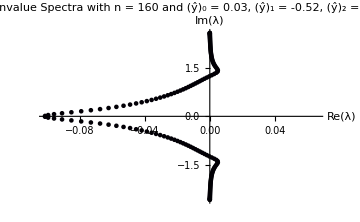
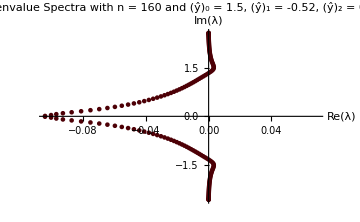
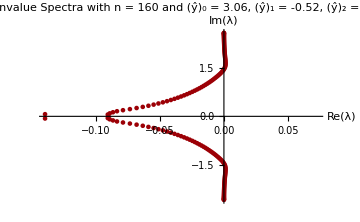
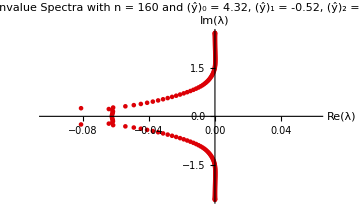
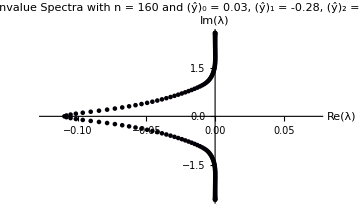
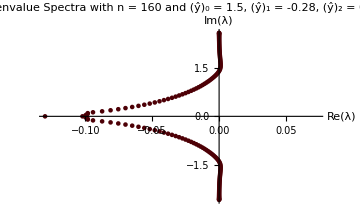
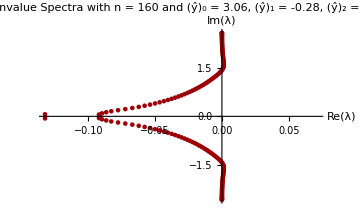
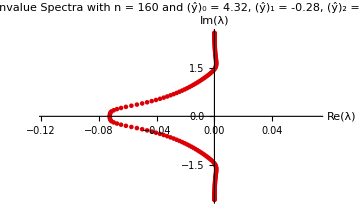
{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]],

{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsP4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]],

{m,1,Length@stable}]
```

# B6 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=4;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==3&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==5),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==1&&j==7),a17Bar,
If[(i==1&&j==8),a18Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,
If[(i==2&&j==7),a27Bar,
If[(i==2&&j==8),a28Bar,

If[(i==3&&j==1),a31Bar,
If[(i==3&&j==2),a32Bar,
If[(i==3&&j==3),a33Bar,
If[(i==3&&j==4),a34Bar,
If[(i==3&&j==5),a35Bar,
If[(i==3&&j==6),a36Bar,
If[(i==3&&j==7),a37Bar,
If[(i==3&&j==8),a38Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k&&j==k-7),-a07,
If[(i==k&&j==k-8),-a08,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-1&&j==k-7),-a17,
If[(i==k-1&&j==k-8),-a18,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,
If[(i==k-2&&j==k-7),-a27,
If[(i==k-2&&j==k-8),-a28,
If[(i==k-3&&j==k),-a30,
If[(i==k-3&&j==k-1),-a31,
If[(i==k-3&&j==k-2),-a32,
If[(i==k-3&&j==k-3),-a33,
If[(i==k-3&&j==k-4),-a34,
If[(i==k-3&&j==k-5),-a35,
If[(i==k-3&&j==k-6),-a36,
If[(i==k-3&&j==k-7),-a37,
If[(i==k-3&&j==k-8),-a38,


If[i-4==j,-a4,
If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
If[i+4==j,a4,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat3List={(*1*)2.94,(*2*)4.41};
yHat2List={(*1*)2.07,(*2*)2.85,(*3*)3.90,(*4*)4.14};
yHat1List={(*1*)1.77,(*2*)2.85,(*3*)3.48,(*4*)4.14};
yHat0List={(*1*)1.1,(*2*)2.8,(*3*)3.1,(*4*)4.1};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
ParallelEvaluate[Get["P6_interiorCoeffs.mx"]]
ParallelEvaluate[Get["P6_bdCoeffs0.mx"]]
ParallelEvaluate[Get["P6_bdCoeffs1.mx"]]
ParallelEvaluate[Get["P6_bdCoeffs2.mx"]]
ParallelEvaluate[Get["P6_bdCoeffs3.mx"]]
```

{Null,Null,Null,Null}

{Null,Null,Null,Null}

{Null,Null,Null,Null}

«2 more identical outputs»

```mathematica
DistributeDefinitions[yHat0List,yHat1List,yHat2List,yHat3List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,yHat2List,yHat3List,LHS,LHSRows,RHS,RHSRows,k}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
Print["Kernel ",$KernelID," working on ",{ww,xx,yy,zz}];

(*Define ŷ values*)
yHat3=yHat3List[[ww]];
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsP6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]],yHat3List[[ww]]},Max[Re[eigs]]},

{ww,1,Length@yHat3List},{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

Kernel 1 working on {1,1,1,1}

Kernel 2 working on {1,1,1,2}

Kernel 3 working on {1,1,1,3}

Kernel 4 working on {1,1,1,4}

Kernel 2 working on {1,1,2,1}

Kernel 4 working on {1,1,2,2}

Kernel 1 working on {1,1,2,3}

Kernel 3 working on {1,1,2,4}

Kernel 1 working on {1,1,3,1}

Kernel 4 working on {1,1,3,2}

Kernel 2 working on {1,1,3,3}

Kernel 3 working on {1,1,3,4}

Kernel 1 working on {1,1,4,1}

Kernel 2 working on {1,1,4,2}

Kernel 4 working on {1,1,4,3}

Kernel 3 working on {1,1,4,4}

Kernel 1 working on {1,2,1,1}

Kernel 2 working on {1,2,1,2}

Kernel 4 working on {1,2,1,3}

Kernel 3 working on {1,2,1,4}

Kernel 1 working on {1,2,2,1}

Kernel 2 working on {1,2,2,2}

Kernel 4 working on {1,2,2,3}

Kernel 3 working on {1,2,2,4}

Kernel 4 working on {1,2,3,1}

Kernel 1 working on {1,2,3,2}

Kernel 3 working on {1,2,3,3}

Kernel 2 working on {1,2,3,4}

Kernel 1 working on {1,2,4,1}

Kernel 4 working on {1,2,4,2}

Kernel 2 working on {1,2,4,3}

Kernel 3 working on {1,2,4,4}

Kernel 1 working on {1,3,1,1}

Kernel 3 working on {1,3,1,2}

Kernel 2 working on {1,3,1,3}

Kernel 4 working on {1,3,1,4}

Kernel 1 working on {1,3,2,1}

Kernel 3 working on {1,3,2,2}

Kernel 2 working on {1,3,2,3}

Kernel 4 working on {1,3,2,4}

Kernel 1 working on {1,3,3,1}

Kernel 3 working on {1,3,3,2}

Kernel 2 working on {1,3,3,3}

Kernel 4 working on {1,3,3,4}

Kernel 1 working on {1,3,4,1}

Kernel 3 working on {1,3,4,2}

Kernel 2 working on {1,3,4,3}

Kernel 4 working on {1,3,4,4}

Kernel 3 working on {1,4,1,1}

Kernel 1 working on {1,4,1,2}

Kernel 2 working on {1,4,1,3}

Kernel 4 working on {1,4,1,4}

Kernel 1 working on {1,4,2,1}

Kernel 3 working on {1,4,2,2}

Kernel 2 working on {1,4,2,3}

Kernel 4 working on {1,4,2,4}

Kernel 3 working on {1,4,3,1}

Kernel 1 working on {1,4,3,2}

Kernel 2 working on {1,4,3,3}

Kernel 4 working on {1,4,3,4}

Kernel 3 working on {1,4,4,1}

Kernel 1 working on {1,4,4,2}

Kernel 2 working on {1,4,4,3}

Kernel 4 working on {1,4,4,4}

Kernel 1 working on {2,1,1,1}

Kernel 3 working on {2,1,1,2}

Kernel 2 working on {2,1,1,3}

Kernel 4 working on {2,1,1,4}

Kernel 1 working on {2,1,2,1}

Kernel 3 working on {2,1,2,2}

Kernel 2 working on {2,1,2,3}

Kernel 4 working on {2,1,2,4}

Kernel 3 working on {2,1,3,1}

Kernel 1 working on {2,1,3,2}

Kernel 2 working on {2,1,3,3}

Kernel 4 working on {2,1,3,4}

Kernel 3 working on {2,1,4,1}

Kernel 1 working on {2,1,4,2}

Kernel 2 working on {2,1,4,3}

Kernel 4 working on {2,1,4,4}

Kernel 3 working on {2,2,1,1}

Kernel 1 working on {2,2,1,2}

Kernel 2 working on {2,2,1,3}

Kernel 4 working on {2,2,1,4}

Kernel 3 working on {2,2,2,1}

Kernel 1 working on {2,2,2,2}

Kernel 4 working on {2,2,2,3}

Kernel 2 working on {2,2,2,4}

Kernel 3 working on {2,2,3,1}

Kernel 1 working on {2,2,3,2}

Kernel 4 working on {2,2,3,3}

Kernel 2 working on {2,2,3,4}

Kernel 3 working on {2,2,4,1}

Kernel 1 working on {2,2,4,2}

Kernel 4 working on {2,2,4,3}

Kernel 2 working on {2,2,4,4}

Kernel 1 working on {2,3,1,1}

Kernel 3 working on {2,3,1,2}

Kernel 4 working on {2,3,1,3}

Kernel 2 working on {2,3,1,4}

Kernel 1 working on {2,3,2,1}

Kernel 3 working on {2,3,2,2}

Kernel 4 working on {2,3,2,3}

Kernel 2 working on {2,3,2,4}

Kernel 1 working on {2,3,3,1}

Kernel 4 working on {2,3,3,2}

Kernel 3 working on {2,3,3,3}

Kernel 2 working on {2,3,3,4}

Kernel 3 working on {2,3,4,1}

Kernel 4 working on {2,3,4,2}

Kernel 1 working on {2,3,4,3}

Kernel 2 working on {2,3,4,4}

Kernel 4 working on {2,4,1,1}

Kernel 3 working on {2,4,1,2}

Kernel 1 working on {2,4,1,3}

Kernel 2 working on {2,4,1,4}

Kernel 4 working on {2,4,2,1}

Kernel 3 working on {2,4,2,2}

Kernel 1 working on {2,4,2,3}

Kernel 2 working on {2,4,2,4}

Kernel 4 working on {2,4,3,1}

Kernel 3 working on {2,4,3,2}

Kernel 1 working on {2,4,3,3}

Kernel 2 working on {2,4,3,4}

Kernel 4 working on {2,4,4,1}

Kernel 3 working on {2,4,4,2}

Kernel 1 working on {2,4,4,3}

Kernel 2 working on {2,4,4,4}

{{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}}

```mathematica
DumpSave["P6_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["P6_MaxReList.mx"]
maxReList
```

{{{{{{1.1,1.77,2.07,2.94},0.069282},{{2.8,1.77,2.07,2.94},0.0102496},{{3.1,1.77,2.07,2.94},0.0991029},{{4.1,1.77,2.07,2.94},0.077854}},{{{1.1,2.85,2.07,2.94},0.0000432125},{{2.8,2.85,2.07,2.94},0.0539793},{{3.1,2.85,2.07,2.94},22.1718},{{4.1,2.85,2.07,2.94},0.0232438}},{{{1.1,3.48,2.07,2.94},0.0202968},{{2.8,3.48,2.07,2.94},0.000568977},{{3.1,3.48,2.07,2.94},0.0813532},{{4.1,3.48,2.07,2.94},0.000837856}},{{{1.1,4.14,2.07,2.94},0.0000319195},{{2.8,4.14,2.07,2.94},0.0118403},{{3.1,4.14,2.07,2.94},0.396571},{{4.1,4.14,2.07,2.94},0.00655337}}},{{{{1.1,1.77,2.85,2.94},15.5254},{{2.8,1.77,2.85,2.94},55.4902},{{3.1,1.77,2.85,2.94},12.9102},{{4.1,1.77,2.85,2.94},40.0806}},{{{1.1,2.85,2.85,2.94},0.21893},{{2.8,2.85,2.85,2.94},0.148787},{{3.1,2.85,2.85,2.94},0.18897},{{4.1,2.85,2.85,2.94},0.0742782}},{{{1.1,3.48,2.85,2.94},0.359166},{{2.8,3.48,2.85,2.94},1.00758},{{3.1,3.48,2.85,2.94},0.297548},{{4.1,3.48,2.85,2.94},0.214277}},{{{1.1,4.14,2.85,2.94},0.0108779},{{2.8,4.14,2.85,2.94},0.237209},{{3.1,4.14,2.85,2.94},0.0760478},{{4.1,4.14,2.85,2.94},0.128883}}},{{{{1.1,1.77,3.9,2.94},0.989462},{{2.8,1.77,3.9,2.94},2.55475},{{3.1,1.77,3.9,2.94},13.6205},{{4.1,1.77,3.9,2.94},2.9312}},{{{1.1,2.85,3.9,2.94},0.389326},{{2.8,2.85,3.9,2.94},0.181563},{{3.1,2.85,3.9,2.94},0.121108},{{4.1,2.85,3.9,2.94},0.102817}},{{{1.1,3.48,3.9,2.94},0.477142},{{2.8,3.48,3.9,2.94},2.52963},{{3.1,3.48,3.9,2.94},0.577374},{{4.1,3.48,3.9,2.94},4.72755}},{{{1.1,4.14,3.9,2.94},1.37821},{{2.8,4.14,3.9,2.94},0.519388},{{3.1,4.14,3.9,2.94},0.31295},{{4.1,4.14,3.9,2.94},0.44367}}},{{{{1.1,1.77,4.14,2.94},4.63694},{{2.8,1.77,4.14,2.94},18.1845},{{3.1,1.77,4.14,2.94},13.2829},{{4.1,1.77,4.14,2.94},24.1897}},{{{1.1,2.85,4.14,2.94},0.306118},{{2.8,2.85,4.14,2.94},0.163241},{{3.1,2.85,4.14,2.94},0.161186},{{4.1,2.85,4.14,2.94},0.0866187}},{{{1.1,3.48,4.14,2.94},0.427903},{{2.8,3.48,4.14,2.94},7.55634},{{3.1,3.48,4.14,2.94},0.374701},{{4.1,3.48,4.14,2.94},1.29256}},{{{1.1,4.14,4.14,2.94},0.701879},{{2.8,4.14,4.14,2.94},0.258149},{{3.1,4.14,4.14,2.94},0.0368424},{{4.1,4.14,4.14,2.94},0.149135}}}},{{{{{1.1,1.77,2.07,4.41},0.0703956},{{2.8,1.77,2.07,4.41},0.0128736},{{3.1,1.77,2.07,4.41},0.0999582},{{4.1,1.77,2.07,4.41},0.0809842}},{{{1.1,2.85,2.07,4.41},0.0000318686},{{2.8,2.85,2.07,4.41},0.0545362},{{3.1,2.85,2.07,4.41},25.7494},{{4.1,2.85,2.07,4.41},0.0238922}},{{{1.1,3.48,2.07,4.41},0.0212445},{{2.8,3.48,2.07,4.41},0.000548163},{{3.1,3.48,2.07,4.41},0.0820481},{{4.1,3.48,2.07,4.41},0.000735917}},{{{1.1,4.14,2.07,4.41},0.00103068},{{2.8,4.14,2.07,4.41},0.0132674},{{3.1,4.14,2.07,4.41},0.687309},{{4.1,4.14,2.07,4.41},0.00821918}}},{{{{1.1,1.77,2.85,4.41},2.18928},{{2.8,1.77,2.85,4.41},12.6119},{{3.1,1.77,2.85,4.41},24.3686},{{4.1,1.77,2.85,4.41},15.0491}},{{{1.1,2.85,2.85,4.41},0.292085},{{2.8,2.85,2.85,4.41},0.156526},{{3.1,2.85,2.85,4.41},0.172689},{{4.1,2.85,2.85,4.41},0.0799897}},{{{1.1,3.48,2.85,4.41},0.431607},{{2.8,3.48,2.85,4.41},1.0056},{{3.1,3.48,2.85,4.41},0.348599},{{4.1,3.48,2.85,4.41},0.350537}},{{{1.1,4.14,2.85,4.41},0.00692345},{{2.8,4.14,2.85,4.41},0.65457},{{3.1,4.14,2.85,4.41},0.0571594},{{4.1,4.14,2.85,4.41},0.141441}}},{{{{1.1,1.77,3.9,4.41},6.22575},{{2.8,1.77,3.9,4.41},4.6625},{{3.1,1.77,3.9,4.41},3.38292},{{4.1,1.77,3.9,4.41},4.51491}},{{{1.1,2.85,3.9,4.41},2.86119},{{2.8,2.85,3.9,4.41},2.10449},{{3.1,2.85,3.9,4.41},1.89899},{{4.1,2.85,3.9,4.41},2.00308}},{{{1.1,3.48,3.9,4.41},2.79667},{{2.8,3.48,3.9,4.41},4.91448},{{3.1,3.48,3.9,4.41},1.04284},{{4.1,3.48,3.9,4.41},5.93513}},{{{1.1,4.14,3.9,4.41},78.576},{{2.8,4.14,3.9,4.41},2.90451},{{3.1,4.14,3.9,4.41},2.09008},{{4.1,4.14,3.9,4.41},2.66384}}},{{{{1.1,1.77,4.14,4.41},5.52279},{{2.8,1.77,4.14,4.41},67.8489},{{3.1,1.77,4.14,4.41},15.0727},{{4.1,1.77,4.14,4.41},137.678}},{{{1.1,2.85,4.14,4.41},0.944024},{{2.8,2.85,4.14,4.41},0.175329},{{3.1,2.85,4.14,4.41},0.1365},{{4.1,2.85,4.14,4.41},0.095568}},{{{1.1,3.48,4.14,4.41},1.22433},{{2.8,3.48,4.14,4.41},5.26702},{{3.1,3.48,4.14,4.41},0.482049},{{4.1,3.48,4.14,4.41},2.00791}},{{{1.1,4.14,4.14,4.41},0.349936},{{2.8,4.14,4.14,4.41},2.13219},{{3.1,4.14,4.14,4.41},0.3647},{{4.1,4.14,4.14,4.41},1.43356}}}}}

```mathematica
maxReList//TableForm
Dimensions@maxrelist
trimmed=Flatten[maxReList,2];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

## Run Eigenvalue Spectra on All Operators

```mathematica
eigSpectraList=ParallelTable[
Print["Kernel ",$KernelID," working on ",{ww,xx,yy,zz}];

(*Define ŷ values*)
yHat3=yHat3List[[ww]];
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsP6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2],", (ŷ)_3 = ",ToString[yHat3]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat1/5,yHat2/5,yHat3/5]],

{ww,1,Length@yHat3List},{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
Print["Kernel ",$KernelID," working on ",m];

(*Define ŷ values*)
yHat3=stable[[m,1,4]];
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsP6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2],", (ŷ)_3 = ",ToString[yHat3]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat1/5,yHat2/5,yHat3/5]],

{m,1,Length@stable}]
```

# C6 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["β"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,

If[(i==2&&j==1),a1Bar,
If[(i==2&&j==2),a2Bar,
If[(i==2&&j==3),a3Bar,
If[(i==2&&j==4),a4Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,


If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
0]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat1List={(*1*)1.17,(*2*)1.74,(*3*)2.31,(*4*)3.06,(*5*)3.51};
yHat0List={(*1*)0.21,(*2*)0.60,(*3*)1.38,(*4*)1.80,(*5*)3.12,(*6*)3.24};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
ParallelEvaluate[Get["C6_interiorCoeffs.mx"]]
ParallelEvaluate[Get["C6_bdCoeffs0.mx"]]
ParallelEvaluate[Get["C6_bdCoeffs1.mx"]]
```

{Null,Null,Null,Null}

{Null,Null,Null,Null}

{Null,Null,Null,Null}

```mathematica
DistributeDefinitions[yHat0List,yHat1List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,LHS,LHSRows,RHS,RHSRows,k}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{yy,zz}];*)

(*Define ŷ values*)
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

{{yHat0List[[zz]],yHat1List[[yy]]},Max[Re[eigs]]},

{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{{{0.21,1.17},0.0158014},{{0.6,1.17},0.0116136},{{1.38,1.17},0.0115107},{{1.8,1.17},0.0158931},{{3.12,1.17},0.0156505},{{3.24,1.17},10.4497}},{{{0.21,1.74},0.341424},{{0.6,1.74},0.0829235},{{1.38,1.74},0.0817253},{{1.8,1.74},0.370573},{{3.12,1.74},0.28267},{{3.24,1.74},0.0772511}},{{{0.21,2.31},0.0109767},{{0.6,2.31},0.0110128},{{1.38,2.31},0.0110014},{{1.8,2.31},0.0109423},{{3.12,2.31},0.011022},{{3.24,2.31},0.0109499}},{{{0.21,3.06},0.3074},{{0.6,3.06},0.403287},{{1.38,3.06},0.404715},{{1.8,3.06},0.301569},{{3.12,3.06},0.316012},{{3.24,3.06},0.410012}},{{{0.21,3.51},0.0142801},{{0.6,3.51},0.011001},{{1.38,3.51},0.0108801},{{1.8,3.51},0.0143731},{{3.12,3.51},0.0141208},{{3.24,3.51},0.0102239}}}

```mathematica
DumpSave["C6_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["C6_MaxReList.mx"]
```

```mathematica
maxReList//TableForm
Dimensions@maxReList
trimmed=Flatten[maxReList,1];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

0.21 | 1.17
0.0158014 |  | 0.6 | 1.17
0.0116136 |  | 1.38 | 1.17
0.0115107 |  | 1.8 | 1.17
0.0158931 |  | 3.12 | 1.17
0.0156505 |  | 3.24 | 1.17
10.4497 | 
0.21 | 1.74
0.341424 |  | 0.6 | 1.74
0.0829235 |  | 1.38 | 1.74
0.0817253 |  | 1.8 | 1.74
0.370573 |  | 3.12 | 1.74
0.28267 |  | 3.24 | 1.74
0.0772511 | 
0.21 | 2.31
0.0109767 |  | 0.6 | 2.31
0.0110128 |  | 1.38 | 2.31
0.0110014 |  | 1.8 | 2.31
0.0109423 |  | 3.12 | 2.31
0.011022 |  | 3.24 | 2.31
0.0109499 | 
0.21 | 3.06
0.3074 |  | 0.6 | 3.06
0.403287 |  | 1.38 | 3.06
0.404715 |  | 1.8 | 3.06
0.301569 |  | 3.12 | 3.06
0.316012 |  | 3.24 | 3.06
0.410012 | 
0.21 | 3.51
0.0142801 |  | 0.6 | 3.51
0.011001 |  | 1.38 | 3.51
0.0108801 |  | 1.8 | 3.51
0.0143731 |  | 3.12 | 3.51
0.0141208 |  | 3.24 | 3.51
0.0102239 |

{5,6,2}

{}

0

## Run Eigenvalue Spectra on All Operators

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{yy,zz}];*)

(*Define ŷ values*)
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,1]],

{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

Kernel 1 working on {1,1}

Kernel 2 working on {1,2}

Kernel 3 working on {1,3}

Kernel 4 working on {1,4}

Kernel 2 working on {1,5}

Kernel 3 working on {1,6}

Kernel 4 working on {2,1}

Kernel 1 working on {2,2}

Kernel 2 working on {2,3}

Kernel 3 working on {2,4}

Kernel 1 working on {2,5}

Kernel 4 working on {2,6}

Kernel 2 working on {3,1}

Kernel 3 working on {3,2}

Kernel 4 working on {3,3}

Kernel 1 working on {3,4}

Kernel 2 working on {3,5}

Kernel 1 working on {3,6}

Kernel 3 working on {4,1}

Kernel 4 working on {4,2}

Kernel 2 working on {4,3}

Kernel 4 working on {4,4}

Kernel 1 working on {4,5}

Kernel 3 working on {4,6}

Kernel 2 working on {5,1}

Kernel 4 working on {5,2}

Kernel 1 working on {5,3}

Kernel 3 working on {5,4}

Kernel 2 working on {5,5}

Kernel 4 working on {5,6}

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,1]],

{m,1,Length@stable}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

# A8 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat2List={(*1*)0.45,(*2*)0.96,(*3*)1.59,(*4*)2.13,(*5*)2.88,(*6*)3.33,(*7*)4.05,(*8*)4.41};
yHat1List={(*1*)-0.22,(*2*)0.11,(*3*)1.01,(*4*)1.49,(*5*)2.45,(*6*)2.90,(*7*)3.86,(*8*)4.13};
yHat0List={(*1*)1.50,(*2*)1.59,(*3*)3.12,(*4*)3.27}; (*NOT VERIFIED*)

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[6]
```

{Local (6),Local (6),Local (6),Local (6),Local (6),Local (6)}

```mathematica
ParallelEvaluate[Get["A8_interiorCoeffs.mx"]]
ParallelEvaluate[Get["A8_bdCoeffs0.mx"]]
ParallelEvaluate[Get["A8_bdCoeffs1.mx"]]
ParallelEvaluate[Get["A8_bdCoeffs2.mx"]]
```

{Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null}

«1 more identical outputs»

```mathematica
DistributeDefinitions[yHat0List,yHat1List,yHat2List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,yHat2List,LHS,LHSRows,RHS,RHSRows,k}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA8;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]]},Max[Re[eigs]]},

{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{{{{1.5,-0.22,0.45},0.461961},{{1.59,-0.22,0.45},0.461964},{{3.12,-0.22,0.45},0.461952},{{3.27,-0.22,0.45},0.461971}},{{{1.5,0.11,0.45},0.461964},{{1.59,0.11,0.45},0.461964},{{3.12,0.11,0.45},0.461965},{{3.27,0.11,0.45},0.461963}},{{{1.5,1.01,0.45},0.461961},{{1.59,1.01,0.45},0.461965},{{3.12,1.01,0.45},0.461951},{{3.27,1.01,0.45},0.461972}},{{{1.5,1.49,0.45},0.461964},{{1.59,1.49,0.45},0.461964},{{3.12,1.49,0.45},0.461965},{{3.27,1.49,0.45},0.461963}},{{{1.5,2.45,0.45},0.461961},{{1.59,2.45,0.45},0.461964},{{3.12,2.45,0.45},0.461949},{{3.27,2.45,0.45},0.461972}},{{{1.5,2.9,0.45},0.461964},{{1.59,2.9,0.45},0.461964},{{3.12,2.9,0.45},0.461965},{{3.27,2.9,0.45},0.461963}},{{{1.5,3.86,0.45},0.461962},{{1.59,3.86,0.45},0.461964},{{3.12,3.86,0.45},0.461956},{{3.27,3.86,0.45},0.461969}},{{{1.5,4.13,0.45},0.461964},{{1.59,4.13,0.45},0.461964},{{3.12,4.13,0.45},0.461965},{{3.27,4.13,0.45},0.461963}}},{{{{1.5,-0.22,0.96},0.461963},{{1.59,-0.22,0.96},0.461964},{{3.12,-0.22,0.96},0.461961},{{3.27,-0.22,0.96},0.461966}},{{{1.5,0.11,0.96},0.461962},{{1.59,0.11,0.96},0.461964},{{3.12,0.11,0.96},0.461955},{{3.27,0.11,0.96},0.46197}},{{{1.5,1.01,0.96},0.461963},{{1.59,1.01,0.96},0.461964},{{3.12,1.01,0.96},0.461961},{{3.27,1.01,0.96},0.461966}},{{{1.5,1.49,0.96},0.461962},{{1.59,1.49,0.96},0.461964},{{3.12,1.49,0.96},0.461954},{{3.27,1.49,0.96},0.46197}},{{{1.5,2.45,0.96},0.461964},{{1.59,2.45,0.96},0.461964},{{3.12,2.45,0.96},0.461962},{{3.27,2.45,0.96},0.461966}},{{{1.5,2.9,0.96},0.461962},{{1.59,2.9,0.96},0.461964},{{3.12,2.9,0.96},0.461954},{{3.27,2.9,0.96},0.46197}},{{{1.5,3.86,0.96},0.461963},{{1.59,3.86,0.96},0.461964},{{3.12,3.86,0.96},0.461959},{{3.27,3.86,0.96},0.461967}},{{{1.5,4.13,0.96},0.461962},{{1.59,4.13,0.96},0.461964},{{3.12,4.13,0.96},0.461954},{{3.27,4.13,0.96},0.46197}}},{{{{1.5,-0.22,1.59},0.46196},{{1.59,-0.22,1.59},0.461965},{{3.12,-0.22,1.59},0.461945},{{3.27,-0.22,1.59},0.461975}},{{{1.5,0.11,1.59},0.461964},{{1.59,0.11,1.59},0.461964},{{3.12,0.11,1.59},0.461965},{{3.27,0.11,1.59},0.461963}},{{{1.5,1.01,1.59},0.461959},{{1.59,1.01,1.59},0.461965},{{3.12,1.01,1.59},0.461944},{{3.27,1.01,1.59},0.461976}},{{{1.5,1.49,1.59},0.461964},{{1.59,1.49,1.59},0.461964},{{3.12,1.49,1.59},0.461965},{{3.27,1.49,1.59},0.461963}},{{{1.5,2.45,1.59},0.461959},{{1.59,2.45,1.59},0.461965},{{3.12,2.45,1.59},0.461942},{{3.27,2.45,1.59},0.461977}},{{{1.5,2.9,1.59},0.461964},{{1.59,2.9,1.59},0.461964},{{3.12,2.9,1.59},0.461965},{{3.27,2.9,1.59},0.461963}},{{{1.5,3.86,1.59},0.461961},{{1.59,3.86,1.59},0.461965},{{3.12,3.86,1.59},0.461952},{{3.27,3.86,1.59},0.461971}},{{{1.5,4.13,1.59},0.461964},{{1.59,4.13,1.59},0.461964},{{3.12,4.13,1.59},0.461965},{{3.27,4.13,1.59},0.461963}}},{{{{1.5,-0.22,2.13},0.461964},{{1.59,-0.22,2.13},0.461964},{{3.12,-0.22,2.13},0.461964},{{3.27,-0.22,2.13},0.461964}},{{{1.5,0.11,2.13},0.461964},{{1.59,0.11,2.13},0.461964},{{3.12,0.11,2.13},0.461963},{{3.27,0.11,2.13},0.461964}},{{{1.5,1.01,2.13},0.461964},{{1.59,1.01,2.13},0.461964},{{3.12,1.01,2.13},0.461964},{{3.27,1.01,2.13},0.461964}},{{{1.5,1.49,2.13},0.461964},{{1.59,1.49,2.13},0.461964},{{3.12,1.49,2.13},0.461963},{{3.27,1.49,2.13},0.461964}},{{{1.5,2.45,2.13},0.461964},{{1.59,2.45,2.13},0.461964},{{3.12,2.45,2.13},0.461964},{{3.27,2.45,2.13},0.461964}},{{{1.5,2.9,2.13},0.461964},{{1.59,2.9,2.13},0.461964},{{3.12,2.9,2.13},0.461963},{{3.27,2.9,2.13},0.461964}},{{{1.5,3.86,2.13},0.461964},{{1.59,3.86,2.13},0.461964},{{3.12,3.86,2.13},0.461964},{{3.27,3.86,2.13},0.461964}},{{{1.5,4.13,2.13},0.461964},{{1.59,4.13,2.13},0.461964},{{3.12,4.13,2.13},0.461963},{{3.27,4.13,2.13},0.461964}}},{{{{1.5,-0.22,2.88},0.46193},{{1.59,-0.22,2.88},0.461969},{{3.12,-0.22,2.88},0.461822},{{3.27,-0.22,2.88},0.462046}},{{{1.5,0.11,2.88},0.461964},{{1.59,0.11,2.88},0.461964},{{3.12,0.11,2.88},0.461964},{{3.27,0.11,2.88},0.461964}},{{{1.5,1.01,2.88},0.461928},{{1.59,1.01,2.88},0.461969},{{3.12,1.01,2.88},0.461814},{{3.27,1.01,2.88},0.46205}},{{{1.5,1.49,2.88},0.461964},{{1.59,1.49,2.88},0.461964},{{3.12,1.49,2.88},0.461965},{{3.27,1.49,2.88},0.461964}},{{{1.5,2.45,2.88},0.461922},{{1.59,2.45,2.88},0.461968},{{3.12,2.45,2.88},0.461796},{{3.27,2.45,2.88},0.462058}},{{{1.5,2.9,2.88},0.461964},{{1.59,2.9,2.88},0.461964},{{3.12,2.9,2.88},0.461965},{{3.27,2.9,2.88},0.461964}},{{{1.5,3.86,2.88},0.461941},{{1.59,3.86,2.88},0.461968},{{3.12,3.86,2.88},0.461868},{{3.27,3.86,2.88},0.462021}},{{{1.5,4.13,2.88},0.461964},{{1.59,4.13,2.88},0.461964},{{3.12,4.13,2.88},0.461964},{{3.27,4.13,2.88},0.461964}}},{{{{1.5,-0.22,3.33},0.461964},{{1.59,-0.22,3.33},0.461964},{{3.12,-0.22,3.33},0.461964},{{3.27,-0.22,3.33},0.461964}},{{{1.5,0.11,3.33},0.461964},{{1.59,0.11,3.33},0.461964},{{3.12,0.11,3.33},0.461964},{{3.27,0.11,3.33},0.461964}},{{{1.5,1.01,3.33},0.461964},{{1.59,1.01,3.33},0.461964},{{3.12,1.01,3.33},0.461963},{{3.27,1.01,3.33},0.461964}},{{{1.5,1.49,3.33},0.461964},{{1.59,1.49,3.33},0.461964},{{3.12,1.49,3.33},0.461964},{{3.27,1.49,3.33},0.461964}},{{{1.5,2.45,3.33},0.461964},{{1.59,2.45,3.33},0.461964},{{3.12,2.45,3.33},0.461963},{{3.27,2.45,3.33},0.461964}},{{{1.5,2.9,3.33},0.461964},{{1.59,2.9,3.33},0.461964},{{3.12,2.9,3.33},0.461964},{{3.27,2.9,3.33},0.461964}},{{{1.5,3.86,3.33},0.461964},{{1.59,3.86,3.33},0.461964},{{3.12,3.86,3.33},0.461964},{{3.27,3.86,3.33},0.461964}},{{{1.5,4.13,3.33},0.461964},{{1.59,4.13,3.33},0.461964},{{3.12,4.13,3.33},0.461964},{{3.27,4.13,3.33},0.461964}}},{{{{1.5,-0.22,4.05},0.461971},{{1.59,-0.22,4.05},0.461963},{{3.12,-0.22,4.05},0.461992},{{3.27,-0.22,4.05},0.461948}},{{{1.5,0.11,4.05},0.461965},{{1.59,0.11,4.05},0.461964},{{3.12,0.11,4.05},0.461966},{{3.27,0.11,4.05},0.461963}},{{{1.5,1.01,4.05},0.461971},{{1.59,1.01,4.05},0.461963},{{3.12,1.01,4.05},0.461994},{{3.27,1.01,4.05},0.461947}},{{{1.5,1.49,4.05},0.461965},{{1.59,1.49,4.05},0.461964},{{3.12,1.49,4.05},0.461966},{{3.27,1.49,4.05},0.461963}},{{{1.5,2.45,4.05},0.461972},{{1.59,2.45,4.05},0.461963},{{3.12,2.45,4.05},0.461997},{{3.27,2.45,4.05},0.461946}},{{{1.5,2.9,4.05},0.461965},{{1.59,2.9,4.05},0.461964},{{3.12,2.9,4.05},0.461966},{{3.27,2.9,4.05},0.461963}},{{{1.5,3.86,4.05},0.461969},{{1.59,3.86,4.05},0.461963},{{3.12,3.86,4.05},0.461984},{{3.27,3.86,4.05},0.461952}},{{{1.5,4.13,4.05},0.461965},{{1.59,4.13,4.05},0.461964},{{3.12,4.13,4.05},0.461966},{{3.27,4.13,4.05},0.461963}}},{{{{1.5,-0.22,4.41},0.461964},{{1.59,-0.22,4.41},0.461964},{{3.12,-0.22,4.41},0.461962},{{3.27,-0.22,4.41},0.461965}},{{{1.5,0.11,4.41},0.461964},{{1.59,0.11,4.41},0.461964},{{3.12,0.11,4.41},0.461965},{{3.27,0.11,4.41},0.461964}},{{{1.5,1.01,4.41},0.461964},{{1.59,1.01,4.41},0.461964},{{3.12,1.01,4.41},0.461961},{{3.27,1.01,4.41},0.461966}},{{{1.5,1.49,4.41},0.461964},{{1.59,1.49,4.41},0.461964},{{3.12,1.49,4.41},0.461965},{{3.27,1.49,4.41},0.461964}},{{{1.5,2.45,4.41},0.461963},{{1.59,2.45,4.41},0.461964},{{3.12,2.45,4.41},0.461961},{{3.27,2.45,4.41},0.461966}},{{{1.5,2.9,4.41},0.461964},{{1.59,2.9,4.41},0.461964},{{3.12,2.9,4.41},0.461965},{{3.27,2.9,4.41},0.461964}},{{{1.5,3.86,4.41},0.461964},{{1.59,3.86,4.41},0.461964},{{3.12,3.86,4.41},0.461963},{{3.27,3.86,4.41},0.461965}},{{{1.5,4.13,4.41},0.461964},{{1.59,4.13,4.41},0.461964},{{3.12,4.13,4.41},0.461965},{{3.27,4.13,4.41},0.461964}}}}

```mathematica
DumpSave["A8_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["A6_MaxReList.mx"]
```

```mathematica
maxReList//TableForm
Dimensions@maxReList
trimmed=Flatten[maxReList,2];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

0.03
-0.52
0.12 | 0.116895
1.5
-0.52
0.12 | 0.162133
3.06
-0.52
0.12 | 0.258725
4.32
-0.52
0.12 | 0.473582 | 0.03
-0.28
0.12 | 0.489787
1.5
-0.28
0.12 | 0.27257
3.06
-0.28
0.12 | 0.240901
4.32
-0.28
0.12 | 0.2482 | 0.03
0.47
0.12 | 0.115906
1.5
0.47
0.12 | 0.134153
3.06
0.47
0.12 | 0.27771
4.32
0.47
0.12 | 14.5975 | 0.03
0.95
0.12 | 4.96917
1.5
0.95
0.12 | 0.163524
3.06
0.95
0.12 | 0.251462
4.32
0.95
0.12 | 0.349867 | 0.03
1.76
0.12 | 0.143365
1.5
1.76
0.12 | 0.146974
3.06
1.76
0.12 | 0.519838
4.32
1.76
0.12 | 0.138005 | 0.03
2.21
0.12 | 3.14325
1.5
2.21
0.12 | 0.159897
3.06
2.21
0.12 | 0.263903
4.32
2.21
0.12 | 0.513052 | 0.03
3.02
0.12 | 0.28432
1.5
3.02
0.12 | 0.28255
3.06
3.02
0.12 | 0.267627
4.32
3.02
0.12 | 0.280044 | 0.03
3.47
0.12 | 2.05789
1.5
3.47
0.12 | 0.254916
3.06
3.47
0.12 | 0.223253
4.32
3.47
0.12 | 0.683482 | 0.03
4.25
0.12 | 0.448318
1.5
4.25
0.12 | 0.416133
3.06
4.25
0.12 | 0.211057
4.32
4.25
0.12 | 4.92923 | 0.03
4.49
0.12 | 1.09138
1.5
4.49
0.12 | 0.432516
3.06
4.49
0.12 | 0.214762
4.32
4.49
0.12 | 0.0156211
0.03
-0.52
0.6 | 0.187145
1.5
-0.52
0.6 | 0.370473
3.06
-0.52
0.6 | 0.41278
4.32
-0.52
0.6 | 0.456503 | 0.03
-0.28
0.6 | 2.47797
1.5
-0.28
0.6 | 0.217975
3.06
-0.28
0.6 | 0.374226
4.32
-0.28
0.6 | 0.45461 | 0.03
0.47
0.6 | 0.133412
1.5
0.47
0.6 | 0.10319
3.06
0.47
0.6 | 0.0229607
4.32
0.47
0.6 | 0.208481 | 0.03
0.95
0.6 | 2.41452
1.5
0.95
0.6 | 0.156187
3.06
0.95
0.6 | 0.320322
4.32
0.95
0.6 | 0.464923 | 0.03
1.76
0.6 | 0.303856
1.5
1.76
0.6 | 0.168751
3.06
1.76
0.6 | 12.953
4.32
1.76
0.6 | 0.382467 | 0.03
2.21
0.6 | 0.241169
1.5
2.21
0.6 | 0.153476
3.06
2.21
0.6 | 0.251791
4.32
2.21
0.6 | 0.409249 | 0.03
3.02
0.6 | 0.672853
1.5
3.02
0.6 | 0.413442
3.06
3.02
0.6 | 0.27115
4.32
3.02
0.6 | 0.433856 | 0.03
3.47
0.6 | 0.156694
1.5
3.47
0.6 | 0.193758
3.06
3.47
0.6 | 0.288069
4.32
3.47
0.6 | 0.404907 | 0.03
4.25
0.6 | 2.50906
1.5
4.25
0.6 | 2.50777
3.06
4.25
0.6 | 2.47349
4.32
4.25
0.6 | 2.71613 | 0.03
4.49
0.6 | 0.161792
1.5
4.49
0.6 | 0.227731
3.06
4.49
0.6 | 0.337991
4.32
4.49
0.6 | 0.465238
0.03
-0.52
1.02 | 0.116643
1.5
-0.52
1.02 | 0.157648
3.06
-0.52
1.02 | 0.261414
4.32
-0.52
1.02 | 0.476631 | 0.03
-0.28
1.02 | 0.292762
1.5
-0.28
1.02 | 0.306589
3.06
-0.28
1.02 | 0.203953
4.32
-0.28
1.02 | 0.187182 | 0.03
0.47
1.02 | 0.116136
1.5
0.47
1.02 | 0.138561
3.06
0.47
1.02 | 0.313879
4.32
0.47
1.02 | 5.95972 | 0.03
0.95
1.02 | 4.9995
1.5
0.95
1.02 | 0.163973
3.06
0.95
1.02 | 0.249789
4.32
0.95
1.02 | 0.348004 | 0.03
1.76
1.02 | 0.134903
1.5
1.76
1.02 | 0.147813
3.06
1.76
1.02 | 0.541824
4.32
1.76
1.02 | 0.122815 | 0.03
2.21
1.02 | 1.63385
1.5
2.21
1.02 | 0.159921
3.06
2.21
1.02 | 0.389263
4.32
2.21
1.02 | 6.60232 | 0.03
3.02
1.02 | 0.248189
1.5
3.02
1.02 | 0.251136
3.06
3.02
1.02 | 0.293594
4.32
3.02
1.02 | 0.259469 | 0.03
3.47
1.02 | 0.315761
1.5
3.47
1.02 | 0.312638
3.06
3.47
1.02 | 0.338347
4.32
3.47
1.02 | 0.323242 | 0.03
4.25
1.02 | 0.426984
1.5
4.25
1.02 | 0.373384
3.06
4.25
1.02 | 0.145793
4.32
4.25
1.02 | 6.4208 | 0.03
4.49
1.02 | 0.444194
1.5
4.49
1.02 | 12.1427
3.06
4.49
1.02 | 0.0808611
4.32
4.49
1.02 | 0.0889182
0.03
-0.52
1.62 | 1.47399
1.5
-0.52
1.62 | 0.0552356
3.06
-0.52
1.62 | 2.51429
4.32
-0.52
1.62 | 1.19325 | 0.03
-0.28
1.62 | 0.141479
1.5
-0.28
1.62 | 0.212114
3.06
-0.28
1.62 | 119.02
4.32
-0.28
1.62 | 0.106297 | 0.03
0.47
1.62 | 2.13865
1.5
0.47
1.62 | 0.367745
3.06
0.47
1.62 | 2.5626
4.32
0.47
1.62 | 1.69426 | 0.03
0.95
1.62 | 0.124323
1.5
0.95
1.62 | 0.152773
3.06
0.95
1.62 | 28.8383
4.32
0.95
1.62 | 0.106883 | 0.03
1.76
1.62 | 555.584
1.5
1.76
1.62 | 20.8241
3.06
1.76
1.62 | 4.23329
4.32
1.76
1.62 | 9.25491 | 0.03
2.21
1.62 | 0.135603
1.5
2.21
1.62 | 0.150075
3.06
2.21
1.62 | 2.08982
4.32
2.21
1.62 | 0.122657 | 0.03
3.02
1.62 | 4.20279
1.5
3.02
1.62 | 3.93374
3.06
3.02
1.62 | 3.77937
4.32
3.02
1.62 | 3.99773 | 0.03
3.47
1.62 | 0.176615
1.5
3.47
1.62 | 0.188217
3.06
3.47
1.62 | 0.127774
4.32
3.47
1.62 | 0.165858 | 0.03
4.25
1.62 | 8.69343
1.5
4.25
1.62 | 13.9906
3.06
4.25
1.62 | 0.321581
4.32
4.25
1.62 | 64.7715 | 0.03
4.49
1.62 | 0.195308
1.5
4.49
1.62 | 0.217923
3.06
4.49
1.62 | 0.116652
4.32
4.49
1.62 | 0.176317
0.03
-0.52
2.25 | 0.126193
1.5
-0.52
2.25 | 0.154066
3.06
-0.52
2.25 | 0.226459
4.32
-0.52
2.25 | 0.462942 | 0.03
-0.28
2.25 | 0.123005
1.5
-0.28
2.25 | 0.978281
3.06
-0.28
2.25 | 0.16034
4.32
-0.28
2.25 | 0.146847 | 0.03
0.47
2.25 | 0.125496
1.5
0.47
2.25 | 0.145059
3.06
0.47
2.25 | 0.28334
4.32
0.47
2.25 | 6.5834 | 0.03
0.95
2.25 | 0.360118
1.5
0.95
2.25 | 0.166582
3.06
0.95
2.25 | 0.190917
4.32
0.95
2.25 | 0.204779 | 0.03
1.76
2.25 | 0.13738
1.5
1.76
2.25 | 0.149581
3.06
1.76
2.25 | 0.484959
4.32
1.76
2.25 | 0.126074 | 0.03
2.21
2.25 | 1.77375
1.5
2.21
2.25 | 0.159857
3.06
2.21
2.25 | 0.276008
4.32
2.21
2.25 | 1.89074 | 0.03
3.02
2.25 | 0.198529
1.5
3.02
2.25 | 0.200434
3.06
3.02
2.25 | 0.255583
4.32
3.02
2.25 | 0.210972 | 0.03
3.47
2.25 | 11.4032
1.5
3.47
2.25 | 0.0953952
3.06
3.47
2.25 | 0.382762
4.32
3.47
2.25 | 0.530448 | 0.03
4.25
2.25 | 0.339818
1.5
4.25
2.25 | 0.272689
3.06
4.25
2.25 | 0.134382
4.32
4.25
2.25 | 6.08709 | 0.03
4.49
2.25 | 0.663766
1.5
4.49
2.25 | 0.105253
3.06
4.49
2.25 | 3.77929
4.32
4.49
2.25 | 6.17317
0.03
-0.52
2.73 | 2.0181
1.5
-0.52
2.73 | 0.583247
3.06
-0.52
2.73 | 2.15219
4.32
-0.52
2.73 | 0.755282 | 0.03
-0.28
2.73 | 0.364699
1.5
-0.28
2.73 | 0.345635
3.06
-0.28
2.73 | 0.396449
4.32
-0.28
2.73 | 0.384826 | 0.03
0.47
2.73 | 2.17781
1.5
0.47
2.73 | 0.931572
3.06
0.47
2.73 | 2.16529
4.32
0.47
2.73 | 1.75653 | 0.03
0.95
2.73 | 0.236272
1.5
0.95
2.73 | 0.200968
3.06
0.95
2.73 | 0.296092
4.32
0.95
2.73 | 0.271989 | 0.03
1.76
2.73 | 2.7046
1.5
1.76
2.73 | 1.41372
3.06
1.76
2.73 | 6.7015
4.32
1.76
2.73 | 2.77075 | 0.03
2.21
2.73 | 0.188708
1.5
2.21
2.73 | 0.188994
3.06
2.21
2.73 | 0.187487
4.32
2.21
2.73 | 0.187922 | 0.03
3.02
2.73 | 1.44058
1.5
3.02
2.73 | 0.391702
3.06
3.02
2.73 | 0.488645
4.32
3.02
2.73 | 0.464466 | 0.03
3.47
2.73 | 0.331372
1.5
3.47
2.73 | 0.360865
3.06
3.47
2.73 | 0.26376
4.32
3.47
2.73 | 0.290768 | 0.03
4.25
2.73 | 0.458146
1.5
4.25
2.73 | 0.491655
3.06
4.25
2.73 | 4.59151
4.32
4.25
2.73 | 9.94352 | 0.03
4.49
2.73 | 0.390654
1.5
4.49
2.73 | 0.408779
3.06
4.49
2.73 | 0.327358
4.32
4.49
2.73 | 0.35468
0.03
-0.52
3.39 | 0.178774
1.5
-0.52
3.39 | 0.229349
3.06
-0.52
3.39 | 0.281774
4.32
-0.52
3.39 | 0.458308 | 0.03
-0.28
3.39 | 0.263436
1.5
-0.28
3.39 | 0.247681
3.06
-0.28
3.39 | 0.249691
4.32
-0.28
3.39 | 0.251724 | 0.03
0.47
3.39 | 0.175768
1.5
0.47
3.39 | 0.21865
3.06
0.47
3.39 | 0.3269
4.32
0.47
3.39 | 11.1834 | 0.03
0.95
3.39 | 0.385769
1.5
0.95
3.39 | 13.8935
3.06
0.95
3.39 | 0.290494
4.32
0.95
3.39 | 0.315253 | 0.03
1.76
3.39 | 0.192731
1.5
1.76
3.39 | 0.21875
3.06
1.76
3.39 | 0.432473
4.32
1.76
3.39 | 0.166244 | 0.03
2.21
3.39 | 1.54064
1.5
2.21
3.39 | 6.4021
3.06
2.21
3.39 | 0.431311
4.32
2.21
3.39 | 0.513495 | 0.03
3.02
3.39 | 0.257064
1.5
3.02
3.39 | 0.261379
3.06
3.02
3.39 | 0.312921
4.32
3.02
3.39 | 0.271106 | 0.03
3.47
3.39 | 0.258339
1.5
3.47
3.39 | 0.262904
3.06
3.47
3.39 | 0.185134
4.32
3.47
3.39 | 4.44028 | 0.03
4.25
3.39 | 0.355197
1.5
4.25
3.39 | 0.30896
3.06
4.25
3.39 | 0.171185
4.32
4.25
3.39 | 4.98292 | 0.03
4.49
3.39 | 0.209858
1.5
4.49
3.39 | 0.225469
3.06
4.49
3.39 | 225.631
4.32
4.49
3.39 | 0.269691
0.03
-0.52
3.93 | 0.238112
1.5
-0.52
3.93 | 0.283382
3.06
-0.52
3.93 | 0.323572
4.32
-0.52
3.93 | 0.486106 | 0.03
-0.28
3.93 | 0.460611
1.5
-0.28
3.93 | 22.7516
3.06
-0.28
3.93 | 0.2845
4.32
-0.28
3.93 | 0.322594 | 0.03
0.47
3.93 | 0.225233
1.5
0.47
3.93 | 0.238922
3.06
0.47
3.93 | 0.306975
4.32
0.47
3.93 | 0.205717 | 0.03
0.95
3.93 | 0.546366
1.5
0.95
3.93 | 6.59489
3.06
0.95
3.93 | 0.249801
4.32
0.95
3.93 | 0.335804 | 0.03
1.76
3.93 | 0.262124
1.5
1.76
3.93 | 0.218815
3.06
1.76
3.93 | 0.275724
4.32
1.76
3.93 | 0.291534 | 0.03
2.21
3.93 | 0.521724
1.5
2.21
3.93 | 5.96882
3.06
2.21
3.93 | 0.173188
4.32
2.21
3.93 | 0.340899 | 0.03
3.02
3.93 | 0.364705
1.5
3.02
3.93 | 0.350519
3.06
3.02
3.93 | 0.276385
4.32
3.02
3.93 | 0.341559 | 0.03
3.47
3.93 | 0.549336
1.5
3.47
3.93 | 2.31398
3.06
3.47
3.93 | 0.215889
4.32
3.47
3.93 | 0.302301 | 0.03
4.25
3.93 | 0.455564
1.5
4.25
3.93 | 0.440992
3.06
4.25
3.93 | 0.373406
4.32
4.25
3.93 | 0.827775 | 0.03
4.49
3.93 | 0.451791
1.5
4.49
3.93 | 0.674787
3.06
4.49
3.93 | 0.259713
4.32
4.49
3.93 | 0.298057
0.03
-0.52
4.74 | 0.0194042
1.5
-0.52
4.74 | 0.034057
3.06
-0.52
4.74 | 0.106539
4.32
-0.52
4.74 | 0.374611 | 0.03
-0.28
4.74 | 0.322961
1.5
-0.28
4.74 | 1.23182
3.06
-0.28
4.74 | 0.119207
4.32
-0.28
4.74 | 0.0374227 | 0.03
0.47
4.74 | 0.0223541
1.5
0.47
4.74 | 0.0164636
3.06
0.47
4.74 | 0.124766
4.32
0.47
4.74 | 0.187302 | 0.03
0.95
4.74 | 0.480317
1.5
0.95
4.74 | 1.0367
3.06
0.95
4.74 | 0.0702563
4.32
0.95
4.74 | 0.0463516 | 0.03
1.76
4.74 | 0.0144228
1.5
1.76
4.74 | 0.0210923
3.06
1.76
4.74 | 0.0648112
4.32
1.76
4.74 | 0.138687 | 0.03
2.21
4.74 | 0.736759
1.5
2.21
4.74 | 1.00328
3.06
2.21
4.74 | 0.0972642
4.32
2.21
4.74 | 0.0131047 | 0.03
3.02
4.74 | 0.204623
1.5
3.02
4.74 | 0.173467
3.06
3.02
4.74 | 0.0251647
4.32
3.02
4.74 | 0.127261 | 0.03
3.47
4.74 | 0.481574
1.5
3.47
4.74 | 29.3379
3.06
3.47
4.74 | 0.178455
4.32
3.47
4.74 | 0.0242344 | 0.03
4.25
4.74 | 0.368609
1.5
4.25
4.74 | 0.362345
3.06
4.25
4.74 | 0.348113
4.32
4.25
4.74 | 0.570195 | 0.03
4.49
4.74 | 0.314054
1.5
4.49
4.74 | 1.04635
3.06
4.49
4.74 | 0.20067
4.32
4.49
4.74 | 0.0354831

{9,10,4,2}

{}

0

## Run Eigenvalue Spectra on All Operators

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]],

{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsP4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]],

{m,1,Length@stable}]
```

# Second Derivative

# A4 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==k&&j==k-1),ToExpression["γ"<>ToString[1]<>ToString[2]<>"Bar"],
If[(i==k&&j==k-2),ToExpression["γ"<>ToString[1]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k),ToExpression["γ"<>ToString[2]<>ToString[1]<>"Bar"],
If[(i==k-1&&j==k-2),ToExpression["γ"<>ToString[2]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k-3),ToExpression["γ"<>ToString[2]<>ToString[4]<>"Bar"],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),a11Bar,
If[(i==k&&j==k-1),a12Bar,
If[(i==k&&j==k-2),a13Bar,
If[(i==k&&j==k-3),a14Bar,
If[(i==k&&j==k-4),a15Bar,
If[(i==k&&j==k-5),a16Bar,
If[(i==k-1&&j==k),a21Bar,
If[(i==k-1&&j==k-1),a22Bar,
If[(i==k-1&&j==k-2),a23Bar,
If[(i==k-1&&j==k-3),a24Bar,
If[(i==k-1&&j==k-4),a25Bar,
If[(i==k-1&&j==k-5),a26Bar,


If[i-3==j,a3,
If[i-2==j,a2,
If[i-1==j,a1,
If[i==j,-2*(a1+a2+a3),
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat2List={(*1*)0.72,(*2*)0.87,(*3*)1.80,(*4*)3.24,(*5*)4.23};
yHat1List={(*1*)0.06,(*2*)1.41,(*3*)2.70,(*7*)3.99};
yHat0List={(*1*)0.00,(*2*)1.89,(*3*)3.57};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
ParallelEvaluate[Get["A4_2nd_interiorCoeffs.mx"]]
ParallelEvaluate[Get["A4_2nd_bdCoeffs0.mx"]]
ParallelEvaluate[Get["A4_2nd_bdCoeffs1.mx"]]
ParallelEvaluate[Get["A4_2nd_bdCoeffs2.mx"]]
```

{Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null}

«1 more identical outputs»

```mathematica
DistributeDefinitions[yHat0List,yHat1List,yHat2List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,yHat2List,LHSRows,RHSRows}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]]},Abs[Max[Re[eigs]]]},

{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{{{{0.,0.06,0.72},0.131105},{{1.89,0.06,0.72},0.128387},{{3.57,0.06,0.72},0.127339}},{{{0.,1.41,0.72},0.268583},{{1.89,1.41,0.72},0.294466},{{3.57,1.41,0.72},0.31118}},{{{0.,2.7,0.72},0.359639},{{1.89,2.7,0.72},0.457032},{{3.57,2.7,0.72},0.475804}},{{{0.,3.99,0.72},0.185921},{{1.89,3.99,0.72},0.386534},{{3.57,3.99,0.72},0.0864231}}},{{{{0.,0.06,0.87},0.117752},{{1.89,0.06,0.87},0.166437},{{3.57,0.06,0.87},0.181935}},{{{0.,1.41,0.87},0.15072},{{1.89,1.41,0.87},0.21269},{{3.57,1.41,0.87},0.2455}},{{{0.,2.7,0.87},0.135251},{{1.89,2.7,0.87},0.216702},{{3.57,2.7,0.87},0.268127}},{{{0.,3.99,0.87},0.085903},{{1.89,3.99,0.87},0.186347},{{3.57,3.99,0.87},0.232968}}},{{{{0.,0.06,1.8},0.318274},{{1.89,0.06,1.8},0.244057},{{3.57,0.06,1.8},0.218578}},{{{0.,1.41,1.8},2.1018},{{1.89,1.41,1.8},0.191533},{{3.57,1.41,1.8},0.51376}},{{{0.,2.7,1.8},0.},{{1.89,2.7,1.8},0.},{{3.57,2.7,1.8},0.}},{{{0.,3.99,1.8},0.},{{1.89,3.99,1.8},0.},{{3.57,3.99,1.8},0.}}},{{{{0.,0.06,3.24},0.524498},{{1.89,0.06,3.24},0.534411},{{3.57,0.06,3.24},0.53681}},{{{0.,1.41,3.24},2.01947},{{1.89,1.41,3.24},2.51208},{{3.57,1.41,3.24},3.49022}},{{{0.,2.7,3.24},4.8571},{{1.89,2.7,3.24},7.46197},{{3.57,2.7,3.24},0.}},{{{0.,3.99,3.24},5.51722},{{1.89,3.99,3.24},13.4815},{{3.57,3.99,3.24},0.}}},{{{{0.,0.06,4.23},0.},{{1.89,0.06,4.23},0.},{{3.57,0.06,4.23},0.}},{{{0.,1.41,4.23},0.},{{1.89,1.41,4.23},0.},{{3.57,1.41,4.23},0.}},{{{0.,2.7,4.23},0.0226817},{{1.89,2.7,4.23},0.00663091},{{3.57,2.7,4.23},0.0148861}},{{{0.,3.99,4.23},0.0477408},{{1.89,3.99,4.23},0.0234139},{{3.57,3.99,4.23},0.0316232}}}}

```mathematica
DumpSave["A4_2nd_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["A4_2nd_MaxReList.mx"]
```

```mathematica
maxReList//TableForm
Dimensions@maxReList
trimmed=Flatten[maxReList,2];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]==0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

0.
0.06
0.72 | 0.131105
1.89
0.06
0.72 | 0.128387
3.57
0.06
0.72 | 0.127339 | 0.
1.41
0.72 | 0.268583
1.89
1.41
0.72 | 0.294466
3.57
1.41
0.72 | 0.31118 | 0.
2.7
0.72 | 0.359639
1.89
2.7
0.72 | 0.457032
3.57
2.7
0.72 | 0.475804 | 0.
3.99
0.72 | 0.185921
1.89
3.99
0.72 | 0.386534
3.57
3.99
0.72 | 0.0864231
0.
0.06
0.87 | 0.117752
1.89
0.06
0.87 | 0.166437
3.57
0.06
0.87 | 0.181935 | 0.
1.41
0.87 | 0.15072
1.89
1.41
0.87 | 0.21269
3.57
1.41
0.87 | 0.2455 | 0.
2.7
0.87 | 0.135251
1.89
2.7
0.87 | 0.216702
3.57
2.7
0.87 | 0.268127 | 0.
3.99
0.87 | 0.085903
1.89
3.99
0.87 | 0.186347
3.57
3.99
0.87 | 0.232968
0.
0.06
1.8 | 0.318274
1.89
0.06
1.8 | 0.244057
3.57
0.06
1.8 | 0.218578 | 0.
1.41
1.8 | 2.1018
1.89
1.41
1.8 | 0.191533
3.57
1.41
1.8 | 0.51376 | 0.
2.7
1.8 | 0.
1.89
2.7
1.8 | 0.
3.57
2.7
1.8 | 0. | 0.
3.99
1.8 | 0.
1.89
3.99
1.8 | 0.
3.57
3.99
1.8 | 0.
0.
0.06
3.24 | 0.524498
1.89
0.06
3.24 | 0.534411
3.57
0.06
3.24 | 0.53681 | 0.
1.41
3.24 | 2.01947
1.89
1.41
3.24 | 2.51208
3.57
1.41
3.24 | 3.49022 | 0.
2.7
3.24 | 4.8571
1.89
2.7
3.24 | 7.46197
3.57
2.7
3.24 | 0. | 0.
3.99
3.24 | 5.51722
1.89
3.99
3.24 | 13.4815
3.57
3.99
3.24 | 0.
0.
0.06
4.23 | 0.
1.89
0.06
4.23 | 0.
3.57
0.06
4.23 | 0. | 0.
1.41
4.23 | 0.
1.89
1.41
4.23 | 0.
3.57
1.41
4.23 | 0. | 0.
2.7
4.23 | 0.0226817
1.89
2.7
4.23 | 0.00663091
3.57
2.7
4.23 | 0.0148861 | 0.
3.99
4.23 | 0.0477408
1.89
3.99
4.23 | 0.0234139
3.57
3.99
4.23 | 0.0316232

{5,4,3,2}

{{{0.,2.7,1.8},0.},{{1.89,2.7,1.8},0.},{{3.57,2.7,1.8},0.},{{0.,3.99,1.8},0.},{{1.89,3.99,1.8},0.},{{3.57,3.99,1.8},0.},{{3.57,2.7,3.24},0.},{{3.57,3.99,3.24},0.},{{0.,0.06,4.23},0.},{{1.89,0.06,4.23},0.},{{3.57,0.06,4.23},0.},{{0.,1.41,4.23},0.},{{1.89,1.41,4.23},0.},{{3.57,1.41,4.23},0.}}

14

## Run Eigenvalue Spectra on All Operators

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]],

{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}}

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]],

{m,1,Length@stable}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Dendro Output for All Stable Operators

```mathematica
ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Dendro Output HIDE Block*)
derivativeOrder=2;
interiorOrder=4;
totalBoundRows=3;
LHSBandCount=5;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList={a1,a2,a3};
interiorParametersValues=interiorNate/.{α->alpha,β->beta};
boundaryParametersValues=boundaryNate/.{γ01->gamma01,γ02->gamma02,γ10->gamma10,γ12->gamma12,γ13->gamma13,γ20->gamma20,γ21->gamma21,γ23->gamma23,γ24->gamma24};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)

(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str];
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
];

(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]];
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]];
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]];

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]];

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
];


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>ToString[Total[t1List]]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
];

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];



(*Dendro Output SHOW Block*)
outExt="h";
(*Print header*)
(*Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];*)
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_A4_2nd_Op",ToString[m],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]],
{m,1,Length@stable}]
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op1.h

Saved to file: BYU_A4_2nd_Op5.h

Saved to file: BYU_A4_2nd_Op9.h

Saved to file: BYU_A4_2nd_Op13.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op2.h

Saved to file: BYU_A4_2nd_Op6.h

Saved to file: BYU_A4_2nd_Op10.h

Saved to file: BYU_A4_2nd_Op14.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of FrontEndObject::notavail will be suppressed during this calculation.

Saved to file: BYU_A4_2nd_Op3.h

Saved to file: BYU_A4_2nd_Op7.h

Saved to file: BYU_A4_2nd_Op11.h

Saved to file: BYU_A4_2nd_Op15.h

Saved to file: BYU_A4_2nd_Op4.h

Saved to file: BYU_A4_2nd_Op8.h

Saved to file: BYU_A4_2nd_Op12.h

Saved to file: BYU_A4_2nd_Op16.h

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op21.h

Saved to file: BYU_A4_2nd_Op25.h

Saved to file: BYU_A4_2nd_Op29.h

Saved to file: BYU_A4_2nd_Op17.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op22.h

Saved to file: BYU_A4_2nd_Op26.h

Saved to file: BYU_A4_2nd_Op30.h

Saved to file: BYU_A4_2nd_Op18.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of FrontEndObject::notavail will be suppressed during this calculation.

Saved to file: BYU_A4_2nd_Op23.h

Saved to file: BYU_A4_2nd_Op27.h

Saved to file: BYU_A4_2nd_Op31.h

Saved to file: BYU_A4_2nd_Op19.h

Saved to file: BYU_A4_2nd_Op24.h

Saved to file: BYU_A4_2nd_Op28.h

Saved to file: BYU_A4_2nd_Op20.h

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

# B4 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=4;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==5),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==k&&j==k-1),ToExpression["γ"<>ToString[1]<>ToString[2]<>"Bar"],
If[(i==k&&j==k-2),ToExpression["γ"<>ToString[1]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k),ToExpression["γ"<>ToString[2]<>ToString[1]<>"Bar"],
If[(i==k-1&&j==k-2),ToExpression["γ"<>ToString[2]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k-3),ToExpression["γ"<>ToString[2]<>ToString[4]<>"Bar"],
If[(i==k-2&&j==k),ToExpression["γ"<>ToString[3]<>ToString[1]<>"Bar"],
If[(i==k-2&&j==k-1),ToExpression["γ"<>ToString[3]<>ToString[2]<>"Bar"],
If[(i==k-2&&j==k-3),ToExpression["γ"<>ToString[3]<>ToString[4]<>"Bar"],
If[(i==k-2&&j==k-4),ToExpression["γ"<>ToString[3]<>ToString[5]<>"Bar"],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==1&&j==7),a17Bar,
If[(i==1&&j==8),a18Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,
If[(i==2&&j==7),a27Bar,
If[(i==2&&j==8),a28Bar,

If[(i==3&&j==1),a31Bar,
If[(i==3&&j==2),a32Bar,
If[(i==3&&j==3),a33Bar,
If[(i==3&&j==4),a34Bar,
If[(i==3&&j==5),a35Bar,
If[(i==3&&j==6),a36Bar,
If[(i==3&&j==7),a37Bar,
If[(i==3&&j==8),a38Bar,


If[(i==k&&j==k),a11Bar,
If[(i==k&&j==k-1),a12Bar,
If[(i==k&&j==k-2),a13Bar,
If[(i==k&&j==k-3),a14Bar,
If[(i==k&&j==k-4),a15Bar,
If[(i==k&&j==k-5),a16Bar,
If[(i==k&&j==k-6),a17Bar,
If[(i==k&&j==k-7),a18Bar,

If[(i==k-1&&j==k),a21Bar,
If[(i==k-1&&j==k-1),a22Bar,
If[(i==k-1&&j==k-2),a23Bar,
If[(i==k-1&&j==k-3),a24Bar,
If[(i==k-1&&j==k-4),a25Bar,
If[(i==k-1&&j==k-5),a26Bar,
If[(i==k-1&&j==k-6),a27Bar,
If[(i==k-1&&j==k-7),a28Bar,

If[(i==k-2&&j==k),a31Bar,
If[(i==k-2&&j==k-1),a32Bar,
If[(i==k-2&&j==k-2),a33Bar,
If[(i==k-2&&j==k-3),a34Bar,
If[(i==k-2&&j==k-4),a35Bar,
If[(i==k-2&&j==k-5),a36Bar,
If[(i==k-2&&j==k-6),a37Bar,
If[(i==k-2&&j==k-7),a38Bar,


If[i-4==j,a4,
If[i-3==j,a3,
If[i-2==j,a2,
If[i-1==j,a1,
If[i==j,-2*(a1+a2+a3+a4),
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
If[i+4==j,a4,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat3List={(*1*)2.40,(*2*)3.87,(*3*)4.62,(*4*)4.98};
yHat2List={(*1*)1.41,(*2*)1.92,(*3*)2.22,(*4*)2.40,(*5*)2.76,(*6*)3.48,(*7*)3.54,(*8*)4.26,(*9*)4.98};
yHat1List={(*1*)0.57,(*2*)2.19,(*3*)3.48,(*4*)3.99,(*5*)4.77};
yHat0List={(*1*)0.4,(*2*)2.2,(*3*)2.4,(*4*)3.5,(*5*)4.2,(*6*)4.3};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
ParallelEvaluate[Get["B4_2nd_interiorCoeffs.mx"]]
ParallelEvaluate[Get["B4_2nd_bdCoeffs0.mx"]]
ParallelEvaluate[Get["B4_2nd_bdCoeffs1.mx"]]
ParallelEvaluate[Get["B4_2nd_bdCoeffs2.mx"]]
ParallelEvaluate[Get["B4_2nd_bdCoeffs3.mx"]]
```

{Null,Null,Null,Null}

{Null,Null,Null,Null}

{Null,Null,Null,Null}

«2 more identical outputs»

```mathematica
DistributeDefinitions[yHat0List,yHat1List,yHat2List,yHat3List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,yHat2List,yHat3List,LHS,LHSRows,RHS,RHSRows,k}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat3=yHat3List[[ww]];
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsB42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]],yHat3List[[ww]]},Abs[Max[Re[eigs]]]},

{ww,1,Length@yHat3List},{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

```mathematica
DumpSave["B4_2nd_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["B4_2nd_MaxReList.mx"]
```

```mathematica
maxReList//TableForm;
Dimensions@maxReList
trimmed=Flatten[maxReList,3];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]==0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

{4,9,5,6,2}

{{{0.4,0.57,1.41,2.4},0.},{{2.2,0.57,1.41,2.4},0.},{{2.4,0.57,1.41,2.4},0.},{{3.5,0.57,1.41,2.4},0.},{{4.2,0.57,1.41,2.4},0.},{{0.4,2.19,1.41,2.4},0.},{{2.2,2.19,1.41,2.4},0.},{{2.4,2.19,1.41,2.4},0.},{{3.5,2.19,1.41,2.4},0.},{{4.2,2.19,1.41,2.4},0.},{{4.3,2.19,1.41,2.4},0.},{{0.4,3.48,1.41,2.4},0.},{{2.4,3.48,1.41,2.4},0.},{{3.5,3.48,1.41,2.4},0.},{{4.2,3.48,1.41,2.4},0.},{{4.3,3.48,1.41,2.4},0.},{{0.4,3.99,1.41,2.4},0.},{{2.2,3.99,1.41,2.4},0.},{{2.4,3.99,1.41,2.4},0.},{{3.5,3.99,1.41,2.4},0.},{{4.2,3.99,1.41,2.4},0.},{{4.3,3.99,1.41,2.4},0.},{{0.4,4.77,1.41,2.4},0.},{{2.4,4.77,1.41,2.4},0.},{{4.2,4.77,1.41,2.4},0.},{{4.3,4.77,1.41,2.4},0.},{{0.4,0.57,1.92,2.4},0.},{{2.2,0.57,1.92,2.4},0.},{{3.5,0.57,1.92,2.4},0.},{{4.2,0.57,1.92,2.4},0.},{{4.3,0.57,1.92,2.4},0.},{{0.4,2.19,1.92,2.4},0.},{{2.4,2.19,1.92,2.4},0.},{{3.5,2.19,1.92,2.4},0.},{{4.2,2.19,1.92,2.4},0.},{{4.3,2.19,1.92,2.4},0.},{{0.4,3.48,1.92,2.4},0.},{{2.2,3.48,1.92,2.4},0.},{{2.4,3.48,1.92,2.4},0.},{{3.5,3.48,1.92,2.4},0.},{{4.2,3.48,1.92,2.4},0.},{{4.3,3.48,1.92,2.4},0.},{{0.4,3.99,1.92,2.4},0.},{{2.2,3.99,1.92,2.4},0.},{{3.5,3.99,1.92,2.4},0.},{{4.2,3.99,1.92,2.4},0.},{{4.3,3.99,1.92,2.4},0.},{{0.4,4.77,1.92,2.4},0.},{{2.2,4.77,1.92,2.4},0.},{{3.5,4.77,1.92,2.4},0.},{{4.2,4.77,1.92,2.4},0.},{{4.3,4.77,1.92,2.4},0.},{{0.4,0.57,2.22,2.4},0.},{{2.2,0.57,2.22,2.4},0.},{{2.4,0.57,2.22,2.4},0.},{{3.5,0.57,2.22,2.4},0.},{{4.2,0.57,2.22,2.4},0.},{{4.3,0.57,2.22,2.4},0.},{{0.4,2.19,2.22,2.4},0.},{{2.4,2.19,2.22,2.4},0.},{{3.5,2.19,2.22,2.4},0.},{{4.2,2.19,2.22,2.4},0.},{{4.3,2.19,2.22,2.4},0.},{{0.4,3.48,2.22,2.4},0.},{{2.2,3.48,2.22,2.4},0.},{{2.4,3.48,2.22,2.4},0.},{{3.5,3.48,2.22,2.4},0.},{{4.2,3.48,2.22,2.4},0.},{{4.3,3.48,2.22,2.4},0.},{{0.4,3.99,2.22,2.4},0.},{{2.2,3.99,2.22,2.4},0.},{{2.4,3.99,2.22,2.4},0.},{{3.5,3.99,2.22,2.4},0.},{{4.2,3.99,2.22,2.4},0.},{{4.3,3.99,2.22,2.4},0.},{{0.4,4.77,2.22,2.4},0.},{{2.2,4.77,2.22,2.4},0.},{{2.4,4.77,2.22,2.4},0.},{{3.5,4.77,2.22,2.4},0.},{{4.2,4.77,2.22,2.4},0.},{{4.3,4.77,2.22,2.4},0.},{{0.4,0.57,2.4,2.4},0.},{{2.2,0.57,2.4,2.4},0.},{{2.4,0.57,2.4,2.4},0.},{{3.5,0.57,2.4,2.4},0.},{{4.2,0.57,2.4,2.4},0.},{{4.3,0.57,2.4,2.4},0.},{{0.4,2.19,2.4,2.4},0.},{{2.2,2.19,2.4,2.4},0.},{{2.4,2.19,2.4,2.4},0.},{{3.5,2.19,2.4,2.4},0.},{{4.2,2.19,2.4,2.4},0.},{{4.3,2.19,2.4,2.4},0.},{{0.4,3.48,2.4,2.4},0.},{{2.2,3.48,2.4,2.4},0.},{{2.4,3.48,2.4,2.4},0.},{{4.2,3.48,2.4,2.4},0.},{{4.3,3.48,2.4,2.4},0.},{{0.4,3.99,2.4,2.4},0.},{{2.2,3.99,2.4,2.4},0.},{{3.5,3.99,2.4,2.4},0.},{{4.2,3.99,2.4,2.4},0.},{{4.3,3.99,2.4,2.4},0.},{{0.4,4.77,2.4,2.4},0.},{{2.2,4.77,2.4,2.4},0.},{{2.4,4.77,2.4,2.4},0.},{{3.5,4.77,2.4,2.4},0.},{{4.2,4.77,2.4,2.4},0.},{{4.3,4.77,2.4,2.4},0.},{{0.4,0.57,2.76,2.4},0.},{{2.2,0.57,2.76,2.4},0.},{{2.4,0.57,2.76,2.4},0.},{{3.5,0.57,2.76,2.4},0.},{{4.3,0.57,2.76,2.4},0.},{{0.4,2.19,2.76,2.4},0.},{{2.2,2.19,2.76,2.4},0.},{{2.4,2.19,2.76,2.4},0.},{{3.5,2.19,2.76,2.4},0.},{{4.2,2.19,2.76,2.4},0.},{{4.3,2.19,2.76,2.4},0.},{{0.4,3.48,2.76,2.4},0.},{{2.2,3.48,2.76,2.4},0.},{{2.4,3.48,2.76,2.4},0.},{{3.5,3.48,2.76,2.4},0.},{{4.2,3.48,2.76,2.4},0.},{{4.3,3.48,2.76,2.4},0.},{{0.4,3.99,2.76,2.4},0.},{{2.2,3.99,2.76,2.4},0.},{{2.4,3.99,2.76,2.4},0.},{{3.5,3.99,2.76,2.4},0.},{{4.3,3.99,2.76,2.4},0.},{{0.4,4.77,2.76,2.4},0.},{{2.2,4.77,2.76,2.4},0.},{{3.5,4.77,2.76,2.4},0.},{{4.3,4.77,2.76,2.4},0.},{{0.4,0.57,3.48,2.4},0.},{{2.4,2.19,3.48,2.4},0.},{{2.4,3.48,3.48,2.4},0.},{{0.4,3.99,3.48,2.4},0.},{{0.4,0.57,3.54,2.4},0.},{{3.5,0.57,3.54,2.4},0.},{{0.4,2.19,3.54,2.4},0.},{{2.4,2.19,3.54,2.4},0.},{{3.5,2.19,3.54,2.4},0.},{{4.2,2.19,3.54,2.4},0.},{{0.4,3.48,3.54,2.4},0.},{{2.4,3.48,3.54,2.4},0.},{{3.5,3.48,3.54,2.4},0.},{{4.2,3.48,3.54,2.4},0.},{{0.4,3.99,3.54,2.4},0.},{{3.5,3.99,3.54,2.4},0.},{{0.4,4.77,3.54,2.4},0.},{{3.5,4.77,3.54,2.4},0.},{{0.4,0.57,4.26,2.4},0.},{{2.2,0.57,4.26,2.4},0.},{{2.4,0.57,4.26,2.4},0.},{{3.5,0.57,4.26,2.4},0.},{{4.2,0.57,4.26,2.4},0.},{{4.3,0.57,4.26,2.4},0.},{{0.4,2.19,4.26,2.4},0.},{{2.2,2.19,4.26,2.4},0.},{{2.4,2.19,4.26,2.4},0.},{{4.2,2.19,4.26,2.4},0.},{{4.3,2.19,4.26,2.4},0.},{{0.4,3.48,4.26,2.4},0.},{{2.2,3.48,4.26,2.4},0.},{{2.4,3.48,4.26,2.4},0.},{{3.5,3.48,4.26,2.4},0.},{{4.2,3.48,4.26,2.4},0.},{{4.3,3.48,4.26,2.4},0.},{{0.4,3.99,4.26,2.4},0.},{{2.2,3.99,4.26,2.4},0.},{{2.4,3.99,4.26,2.4},0.},{{3.5,3.99,4.26,2.4},0.},{{0.4,4.77,4.26,2.4},0.},{{2.2,4.77,4.26,2.4},0.},{{2.4,4.77,4.26,2.4},0.},{{3.5,4.77,4.26,2.4},0.},{{4.2,4.77,4.26,2.4},0.},{{4.3,4.77,4.26,2.4},0.},{{0.4,0.57,4.98,2.4},0.},{{0.4,3.99,4.98,2.4},0.},{{0.4,4.77,4.98,2.4},0.},{{0.4,0.57,1.41,3.87},0.},{{2.2,0.57,1.41,3.87},0.},{{2.4,0.57,1.41,3.87},0.},{{3.5,0.57,1.41,3.87},0.},{{4.2,0.57,1.41,3.87},0.},{{0.4,2.19,1.41,3.87},0.},{{2.2,2.19,1.41,3.87},0.},{{2.4,2.19,1.41,3.87},0.},{{3.5,2.19,1.41,3.87},0.},{{4.2,2.19,1.41,3.87},0.},{{4.3,2.19,1.41,3.87},0.},{{0.4,3.48,1.41,3.87},0.},{{2.4,3.48,1.41,3.87},0.},{{3.5,3.48,1.41,3.87},0.},{{4.2,3.48,1.41,3.87},0.},{{4.3,3.48,1.41,3.87},0.},{{0.4,3.99,1.41,3.87},0.},{{2.2,3.99,1.41,3.87},0.},{{2.4,3.99,1.41,3.87},0.},{{3.5,3.99,1.41,3.87},0.},{{4.2,3.99,1.41,3.87},0.},{{4.3,3.99,1.41,3.87},0.},{{0.4,4.77,1.41,3.87},0.},{{2.4,4.77,1.41,3.87},0.},{{4.2,4.77,1.41,3.87},0.},{{4.3,4.77,1.41,3.87},0.},{{0.4,0.57,1.92,3.87},0.},{{2.2,0.57,1.92,3.87},0.},{{3.5,0.57,1.92,3.87},0.},{{4.2,0.57,1.92,3.87},0.},{{4.3,0.57,1.92,3.87},0.},{{0.4,2.19,1.92,3.87},0.},{{2.2,2.19,1.92,3.87},0.},{{2.4,2.19,1.92,3.87},0.},{{3.5,2.19,1.92,3.87},0.},{{4.2,2.19,1.92,3.87},0.},{{4.3,2.19,1.92,3.87},0.},{{0.4,3.48,1.92,3.87},0.},{{2.2,3.48,1.92,3.87},0.},{{2.4,3.48,1.92,3.87},0.},{{3.5,3.48,1.92,3.87},0.},{{4.2,3.48,1.92,3.87},0.},{{4.3,3.48,1.92,3.87},0.},{{0.4,3.99,1.92,3.87},0.},{{2.2,3.99,1.92,3.87},0.},{{3.5,3.99,1.92,3.87},0.},{{4.2,3.99,1.92,3.87},0.},{{4.3,3.99,1.92,3.87},0.},{{0.4,4.77,1.92,3.87},0.},{{2.2,4.77,1.92,3.87},0.},{{2.4,4.77,1.92,3.87},0.},{{3.5,4.77,1.92,3.87},0.},{{4.2,4.77,1.92,3.87},0.},{{4.3,4.77,1.92,3.87},0.},{{0.4,0.57,2.22,3.87},0.},{{2.2,0.57,2.22,3.87},0.},{{2.4,0.57,2.22,3.87},0.},{{3.5,0.57,2.22,3.87},0.},{{4.2,0.57,2.22,3.87},0.},{{4.3,0.57,2.22,3.87},0.},{{0.4,2.19,2.22,3.87},0.},{{2.4,2.19,2.22,3.87},0.},{{3.5,2.19,2.22,3.87},0.},{{4.2,2.19,2.22,3.87},0.},{{4.3,2.19,2.22,3.87},0.},{{0.4,3.48,2.22,3.87},0.},{{2.2,3.48,2.22,3.87},0.},{{2.4,3.48,2.22,3.87},0.},{{3.5,3.48,2.22,3.87},0.},{{4.2,3.48,2.22,3.87},0.},{{4.3,3.48,2.22,3.87},0.},{{0.4,3.99,2.22,3.87},0.},{{2.2,3.99,2.22,3.87},0.},{{2.4,3.99,2.22,3.87},0.},{{3.5,3.99,2.22,3.87},0.},{{4.2,3.99,2.22,3.87},0.},{{4.3,3.99,2.22,3.87},0.},{{0.4,4.77,2.22,3.87},0.},{{2.2,4.77,2.22,3.87},0.},{{2.4,4.77,2.22,3.87},0.},{{3.5,4.77,2.22,3.87},0.},{{4.2,4.77,2.22,3.87},0.},{{4.3,4.77,2.22,3.87},0.},{{0.4,0.57,2.4,3.87},0.},{{2.2,0.57,2.4,3.87},0.},{{3.5,0.57,2.4,3.87},0.},{{4.2,0.57,2.4,3.87},0.},{{4.3,0.57,2.4,3.87},0.},{{0.4,2.19,2.4,3.87},0.},{{2.2,2.19,2.4,3.87},0.},{{2.4,2.19,2.4,3.87},0.},{{3.5,2.19,2.4,3.87},0.},{{4.2,2.19,2.4,3.87},0.},{{4.3,2.19,2.4,3.87},0.},{{0.4,3.48,2.4,3.87},0.},{{2.2,3.48,2.4,3.87},0.},{{2.4,3.48,2.4,3.87},0.},{{3.5,3.48,2.4,3.87},0.},{{4.2,3.48,2.4,3.87},0.},{{4.3,3.48,2.4,3.87},0.},{{0.4,3.99,2.4,3.87},0.},{{2.2,3.99,2.4,3.87},0.},{{3.5,3.99,2.4,3.87},0.},{{4.2,3.99,2.4,3.87},0.},{{4.3,3.99,2.4,3.87},0.},{{0.4,4.77,2.4,3.87},0.},{{2.2,4.77,2.4,3.87},0.},{{2.4,4.77,2.4,3.87},0.},{{3.5,4.77,2.4,3.87},0.},{{4.2,4.77,2.4,3.87},0.},{{4.3,4.77,2.4,3.87},0.},{{0.4,0.57,2.76,3.87},0.},{{2.2,0.57,2.76,3.87},0.},{{2.4,0.57,2.76,3.87},0.},{{3.5,0.57,2.76,3.87},0.},{{4.3,0.57,2.76,3.87},0.},{{0.4,2.19,2.76,3.87},0.},{{2.2,2.19,2.76,3.87},0.},{{2.4,2.19,2.76,3.87},0.},{{3.5,2.19,2.76,3.87},0.},{{4.2,2.19,2.76,3.87},0.},{{4.3,2.19,2.76,3.87},0.},{{0.4,3.48,2.76,3.87},0.},{{2.2,3.48,2.76,3.87},0.},{{2.4,3.48,2.76,3.87},0.},{{3.5,3.48,2.76,3.87},0.},{{4.2,3.48,2.76,3.87},0.},{{4.3,3.48,2.76,3.87},0.},{{0.4,3.99,2.76,3.87},0.},{{2.2,3.99,2.76,3.87},0.},{{2.4,3.99,2.76,3.87},0.},{{3.5,3.99,2.76,3.87},0.},{{4.3,3.99,2.76,3.87},0.},{{0.4,4.77,2.76,3.87},0.},{{2.2,4.77,2.76,3.87},0.},{{3.5,4.77,2.76,3.87},0.},{{4.2,4.77,2.76,3.87},0.},{{4.3,4.77,2.76,3.87},0.},{{2.2,2.19,3.48,3.87},0.},{{2.4,2.19,3.48,3.87},0.},{{4.3,2.19,3.48,3.87},0.},{{2.4,3.48,3.48,3.87},0.},{{0.4,4.77,3.48,3.87},0.},{{0.4,0.57,3.54,3.87},0.},{{3.5,0.57,3.54,3.87},0.},{{0.4,2.19,3.54,3.87},0.},{{2.4,2.19,3.54,3.87},0.},{{3.5,2.19,3.54,3.87},0.},{{4.2,2.19,3.54,3.87},0.},{{0.4,3.48,3.54,3.87},0.},{{2.2,3.48,3.54,3.87},0.},{{2.4,3.48,3.54,3.87},0.},{{3.5,3.48,3.54,3.87},0.},{{4.2,3.48,3.54,3.87},0.},{{0.4,3.99,3.54,3.87},0.},{{2.4,3.99,3.54,3.87},0.},{{3.5,3.99,3.54,3.87},0.},{{0.4,4.77,3.54,3.87},0.},{{2.4,4.77,3.54,3.87},0.},{{3.5,4.77,3.54,3.87},0.},{{0.4,0.57,4.26,3.87},0.},{{2.2,0.57,4.26,3.87},0.},{{2.4,0.57,4.26,3.87},0.},{{3.5,0.57,4.26,3.87},0.},{{4.2,0.57,4.26,3.87},0.},{{4.3,0.57,4.26,3.87},0.},{{0.4,2.19,4.26,3.87},0.},{{2.2,2.19,4.26,3.87},0.},{{2.4,2.19,4.26,3.87},0.},{{4.2,2.19,4.26,3.87},0.},{{4.3,2.19,4.26,3.87},0.},{{0.4,3.48,4.26,3.87},0.},{{2.2,3.48,4.26,3.87},0.},{{2.4,3.48,4.26,3.87},0.},{{3.5,3.48,4.26,3.87},0.},{{4.2,3.48,4.26,3.87},0.},{{4.3,3.48,4.26,3.87},0.},{{0.4,3.99,4.26,3.87},0.},{{2.2,3.99,4.26,3.87},0.},{{2.4,3.99,4.26,3.87},0.},{{3.5,3.99,4.26,3.87},0.},{{0.4,4.77,4.26,3.87},0.},{{2.2,4.77,4.26,3.87},0.},{{2.4,4.77,4.26,3.87},0.},{{3.5,4.77,4.26,3.87},0.},{{4.2,4.77,4.26,3.87},0.},{{4.3,4.77,4.26,3.87},0.},{{2.4,2.19,4.98,3.87},0.},{{0.4,0.57,1.41,4.62},0.},{{2.4,0.57,1.41,4.62},0.},{{3.5,0.57,1.41,4.62},0.},{{4.2,0.57,1.41,4.62},0.},{{0.4,2.19,1.41,4.62},0.},{{2.2,2.19,1.41,4.62},0.},{{2.4,2.19,1.41,4.62},0.},{{3.5,2.19,1.41,4.62},0.},{{4.2,2.19,1.41,4.62},0.},{{4.3,2.19,1.41,4.62},0.},{{0.4,3.48,1.41,4.62},0.},{{2.4,3.48,1.41,4.62},0.},{{3.5,3.48,1.41,4.62},0.},{{4.2,3.48,1.41,4.62},0.},{{4.3,3.48,1.41,4.62},0.},{{0.4,3.99,1.41,4.62},0.},{{2.2,3.99,1.41,4.62},0.},{{2.4,3.99,1.41,4.62},0.},{{3.5,3.99,1.41,4.62},0.},{{4.2,3.99,1.41,4.62},0.},{{4.3,3.99,1.41,4.62},0.},{{0.4,4.77,1.41,4.62},0.},{{2.4,4.77,1.41,4.62},0.},{{4.2,4.77,1.41,4.62},0.},{{4.3,4.77,1.41,4.62},0.},{{0.4,0.57,1.92,4.62},0.},{{2.2,0.57,1.92,4.62},0.},{{3.5,0.57,1.92,4.62},0.},{{0.4,2.19,1.92,4.62},0.},{{2.2,2.19,1.92,4.62},0.},{{2.4,2.19,1.92,4.62},0.},{{3.5,2.19,1.92,4.62},0.},{{4.2,2.19,1.92,4.62},0.},{{4.3,2.19,1.92,4.62},0.},{{0.4,3.48,1.92,4.62},0.},{{2.2,3.48,1.92,4.62},0.},{{2.4,3.48,1.92,4.62},0.},{{3.5,3.48,1.92,4.62},0.},{{4.2,3.48,1.92,4.62},0.},{{4.3,3.48,1.92,4.62},0.},{{0.4,3.99,1.92,4.62},0.},{{2.2,3.99,1.92,4.62},0.},{{3.5,3.99,1.92,4.62},0.},{{0.4,4.77,1.92,4.62},0.},{{2.2,4.77,1.92,4.62},0.},{{3.5,4.77,1.92,4.62},0.},{{0.4,0.57,2.22,4.62},0.},{{2.2,0.57,2.22,4.62},0.},{{2.4,0.57,2.22,4.62},0.},{{3.5,0.57,2.22,4.62},0.},{{4.2,0.57,2.22,4.62},0.},{{4.3,0.57,2.22,4.62},0.},{{0.4,2.19,2.22,4.62},0.},{{2.4,2.19,2.22,4.62},0.},{{3.5,2.19,2.22,4.62},0.},{{4.2,2.19,2.22,4.62},0.},{{4.3,2.19,2.22,4.62},0.},{{0.4,3.48,2.22,4.62},0.},{{2.2,3.48,2.22,4.62},0.},{{2.4,3.48,2.22,4.62},0.},{{3.5,3.48,2.22,4.62},0.},{{4.2,3.48,2.22,4.62},0.},{{0.4,3.99,2.22,4.62},0.},{{2.2,3.99,2.22,4.62},0.},{{2.4,3.99,2.22,4.62},0.},{{3.5,3.99,2.22,4.62},0.},{{4.2,3.99,2.22,4.62},0.},{{4.3,3.99,2.22,4.62},0.},{{0.4,4.77,2.22,4.62},0.},{{2.2,4.77,2.22,4.62},0.},{{2.4,4.77,2.22,4.62},0.},{{3.5,4.77,2.22,4.62},0.},{{4.2,4.77,2.22,4.62},0.},{{4.3,4.77,2.22,4.62},0.},{{0.4,0.57,2.4,4.62},0.},{{2.2,0.57,2.4,4.62},0.},{{3.5,0.57,2.4,4.62},0.},{{4.2,0.57,2.4,4.62},0.},{{4.3,0.57,2.4,4.62},0.},{{0.4,2.19,2.4,4.62},0.},{{2.2,2.19,2.4,4.62},0.},{{2.4,2.19,2.4,4.62},0.},{{4.2,2.19,2.4,4.62},0.},{{4.3,2.19,2.4,4.62},0.},{{2.2,3.48,2.4,4.62},0.},{{2.4,3.48,2.4,4.62},0.},{{3.5,3.48,2.4,4.62},0.},{{4.2,3.48,2.4,4.62},0.},{{4.3,3.48,2.4,4.62},0.},{{0.4,3.99,2.4,4.62},0.},{{2.2,3.99,2.4,4.62},0.},{{3.5,3.99,2.4,4.62},0.},{{4.2,3.99,2.4,4.62},0.},{{4.3,3.99,2.4,4.62},0.},{{0.4,4.77,2.4,4.62},0.},{{2.2,4.77,2.4,4.62},0.},{{2.4,4.77,2.4,4.62},0.},{{3.5,4.77,2.4,4.62},0.},{{4.2,4.77,2.4,4.62},0.},{{4.3,4.77,2.4,4.62},0.},{{0.4,0.57,2.76,4.62},0.},{{2.2,0.57,2.76,4.62},0.},{{2.4,0.57,2.76,4.62},0.},{{3.5,0.57,2.76,4.62},0.},{{4.3,0.57,2.76,4.62},0.},{{0.4,2.19,2.76,4.62},0.},{{2.2,2.19,2.76,4.62},0.},{{2.4,2.19,2.76,4.62},0.},{{3.5,2.19,2.76,4.62},0.},{{4.2,2.19,2.76,4.62},0.},{{4.3,2.19,2.76,4.62},0.},{{0.4,3.48,2.76,4.62},0.},{{2.2,3.48,2.76,4.62},0.},{{2.4,3.48,2.76,4.62},0.},{{3.5,3.48,2.76,4.62},0.},{{4.2,3.48,2.76,4.62},0.},{{4.3,3.48,2.76,4.62},0.},{{0.4,3.99,2.76,4.62},0.},{{2.2,3.99,2.76,4.62},0.},{{2.4,3.99,2.76,4.62},0.},{{3.5,3.99,2.76,4.62},0.},{{4.3,3.99,2.76,4.62},0.},{{0.4,4.77,2.76,4.62},0.},{{2.2,4.77,2.76,4.62},0.},{{3.5,4.77,2.76,4.62},0.},{{4.3,4.77,2.76,4.62},0.},{{0.4,0.57,3.48,4.62},0.},{{3.5,0.57,3.48,4.62},0.},{{2.2,2.19,3.48,4.62},0.},{{4.3,2.19,3.48,4.62},0.},{{0.4,3.99,3.48,4.62},0.},{{0.4,4.77,3.48,4.62},0.},{{0.4,0.57,3.54,4.62},0.},{{3.5,0.57,3.54,4.62},0.},{{0.4,2.19,3.54,4.62},0.},{{2.4,2.19,3.54,4.62},0.},{{3.5,2.19,3.54,4.62},0.},{{4.2,2.19,3.54,4.62},0.},{{0.4,3.48,3.54,4.62},0.},{{2.4,3.48,3.54,4.62},0.},{{3.5,3.48,3.54,4.62},0.},{{4.2,3.48,3.54,4.62},0.},{{0.4,3.99,3.54,4.62},0.},{{3.5,3.99,3.54,4.62},0.},{{0.4,4.77,3.54,4.62},0.},{{3.5,4.77,3.54,4.62},0.},{{0.4,0.57,4.26,4.62},0.},{{2.2,0.57,4.26,4.62},0.},{{2.4,0.57,4.26,4.62},0.},{{3.5,0.57,4.26,4.62},0.},{{4.3,0.57,4.26,4.62},0.},{{0.4,2.19,4.26,4.62},0.},{{2.2,2.19,4.26,4.62},0.},{{2.4,2.19,4.26,4.62},0.},{{4.2,2.19,4.26,4.62},0.},{{4.3,2.19,4.26,4.62},0.},{{2.2,3.48,4.26,4.62},0.},{{2.4,3.48,4.26,4.62},0.},{{3.5,3.48,4.26,4.62},0.},{{4.2,3.48,4.26,4.62},0.},{{4.3,3.48,4.26,4.62},0.},{{0.4,3.99,4.26,4.62},0.},{{2.2,3.99,4.26,4.62},0.},{{2.4,3.99,4.26,4.62},0.},{{3.5,3.99,4.26,4.62},0.},{{0.4,4.77,4.26,4.62},0.},{{2.2,4.77,4.26,4.62},0.},{{2.4,4.77,4.26,4.62},0.},{{3.5,4.77,4.26,4.62},0.},{{4.2,4.77,4.26,4.62},0.},{{4.3,4.77,4.26,4.62},0.},{{0.4,0.57,4.98,4.62},0.},{{0.4,3.99,4.98,4.62},0.},{{0.4,4.77,4.98,4.62},0.},{{0.4,0.57,1.41,4.98},0.},{{2.2,0.57,1.41,4.98},0.},{{2.4,0.57,1.41,4.98},0.},{{3.5,0.57,1.41,4.98},0.},{{4.2,0.57,1.41,4.98},0.},{{4.3,0.57,1.41,4.98},0.},{{0.4,2.19,1.41,4.98},0.},{{2.2,2.19,1.41,4.98},0.},{{2.4,2.19,1.41,4.98},0.},{{3.5,2.19,1.41,4.98},0.},{{4.2,2.19,1.41,4.98},0.},{{4.3,2.19,1.41,4.98},0.},{{0.4,3.48,1.41,4.98},0.},{{2.4,3.48,1.41,4.98},0.},{{3.5,3.48,1.41,4.98},0.},{{4.2,3.48,1.41,4.98},0.},{{4.3,3.48,1.41,4.98},0.},{{0.4,3.99,1.41,4.98},0.},{{2.2,3.99,1.41,4.98},0.},{{2.4,3.99,1.41,4.98},0.},{{3.5,3.99,1.41,4.98},0.},{{4.2,3.99,1.41,4.98},0.},{{4.3,3.99,1.41,4.98},0.},{{0.4,4.77,1.41,4.98},0.},{{2.4,4.77,1.41,4.98},0.},{{4.2,4.77,1.41,4.98},0.},{{4.3,4.77,1.41,4.98},0.},{{0.4,0.57,1.92,4.98},0.},{{2.2,0.57,1.92,4.98},0.},{{2.4,0.57,1.92,4.98},0.},{{3.5,0.57,1.92,4.98},0.},{{4.2,0.57,1.92,4.98},0.},{{4.3,0.57,1.92,4.98},0.},{{0.4,2.19,1.92,4.98},0.},{{2.4,2.19,1.92,4.98},0.},{{3.5,2.19,1.92,4.98},0.},{{4.2,2.19,1.92,4.98},0.},{{4.3,2.19,1.92,4.98},0.},{{0.4,3.48,1.92,4.98},0.},{{2.2,3.48,1.92,4.98},0.},{{2.4,3.48,1.92,4.98},0.},{{3.5,3.48,1.92,4.98},0.},{{4.2,3.48,1.92,4.98},0.},{{4.3,3.48,1.92,4.98},0.},{{0.4,3.99,1.92,4.98},0.},{{2.2,3.99,1.92,4.98},0.},{{2.4,3.99,1.92,4.98},0.},{{3.5,3.99,1.92,4.98},0.},{{4.2,3.99,1.92,4.98},0.},{{4.3,3.99,1.92,4.98},0.},{{0.4,4.77,1.92,4.98},0.},{{2.2,4.77,1.92,4.98},0.},{{2.4,4.77,1.92,4.98},0.},{{3.5,4.77,1.92,4.98},0.},{{4.2,4.77,1.92,4.98},0.},{{4.3,4.77,1.92,4.98},0.},{{0.4,0.57,2.22,4.98},0.},{{2.2,0.57,2.22,4.98},0.},{{2.4,0.57,2.22,4.98},0.},{{3.5,0.57,2.22,4.98},0.},{{4.2,0.57,2.22,4.98},0.},{{4.3,0.57,2.22,4.98},0.},{{0.4,2.19,2.22,4.98},0.},{{2.4,2.19,2.22,4.98},0.},{{3.5,2.19,2.22,4.98},0.},{{4.2,2.19,2.22,4.98},0.},{{4.3,2.19,2.22,4.98},0.},{{0.4,3.48,2.22,4.98},0.},{{2.2,3.48,2.22,4.98},0.},{{2.4,3.48,2.22,4.98},0.},{{3.5,3.48,2.22,4.98},0.},{{4.2,3.48,2.22,4.98},0.},{{4.3,3.48,2.22,4.98},0.},{{0.4,3.99,2.22,4.98},0.},{{2.2,3.99,2.22,4.98},0.},{{2.4,3.99,2.22,4.98},0.},{{3.5,3.99,2.22,4.98},0.},{{4.2,3.99,2.22,4.98},0.},{{4.3,3.99,2.22,4.98},0.},{{0.4,4.77,2.22,4.98},0.},{{2.2,4.77,2.22,4.98},0.},{{2.4,4.77,2.22,4.98},0.},{{3.5,4.77,2.22,4.98},0.},{{4.2,4.77,2.22,4.98},0.},{{4.3,4.77,2.22,4.98},0.},{{0.4,0.57,2.4,4.98},0.},{{2.2,0.57,2.4,4.98},0.},{{2.4,0.57,2.4,4.98},0.},{{3.5,0.57,2.4,4.98},0.},{{4.2,0.57,2.4,4.98},0.},{{4.3,0.57,2.4,4.98},0.},{{0.4,2.19,2.4,4.98},0.},{{2.2,2.19,2.4,4.98},0.},{{2.4,2.19,2.4,4.98},0.},{{3.5,2.19,2.4,4.98},0.},{{4.2,2.19,2.4,4.98},0.},{{4.3,2.19,2.4,4.98},0.},{{0.4,3.48,2.4,4.98},0.},{{2.2,3.48,2.4,4.98},0.},{{2.4,3.48,2.4,4.98},0.},{{3.5,3.48,2.4,4.98},0.},{{4.2,3.48,2.4,4.98},0.},{{4.3,3.48,2.4,4.98},0.},{{0.4,3.99,2.4,4.98},0.},{{2.2,3.99,2.4,4.98},0.},{{2.4,3.99,2.4,4.98},0.},{{3.5,3.99,2.4,4.98},0.},{{4.2,3.99,2.4,4.98},0.},{{4.3,3.99,2.4,4.98},0.},{{0.4,4.77,2.4,4.98},0.},{{2.2,4.77,2.4,4.98},0.},{{2.4,4.77,2.4,4.98},0.},{{3.5,4.77,2.4,4.98},0.},{{4.2,4.77,2.4,4.98},0.},{{4.3,4.77,2.4,4.98},0.},{{0.4,0.57,2.76,4.98},0.},{{2.2,0.57,2.76,4.98},0.},{{2.4,0.57,2.76,4.98},0.},{{3.5,0.57,2.76,4.98},0.},{{4.3,0.57,2.76,4.98},0.},{{0.4,2.19,2.76,4.98},0.},{{2.2,2.19,2.76,4.98},0.},{{2.4,2.19,2.76,4.98},0.},{{3.5,2.19,2.76,4.98},0.},{{4.2,2.19,2.76,4.98},0.},{{4.3,2.19,2.76,4.98},0.},{{0.4,3.48,2.76,4.98},0.},{{2.2,3.48,2.76,4.98},0.},{{2.4,3.48,2.76,4.98},0.},{{3.5,3.48,2.76,4.98},0.},{{4.2,3.48,2.76,4.98},0.},{{4.3,3.48,2.76,4.98},0.},{{0.4,3.99,2.76,4.98},0.},{{2.2,3.99,2.76,4.98},0.},{{2.4,3.99,2.76,4.98},0.},{{3.5,3.99,2.76,4.98},0.},{{4.3,3.99,2.76,4.98},0.},{{0.4,4.77,2.76,4.98},0.},{{2.2,4.77,2.76,4.98},0.},{{3.5,4.77,2.76,4.98},0.},{{4.2,4.77,2.76,4.98},0.},{{4.3,4.77,2.76,4.98},0.},{{0.4,0.57,3.48,4.98},0.},{{2.2,0.57,3.48,4.98},0.},{{2.4,0.57,3.48,4.98},0.},{{3.5,0.57,3.48,4.98},0.},{{4.2,0.57,3.48,4.98},0.},{{4.3,0.57,3.48,4.98},0.},{{2.2,2.19,3.48,4.98},0.},{{2.4,2.19,3.48,4.98},0.},{{4.3,2.19,3.48,4.98},0.},{{2.2,3.48,3.48,4.98},0.},{{2.4,3.48,3.48,4.98},0.},{{4.2,3.48,3.48,4.98},0.},{{4.3,3.48,3.48,4.98},0.},{{0.4,3.99,3.48,4.98},0.},{{2.2,3.99,3.48,4.98},0.},{{2.4,3.99,3.48,4.98},0.},{{3.5,3.99,3.48,4.98},0.},{{4.2,3.99,3.48,4.98},0.},{{4.3,3.99,3.48,4.98},0.},{{2.2,4.77,3.48,4.98},0.},{{2.4,4.77,3.48,4.98},0.},{{4.2,4.77,3.48,4.98},0.},{{4.3,4.77,3.48,4.98},0.},{{0.4,0.57,3.54,4.98},0.},{{2.2,0.57,3.54,4.98},0.},{{2.4,0.57,3.54,4.98},0.},{{3.5,0.57,3.54,4.98},0.},{{0.4,2.19,3.54,4.98},0.},{{2.4,2.19,3.54,4.98},0.},{{3.5,2.19,3.54,4.98},0.},{{4.2,2.19,3.54,4.98},0.},{{0.4,3.48,3.54,4.98},0.},{{2.2,3.48,3.54,4.98},0.},{{2.4,3.48,3.54,4.98},0.},{{3.5,3.48,3.54,4.98},0.},{{4.2,3.48,3.54,4.98},0.},{{0.4,3.99,3.54,4.98},0.},{{2.2,3.99,3.54,4.98},0.},{{2.4,3.99,3.54,4.98},0.},{{3.5,3.99,3.54,4.98},0.},{{0.4,4.77,3.54,4.98},0.},{{2.2,4.77,3.54,4.98},0.},{{2.4,4.77,3.54,4.98},0.},{{3.5,4.77,3.54,4.98},0.},{{4.2,4.77,3.54,4.98},0.},{{0.4,0.57,4.26,4.98},0.},{{2.2,0.57,4.26,4.98},0.},{{2.4,0.57,4.26,4.98},0.},{{3.5,0.57,4.26,4.98},0.},{{4.2,0.57,4.26,4.98},0.},{{4.3,0.57,4.26,4.98},0.},{{2.2,2.19,4.26,4.98},0.},{{2.4,2.19,4.26,4.98},0.},{{4.2,2.19,4.26,4.98},0.},{{4.3,2.19,4.26,4.98},0.},{{0.4,3.48,4.26,4.98},0.},{{2.2,3.48,4.26,4.98},0.},{{2.4,3.48,4.26,4.98},0.},{{3.5,3.48,4.26,4.98},0.},{{4.2,3.48,4.26,4.98},0.},{{4.3,3.48,4.26,4.98},0.},{{0.4,3.99,4.26,4.98},0.},{{2.2,3.99,4.26,4.98},0.},{{2.4,3.99,4.26,4.98},0.},{{3.5,3.99,4.26,4.98},0.},{{0.4,4.77,4.26,4.98},0.},{{2.2,4.77,4.26,4.98},0.},{{2.4,4.77,4.26,4.98},0.},{{3.5,4.77,4.26,4.98},0.},{{4.2,4.77,4.26,4.98},0.},{{4.3,4.77,4.26,4.98},0.},{{0.4,0.57,4.98,4.98},0.},{{3.5,0.57,4.98,4.98},0.},{{2.2,2.19,4.98,4.98},0.},{{2.4,2.19,4.98,4.98},0.},{{4.2,2.19,4.98,4.98},0.},{{4.3,2.19,4.98,4.98},0.},{{0.4,3.99,4.98,4.98},0.},{{3.5,3.99,4.98,4.98},0.},{{0.4,4.77,4.98,4.98},0.},{{3.5,4.77,4.98,4.98},0.}}

768

## Run Eigenvalue Spectra on All Operators

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat3=yHat3List[[ww]];
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsB42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2],", (ŷ)_3 = ",ToString[yHat3]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat1/5,yHat2/5,yHat3/5]],

{ww,1,Length@yHat3List},{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}}

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat3=stable[[m,1,4]];
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsB42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2],", (ŷ)_3 = ",ToString[yHat3]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat1/5,yHat2/5,yHat3/5]],

{m,1,Length@stable}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Dendro Output for All Stable Operators

```mathematica
ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Dendro Output HIDE Block*)
derivativeOrder=2;
interiorOrder=4;
totalBoundRows=3;
LHSBandCount=5;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList={a1,a2,a3};
interiorParametersValues=interiorNate/.{α->alpha,β->beta};
boundaryParametersValues=boundaryNate/.{γ01->gamma01,γ02->gamma02,γ10->gamma10,γ12->gamma12,γ13->gamma13,γ20->gamma20,γ21->gamma21,γ23->gamma23,γ24->gamma24};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)

(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str];
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
];

(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]];
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]];
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]];

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]];

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
];


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>ToString[Total[t1List]]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
];

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];



(*Dendro Output SHOW Block*)
outExt="h";
(*Print header*)
(*Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];*)
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_A4_2nd_Op",ToString[m],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]],
{m,1,Length@stable}]
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op1.h

Saved to file: BYU_A4_2nd_Op5.h

Saved to file: BYU_A4_2nd_Op9.h

Saved to file: BYU_A4_2nd_Op13.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op2.h

Saved to file: BYU_A4_2nd_Op6.h

Saved to file: BYU_A4_2nd_Op10.h

Saved to file: BYU_A4_2nd_Op14.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of FrontEndObject::notavail will be suppressed during this calculation.

Saved to file: BYU_A4_2nd_Op3.h

Saved to file: BYU_A4_2nd_Op7.h

Saved to file: BYU_A4_2nd_Op11.h

Saved to file: BYU_A4_2nd_Op15.h

Saved to file: BYU_A4_2nd_Op4.h

Saved to file: BYU_A4_2nd_Op8.h

Saved to file: BYU_A4_2nd_Op12.h

Saved to file: BYU_A4_2nd_Op16.h

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op21.h

Saved to file: BYU_A4_2nd_Op25.h

Saved to file: BYU_A4_2nd_Op29.h

Saved to file: BYU_A4_2nd_Op17.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op22.h

Saved to file: BYU_A4_2nd_Op26.h

Saved to file: BYU_A4_2nd_Op30.h

Saved to file: BYU_A4_2nd_Op18.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of FrontEndObject::notavail will be suppressed during this calculation.

Saved to file: BYU_A4_2nd_Op23.h

Saved to file: BYU_A4_2nd_Op27.h

Saved to file: BYU_A4_2nd_Op31.h

Saved to file: BYU_A4_2nd_Op19.h

Saved to file: BYU_A4_2nd_Op24.h

Saved to file: BYU_A4_2nd_Op28.h

Saved to file: BYU_A4_2nd_Op20.h

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

# C4 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["β"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==k&&j==k-1),ToExpression["γ"<>ToString[1]<>ToString[2]<>"Bar"],
If[(i==k&&j==k-2),ToExpression["γ"<>ToString[1]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k),ToExpression["α"<>ToString[2]<>ToString[1]<>"Bar"],
If[(i==k-1&&j==k-2),ToExpression["α"<>ToString[2]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k-3),ToExpression["β"<>ToString[2]<>ToString[4]<>"Bar"],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,

If[(i==2&&j==1),a1Bar,
If[(i==2&&j==2),a2Bar,
If[(i==2&&j==3),a3Bar,
If[(i==2&&j==4),a4Bar,

If[(i==k&&j==k),a11Bar,
If[(i==k&&j==k-1),a12Bar,
If[(i==k&&j==k-2),a13Bar,
If[(i==k&&j==k-3),a14Bar,

If[(i==k-1&&j==k),a1Bar,
If[(i==k-1&&j==k-1),a2Bar,
If[(i==k-1&&j==k-2),a3Bar,
If[(i==k-1&&j==k-3),a4Bar,


If[i-2==j,a2,
If[i-1==j,a1,
If[i==j,-2*(a1+a2),
If[i+1==j, a1,
If[i+2==j,a2,
0]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat1List={(*1*)-0.77,(*2*)-0.32,(*3*)0.82,(*4*)1.60,(*5*)1.75,(*6*)3.04,(*7*)3.58,(*8*)4.27};
yHat0List={(*1*)1.02,(*2*)3.81};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
ParallelEvaluate[Get["C4_2nd_interiorCoeffs.mx"]]
ParallelEvaluate[Get["C4_2nd_bdCoeffs0.mx"]]
ParallelEvaluate[Get["C4_2nd_bdCoeffs1.mx"]]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
DistributeDefinitions[yHat0List,yHat1List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

{{yHat0List[[zz]],yHat1List[[yy]]},Abs[Max[Re[eigs]]]},

{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{{{1.02,-0.77},0.347077},{{3.81,-0.77},0.365029}},{{{1.02,-0.32},0.347867},{{3.81,-0.32},0.365614}},{{{1.02,0.82},0.343977},{{3.81,0.82},0.365495}},{{{1.02,1.6},2.07085},{{3.81,1.6},2.16353}},{{{1.02,1.75},5.85439},{{3.81,1.75},5.57623}},{{{1.02,3.04},0.342392},{{3.81,3.04},0.363934}},{{{1.02,3.58},10.8995},{{3.81,3.58},30.3181}},{{{1.02,4.27},0.345287},{{3.81,4.27},0.364743}}}

```mathematica
DumpSave["C4_2nd_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["C4_2nd_MaxReList.mx"]
```

```mathematica
maxReList//TableForm
Dimensions@maxReList
trimmed=Flatten[maxReList,1];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]==0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

1.02 | -0.77
0.347077 |  | 3.81 | -0.77
0.365029 | 
1.02 | -0.32
0.347867 |  | 3.81 | -0.32
0.365614 | 
1.02 | 0.82
0.343977 |  | 3.81 | 0.82
0.365495 | 
1.02 | 1.6
2.07085 |  | 3.81 | 1.6
2.16353 | 
1.02 | 1.75
5.85439 |  | 3.81 | 1.75
5.57623 | 
1.02 | 3.04
0.342392 |  | 3.81 | 3.04
0.363934 | 
1.02 | 3.58
10.8995 |  | 3.81 | 3.58
30.3181 | 
1.02 | 4.27
0.345287 |  | 3.81 | 4.27
0.364743 |

{8,2,2}

{}

0

## Run Eigenvalue Spectra on All Operators

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,1]],

{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC62nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,1]],

{m,1,Length@stable}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Dendro Output for All Stable Operators

```mathematica
ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Dendro Output HIDE Block*)
derivativeOrder=2;
interiorOrder=4;
totalBoundRows=3;
LHSBandCount=5;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList={a1,a2,a3};
interiorParametersValues=interiorNate/.{α->alpha,β->beta};
boundaryParametersValues=boundaryNate/.{γ01->gamma01,γ02->gamma02,γ10->gamma10,γ12->gamma12,γ13->gamma13,γ20->gamma20,γ21->gamma21,γ23->gamma23,γ24->gamma24};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)

(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str];
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
];

(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]];
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]];
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]];

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]];

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
];


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>ToString[Total[t1List]]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
];

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];



(*Dendro Output SHOW Block*)
outExt="h";
(*Print header*)
(*Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];*)
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_A4_2nd_Op",ToString[m],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]],
{m,1,Length@stable}]
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op1.h

Saved to file: BYU_A4_2nd_Op5.h

Saved to file: BYU_A4_2nd_Op9.h

Saved to file: BYU_A4_2nd_Op13.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op2.h

Saved to file: BYU_A4_2nd_Op6.h

Saved to file: BYU_A4_2nd_Op10.h

Saved to file: BYU_A4_2nd_Op14.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of FrontEndObject::notavail will be suppressed during this calculation.

Saved to file: BYU_A4_2nd_Op3.h

Saved to file: BYU_A4_2nd_Op7.h

Saved to file: BYU_A4_2nd_Op11.h

Saved to file: BYU_A4_2nd_Op15.h

Saved to file: BYU_A4_2nd_Op4.h

Saved to file: BYU_A4_2nd_Op8.h

Saved to file: BYU_A4_2nd_Op12.h

Saved to file: BYU_A4_2nd_Op16.h

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op21.h

Saved to file: BYU_A4_2nd_Op25.h

Saved to file: BYU_A4_2nd_Op29.h

Saved to file: BYU_A4_2nd_Op17.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op22.h

Saved to file: BYU_A4_2nd_Op26.h

Saved to file: BYU_A4_2nd_Op30.h

Saved to file: BYU_A4_2nd_Op18.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of FrontEndObject::notavail will be suppressed during this calculation.

Saved to file: BYU_A4_2nd_Op23.h

Saved to file: BYU_A4_2nd_Op27.h

Saved to file: BYU_A4_2nd_Op31.h

Saved to file: BYU_A4_2nd_Op19.h

Saved to file: BYU_A4_2nd_Op24.h

Saved to file: BYU_A4_2nd_Op28.h

Saved to file: BYU_A4_2nd_Op20.h

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

# A6 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==k&&j==k-1),ToExpression["γ"<>ToString[1]<>ToString[2]<>"Bar"],
If[(i==k&&j==k-2),ToExpression["γ"<>ToString[1]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k),ToExpression["γ"<>ToString[2]<>ToString[1]<>"Bar"],
If[(i==k-1&&j==k-2),ToExpression["γ"<>ToString[2]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k-3),ToExpression["γ"<>ToString[2]<>ToString[4]<>"Bar"],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),a11Bar,
If[(i==k&&j==k-1),a12Bar,
If[(i==k&&j==k-2),a13Bar,
If[(i==k&&j==k-3),a14Bar,
If[(i==k&&j==k-4),a15Bar,
If[(i==k&&j==k-5),a16Bar,
If[(i==k-1&&j==k),a21Bar,
If[(i==k-1&&j==k-1),a22Bar,
If[(i==k-1&&j==k-2),a23Bar,
If[(i==k-1&&j==k-3),a24Bar,
If[(i==k-1&&j==k-4),a25Bar,
If[(i==k-1&&j==k-5),a26Bar,


If[i-3==j,a3,
If[i-2==j,a2,
If[i-1==j,a1,
If[i==j,-2*(a1+a2+a3),
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat2List={(*1*)0.75,(*2*)1.80,(*3*)3.27,(*4*)4.29};
yHat1List={(*1*)1.38,(*2*)2.70,(*3*)4.05};
yHat0List={(*1*)-0.41,(*2*)1.44,(*3*)1.65,(*4*)3.51,(*5*)3.66};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
ParallelEvaluate[Get["A6_2nd_interiorCoeffs.mx"]]
ParallelEvaluate[Get["A6_2nd_bdCoeffs0.mx"]]
ParallelEvaluate[Get["A6_2nd_bdCoeffs1.mx"]]
ParallelEvaluate[Get["A6_2nd_bdCoeffs2.mx"]]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

«1 more identical outputs»

```mathematica
DistributeDefinitions[yHat0List,yHat1List,yHat2List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,yHat2List}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA62nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]]},Abs[Max[Re[eigs]]]},

{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{{{{-0.41,1.38,0.75},0.415889},{{1.44,1.38,0.75},0.442405},{{1.65,1.38,0.75},0.417183},{{3.51,1.38,0.75},0.441684},{{3.66,1.38,0.75},0.415791}},{{{-0.41,2.7,0.75},0.491265},{{1.44,2.7,0.75},0.606574},{{1.65,2.7,0.75},0.495851},{{3.51,2.7,0.75},0.602784},{{3.66,2.7,0.75},0.490924}},{{{-0.41,4.05,0.75},0.461691},{{1.44,4.05,0.75},0.608173},{{1.65,4.05,0.75},0.466315},{{3.51,4.05,0.75},0.602211},{{3.66,4.05,0.75},0.461352}}},{{{{-0.41,1.38,1.8},0.451259},{{1.44,1.38,1.8},0.445036},{{1.65,1.38,1.8},0.450859},{{3.51,1.38,1.8},0.445164},{{3.66,1.38,1.8},0.45129}},{{{-0.41,2.7,1.8},0.634489},{{1.44,2.7,1.8},0.714477},{{1.65,2.7,1.8},0.673584},{{3.51,2.7,1.8},0.715791},{{3.66,2.7,1.8},0.630642}},{{{-0.41,4.05,1.8},0.622725},{{1.44,4.05,1.8},0.717099},{{1.65,4.05,1.8},0.627453},{{3.51,4.05,1.8},0.714822},{{3.66,4.05,1.8},0.62237}}},{{{{-0.41,1.38,3.27},0.557529},{{1.44,1.38,3.27},0.587069},{{1.65,1.38,3.27},0.559177},{{3.51,1.38,3.27},0.586367},{{3.66,1.38,3.27},0.557405}},{{{-0.41,2.7,3.27},0.633624},{{1.44,2.7,3.27},0.687031},{{1.65,2.7,3.27},0.636586},{{3.51,2.7,3.27},0.68577},{{3.66,2.7,3.27},0.6334}},{{{-0.41,4.05,3.27},0.6097},{{1.44,4.05,3.27},0.687589},{{1.65,4.05,3.27},0.613578},{{3.51,4.05,3.27},0.685565},{{3.66,4.05,3.27},0.60941}}},{{{{-0.41,1.38,4.29},0.265967},{{1.44,1.38,4.29},0.251244},{{1.65,1.38,4.29},0.264494},{{3.51,1.38,4.29},0.251413},{{3.66,1.38,4.29},0.266084}},{{{-0.41,2.7,4.29},0.247237},{{1.44,2.7,4.29},0.24676},{{1.65,2.7,4.29},0.247048},{{3.51,2.7,4.29},0.246726},{{3.66,2.7,4.29},0.247252}},{{{-0.41,4.05,4.29},0.249344},{{1.44,4.05,4.29},0.246769},{{1.65,4.05,4.29},0.248809},{{3.51,4.05,4.29},0.246723},{{3.66,4.05,4.29},0.249387}}}}

```mathematica
DumpSave["A6_2nd_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["A6_2nd_MaxReList.mx"]
```

```mathematica
maxReList//TableForm
Dimensions@maxReList
trimmed=Flatten[maxReList,2];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]==0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

-0.41
1.38
0.75 | 0.415889
1.44
1.38
0.75 | 0.442405
1.65
1.38
0.75 | 0.417183
3.51
1.38
0.75 | 0.441684
3.66
1.38
0.75 | 0.415791 | -0.41
2.7
0.75 | 0.491265
1.44
2.7
0.75 | 0.606574
1.65
2.7
0.75 | 0.495851
3.51
2.7
0.75 | 0.602784
3.66
2.7
0.75 | 0.490924 | -0.41
4.05
0.75 | 0.461691
1.44
4.05
0.75 | 0.608173
1.65
4.05
0.75 | 0.466315
3.51
4.05
0.75 | 0.602211
3.66
4.05
0.75 | 0.461352
-0.41
1.38
1.8 | 0.451259
1.44
1.38
1.8 | 0.445036
1.65
1.38
1.8 | 0.450859
3.51
1.38
1.8 | 0.445164
3.66
1.38
1.8 | 0.45129 | -0.41
2.7
1.8 | 0.634489
1.44
2.7
1.8 | 0.714477
1.65
2.7
1.8 | 0.673584
3.51
2.7
1.8 | 0.715791
3.66
2.7
1.8 | 0.630642 | -0.41
4.05
1.8 | 0.622725
1.44
4.05
1.8 | 0.717099
1.65
4.05
1.8 | 0.627453
3.51
4.05
1.8 | 0.714822
3.66
4.05
1.8 | 0.62237
-0.41
1.38
3.27 | 0.557529
1.44
1.38
3.27 | 0.587069
1.65
1.38
3.27 | 0.559177
3.51
1.38
3.27 | 0.586367
3.66
1.38
3.27 | 0.557405 | -0.41
2.7
3.27 | 0.633624
1.44
2.7
3.27 | 0.687031
1.65
2.7
3.27 | 0.636586
3.51
2.7
3.27 | 0.68577
3.66
2.7
3.27 | 0.6334 | -0.41
4.05
3.27 | 0.6097
1.44
4.05
3.27 | 0.687589
1.65
4.05
3.27 | 0.613578
3.51
4.05
3.27 | 0.685565
3.66
4.05
3.27 | 0.60941
-0.41
1.38
4.29 | 0.265967
1.44
1.38
4.29 | 0.251244
1.65
1.38
4.29 | 0.264494
3.51
1.38
4.29 | 0.251413
3.66
1.38
4.29 | 0.266084 | -0.41
2.7
4.29 | 0.247237
1.44
2.7
4.29 | 0.24676
1.65
2.7
4.29 | 0.247048
3.51
2.7
4.29 | 0.246726
3.66
2.7
4.29 | 0.247252 | -0.41
4.05
4.29 | 0.249344
1.44
4.05
4.29 | 0.246769
1.65
4.05
4.29 | 0.248809
3.51
4.05
4.29 | 0.246723
3.66
4.05
4.29 | 0.249387

{4,3,5,2}

{}

0

## Run Eigenvalue Spectra on All Operators

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA62nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]],

{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA62nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]],

{m,1,Length@stable}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Dendro Output for All Stable Operators

```mathematica
ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Dendro Output HIDE Block*)
derivativeOrder=2;
interiorOrder=4;
totalBoundRows=3;
LHSBandCount=5;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList={a1,a2,a3};
interiorParametersValues=interiorNate/.{α->alpha,β->beta};
boundaryParametersValues=boundaryNate/.{γ01->gamma01,γ02->gamma02,γ10->gamma10,γ12->gamma12,γ13->gamma13,γ20->gamma20,γ21->gamma21,γ23->gamma23,γ24->gamma24};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)

(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str];
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
];

(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]];
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]];
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]];

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]];

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
];


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>ToString[Total[t1List]]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
];

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];



(*Dendro Output SHOW Block*)
outExt="h";
(*Print header*)
(*Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];*)
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_A4_2nd_Op",ToString[m],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]],
{m,1,Length@stable}]
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op1.h

Saved to file: BYU_A4_2nd_Op5.h

Saved to file: BYU_A4_2nd_Op9.h

Saved to file: BYU_A4_2nd_Op13.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op2.h

Saved to file: BYU_A4_2nd_Op6.h

Saved to file: BYU_A4_2nd_Op10.h

Saved to file: BYU_A4_2nd_Op14.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of FrontEndObject::notavail will be suppressed during this calculation.

Saved to file: BYU_A4_2nd_Op3.h

Saved to file: BYU_A4_2nd_Op7.h

Saved to file: BYU_A4_2nd_Op11.h

Saved to file: BYU_A4_2nd_Op15.h

Saved to file: BYU_A4_2nd_Op4.h

Saved to file: BYU_A4_2nd_Op8.h

Saved to file: BYU_A4_2nd_Op12.h

Saved to file: BYU_A4_2nd_Op16.h

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op21.h

Saved to file: BYU_A4_2nd_Op25.h

Saved to file: BYU_A4_2nd_Op29.h

Saved to file: BYU_A4_2nd_Op17.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op22.h

Saved to file: BYU_A4_2nd_Op26.h

Saved to file: BYU_A4_2nd_Op30.h

Saved to file: BYU_A4_2nd_Op18.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of FrontEndObject::notavail will be suppressed during this calculation.

Saved to file: BYU_A4_2nd_Op23.h

Saved to file: BYU_A4_2nd_Op27.h

Saved to file: BYU_A4_2nd_Op31.h

Saved to file: BYU_A4_2nd_Op19.h

Saved to file: BYU_A4_2nd_Op24.h

Saved to file: BYU_A4_2nd_Op28.h

Saved to file: BYU_A4_2nd_Op20.h

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

# B6 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=4;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==5),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==k&&j==k-1),ToExpression["γ"<>ToString[1]<>ToString[2]<>"Bar"],
If[(i==k&&j==k-2),ToExpression["γ"<>ToString[1]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k),ToExpression["γ"<>ToString[2]<>ToString[1]<>"Bar"],
If[(i==k-1&&j==k-2),ToExpression["γ"<>ToString[2]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k-3),ToExpression["γ"<>ToString[2]<>ToString[4]<>"Bar"],
If[(i==k-2&&j==k),ToExpression["γ"<>ToString[3]<>ToString[1]<>"Bar"],
If[(i==k-2&&j==k-1),ToExpression["γ"<>ToString[3]<>ToString[2]<>"Bar"],
If[(i==k-2&&j==k-3),ToExpression["γ"<>ToString[3]<>ToString[4]<>"Bar"],
If[(i==k-2&&j==k-4),ToExpression["γ"<>ToString[3]<>ToString[5]<>"Bar"],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==1&&j==7),a17Bar,
If[(i==1&&j==8),a18Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,
If[(i==2&&j==7),a27Bar,
If[(i==2&&j==8),a28Bar,

If[(i==3&&j==1),a31Bar,
If[(i==3&&j==2),a32Bar,
If[(i==3&&j==3),a33Bar,
If[(i==3&&j==4),a34Bar,
If[(i==3&&j==5),a35Bar,
If[(i==3&&j==6),a36Bar,
If[(i==3&&j==7),a37Bar,
If[(i==3&&j==8),a38Bar,


If[(i==k&&j==k),a11Bar,
If[(i==k&&j==k-1),a12Bar,
If[(i==k&&j==k-2),a13Bar,
If[(i==k&&j==k-3),a14Bar,
If[(i==k&&j==k-4),a15Bar,
If[(i==k&&j==k-5),a16Bar,
If[(i==k&&j==k-6),a17Bar,
If[(i==k&&j==k-7),a18Bar,

If[(i==k-1&&j==k),a21Bar,
If[(i==k-1&&j==k-1),a22Bar,
If[(i==k-1&&j==k-2),a23Bar,
If[(i==k-1&&j==k-3),a24Bar,
If[(i==k-1&&j==k-4),a25Bar,
If[(i==k-1&&j==k-5),a26Bar,
If[(i==k-1&&j==k-6),a27Bar,
If[(i==k-1&&j==k-7),a28Bar,

If[(i==k-2&&j==k),a31Bar,
If[(i==k-2&&j==k-1),a32Bar,
If[(i==k-2&&j==k-2),a33Bar,
If[(i==k-2&&j==k-3),a34Bar,
If[(i==k-2&&j==k-4),a35Bar,
If[(i==k-2&&j==k-5),a36Bar,
If[(i==k-2&&j==k-6),a37Bar,
If[(i==k-2&&j==k-7),a38Bar,


If[i-4==j,a4,
If[i-3==j,a3,
If[i-2==j,a2,
If[i-1==j,a1,
If[i==j,-2*(a1+a2+a3+a4),
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
If[i+4==j,a4,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat3List={(*1*)2.40,(*2*)3.33,(*3*)3.90,(*4*)4.65,(*5*)4.98};
yHat2List={(*1*)1.32,(*2*)1.86,(*3*)2.22,(*4*)2.40,(*5*)2.73,(*6*)3.42,(*7*)3.54,(*8*)4.26,(*9*)4.98};
yHat1List={(*1*)0.72,(*2*)2.19,(*3*)3.48,(*4*)4.02,(*5*)4.77};
yHat0List={(*1*)0.3,(*2*)2.2,(*3*)2.4,(*4*)3.5,(*5*)4.3};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[6]
```

{Local (6),Local (6),Local (6),Local (6),Local (6),Local (6)}

```mathematica
ParallelEvaluate[Get["B6_2nd_interiorCoeffs.mx"]]
ParallelEvaluate[Get["B6_2nd_bdCoeffs0.mx"]]
ParallelEvaluate[Get["B6_2nd_bdCoeffs1.mx"]]
ParallelEvaluate[Get["B6_2nd_bdCoeffs2.mx"]]
ParallelEvaluate[Get["B6_2nd_bdCoeffs3.mx"]]
```

{Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null}

«2 more identical outputs»

```mathematica
DistributeDefinitions[yHat0List,yHat1List,yHat2List,yHat3List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,yHat2List,yHat3List,LHS,LHSRows,RHS,RHSRows,k}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat3=yHat3List[[ww]];
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsB62nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]],yHat3List[[ww]]},Abs[Max[Re[eigs]]]},

{ww,1,Length@yHat3List},{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

```mathematica
DumpSave["B6_2nd_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["B6_2nd_MaxReList.mx"]
```

```mathematica
maxReList//TableForm;
Dimensions@maxReList
trimmed=Flatten[maxReList,3];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]==0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

{5,9,5,5,2}

{{{0.3,0.72,1.32,2.4},0.},{{2.4,0.72,1.32,2.4},0.},{{3.5,0.72,1.32,2.4},0.},{{0.3,2.19,1.32,2.4},0.},{{2.2,2.19,1.32,2.4},0.},{{2.4,2.19,1.32,2.4},0.},{{3.5,2.19,1.32,2.4},0.},{{4.3,2.19,1.32,2.4},0.},{{0.3,3.48,1.32,2.4},0.},{{2.2,3.48,1.32,2.4},0.},{{2.4,3.48,1.32,2.4},0.},{{3.5,3.48,1.32,2.4},0.},{{4.3,3.48,1.32,2.4},0.},{{0.3,4.02,1.32,2.4},0.},{{2.4,4.02,1.32,2.4},0.},{{3.5,4.02,1.32,2.4},0.},{{4.3,4.02,1.32,2.4},0.},{{0.3,4.77,1.32,2.4},0.},{{2.4,4.77,1.32,2.4},0.},{{2.2,0.72,1.86,2.4},0.},{{3.5,0.72,1.86,2.4},0.},{{0.3,2.19,1.86,2.4},0.},{{2.4,2.19,1.86,2.4},0.},{{3.5,2.19,1.86,2.4},0.},{{4.3,2.19,1.86,2.4},0.},{{0.3,3.48,1.86,2.4},0.},{{2.2,3.48,1.86,2.4},0.},{{3.5,3.48,1.86,2.4},0.},{{0.3,4.02,1.86,2.4},0.},{{2.2,4.02,1.86,2.4},0.},{{3.5,4.02,1.86,2.4},0.},{{4.3,4.02,1.86,2.4},0.},{{0.3,4.77,1.86,2.4},0.},{{2.2,4.77,1.86,2.4},0.},{{3.5,4.77,1.86,2.4},0.},{{0.3,0.72,2.22,2.4},0.},{{2.2,0.72,2.22,2.4},0.},{{2.4,0.72,2.22,2.4},0.},{{3.5,0.72,2.22,2.4},0.},{{4.3,0.72,2.22,2.4},0.},{{0.3,2.19,2.22,2.4},0.},{{2.4,2.19,2.22,2.4},0.},{{3.5,2.19,2.22,2.4},0.},{{4.3,2.19,2.22,2.4},0.},{{0.3,3.48,2.22,2.4},0.},{{2.2,3.48,2.22,2.4},0.},{{2.4,3.48,2.22,2.4},0.},{{3.5,3.48,2.22,2.4},0.},{{4.3,3.48,2.22,2.4},0.},{{0.3,4.02,2.22,2.4},0.},{{2.2,4.02,2.22,2.4},0.},{{2.4,4.02,2.22,2.4},0.},{{3.5,4.02,2.22,2.4},0.},{{4.3,4.02,2.22,2.4},0.},{{0.3,4.77,2.22,2.4},0.},{{2.2,4.77,2.22,2.4},0.},{{2.4,4.77,2.22,2.4},0.},{{3.5,4.77,2.22,2.4},0.},{{4.3,4.77,2.22,2.4},0.},{{0.3,0.72,2.4,2.4},0.},{{2.2,0.72,2.4,2.4},0.},{{2.4,0.72,2.4,2.4},0.},{{3.5,0.72,2.4,2.4},0.},{{4.3,0.72,2.4,2.4},0.},{{0.3,2.19,2.4,2.4},0.},{{2.2,2.19,2.4,2.4},0.},{{2.4,2.19,2.4,2.4},0.},{{4.3,2.19,2.4,2.4},0.},{{0.3,3.48,2.4,2.4},0.},{{2.2,3.48,2.4,2.4},0.},{{2.4,3.48,2.4,2.4},0.},{{3.5,3.48,2.4,2.4},0.},{{4.3,3.48,2.4,2.4},0.},{{0.3,4.02,2.4,2.4},0.},{{2.2,4.02,2.4,2.4},0.},{{2.4,4.02,2.4,2.4},0.},{{3.5,4.02,2.4,2.4},0.},{{4.3,4.02,2.4,2.4},0.},{{0.3,4.77,2.4,2.4},0.},{{2.2,4.77,2.4,2.4},0.},{{2.4,4.77,2.4,2.4},0.},{{3.5,4.77,2.4,2.4},0.},{{4.3,4.77,2.4,2.4},0.},{{0.3,0.72,2.73,2.4},0.},{{2.2,0.72,2.73,2.4},0.},{{3.5,0.72,2.73,2.4},0.},{{2.2,2.19,2.73,2.4},0.},{{2.4,2.19,2.73,2.4},0.},{{4.3,2.19,2.73,2.4},0.},{{2.2,3.48,2.73,2.4},0.},{{2.4,3.48,2.73,2.4},0.},{{3.5,3.48,2.73,2.4},0.},{{4.3,3.48,2.73,2.4},0.},{{0.3,4.02,2.73,2.4},0.},{{2.2,4.02,2.73,2.4},0.},{{2.4,4.02,2.73,2.4},0.},{{3.5,4.02,2.73,2.4},0.},{{0.3,4.77,2.73,2.4},0.},{{2.2,4.77,2.73,2.4},0.},{{3.5,4.77,2.73,2.4},0.},{{4.3,4.77,2.73,2.4},0.},{{2.4,2.19,3.42,2.4},0.},{{4.3,2.19,3.42,2.4},0.},{{4.3,2.19,3.54,2.4},0.},{{0.3,4.02,3.54,2.4},0.},{{0.3,4.77,3.54,2.4},0.},{{0.3,0.72,4.26,2.4},0.},{{2.2,0.72,4.26,2.4},0.},{{2.4,0.72,4.26,2.4},0.},{{3.5,0.72,4.26,2.4},0.},{{4.3,0.72,4.26,2.4},0.},{{0.3,2.19,4.26,2.4},0.},{{2.2,2.19,4.26,2.4},0.},{{2.4,2.19,4.26,2.4},0.},{{4.3,2.19,4.26,2.4},0.},{{0.3,3.48,4.26,2.4},0.},{{2.2,3.48,4.26,2.4},0.},{{2.4,3.48,4.26,2.4},0.},{{3.5,3.48,4.26,2.4},0.},{{4.3,3.48,4.26,2.4},0.},{{0.3,4.02,4.26,2.4},0.},{{2.2,4.02,4.26,2.4},0.},{{2.4,4.02,4.26,2.4},0.},{{3.5,4.02,4.26,2.4},0.},{{0.3,4.77,4.26,2.4},0.},{{2.2,4.77,4.26,2.4},0.},{{2.4,4.77,4.26,2.4},0.},{{3.5,4.77,4.26,2.4},0.},{{0.3,4.77,4.98,2.4},0.},{{0.3,0.72,1.32,3.33},0.},{{2.4,0.72,1.32,3.33},0.},{{3.5,0.72,1.32,3.33},0.},{{0.3,2.19,1.32,3.33},0.},{{2.2,2.19,1.32,3.33},0.},{{2.4,2.19,1.32,3.33},0.},{{3.5,2.19,1.32,3.33},0.},{{4.3,2.19,1.32,3.33},0.},{{0.3,3.48,1.32,3.33},0.},{{2.4,3.48,1.32,3.33},0.},{{3.5,3.48,1.32,3.33},0.},{{4.3,3.48,1.32,3.33},0.},{{0.3,4.02,1.32,3.33},0.},{{2.4,4.02,1.32,3.33},0.},{{4.3,4.02,1.32,3.33},0.},{{0.3,4.77,1.32,3.33},0.},{{0.3,0.72,1.86,3.33},0.},{{2.2,0.72,1.86,3.33},0.},{{3.5,0.72,1.86,3.33},0.},{{0.3,2.19,1.86,3.33},0.},{{2.4,2.19,1.86,3.33},0.},{{3.5,2.19,1.86,3.33},0.},{{4.3,2.19,1.86,3.33},0.},{{0.3,3.48,1.86,3.33},0.},{{2.2,3.48,1.86,3.33},0.},{{3.5,3.48,1.86,3.33},0.},{{0.3,4.02,1.86,3.33},0.},{{2.2,4.02,1.86,3.33},0.},{{3.5,4.02,1.86,3.33},0.},{{0.3,4.77,1.86,3.33},0.},{{2.2,4.77,1.86,3.33},0.},{{3.5,4.77,1.86,3.33},0.},{{0.3,0.72,2.22,3.33},0.},{{2.2,0.72,2.22,3.33},0.},{{2.4,0.72,2.22,3.33},0.},{{3.5,0.72,2.22,3.33},0.},{{4.3,0.72,2.22,3.33},0.},{{0.3,2.19,2.22,3.33},0.},{{2.2,2.19,2.22,3.33},0.},{{2.4,2.19,2.22,3.33},0.},{{3.5,2.19,2.22,3.33},0.},{{4.3,2.19,2.22,3.33},0.},{{0.3,3.48,2.22,3.33},0.},{{2.2,3.48,2.22,3.33},0.},{{2.4,3.48,2.22,3.33},0.},{{3.5,3.48,2.22,3.33},0.},{{4.3,3.48,2.22,3.33},0.},{{0.3,4.02,2.22,3.33},0.},{{2.2,4.02,2.22,3.33},0.},{{2.4,4.02,2.22,3.33},0.},{{3.5,4.02,2.22,3.33},0.},{{4.3,4.02,2.22,3.33},0.},{{0.3,4.77,2.22,3.33},0.},{{2.2,4.77,2.22,3.33},0.},{{2.4,4.77,2.22,3.33},0.},{{3.5,4.77,2.22,3.33},0.},{{4.3,4.77,2.22,3.33},0.},{{0.3,0.72,2.4,3.33},0.},{{2.2,0.72,2.4,3.33},0.},{{2.4,0.72,2.4,3.33},0.},{{3.5,0.72,2.4,3.33},0.},{{4.3,0.72,2.4,3.33},0.},{{0.3,2.19,2.4,3.33},0.},{{2.2,2.19,2.4,3.33},0.},{{2.4,2.19,2.4,3.33},0.},{{4.3,2.19,2.4,3.33},0.},{{0.3,3.48,2.4,3.33},0.},{{2.2,3.48,2.4,3.33},0.},{{2.4,3.48,2.4,3.33},0.},{{3.5,3.48,2.4,3.33},0.},{{4.3,3.48,2.4,3.33},0.},{{0.3,4.02,2.4,3.33},0.},{{2.2,4.02,2.4,3.33},0.},{{3.5,4.02,2.4,3.33},0.},{{4.3,4.02,2.4,3.33},0.},{{0.3,4.77,2.4,3.33},0.},{{2.2,4.77,2.4,3.33},0.},{{2.4,4.77,2.4,3.33},0.},{{3.5,4.77,2.4,3.33},0.},{{4.3,4.77,2.4,3.33},0.},{{0.3,0.72,2.73,3.33},0.},{{2.2,0.72,2.73,3.33},0.},{{3.5,0.72,2.73,3.33},0.},{{2.2,2.19,2.73,3.33},0.},{{2.4,2.19,2.73,3.33},0.},{{4.3,2.19,2.73,3.33},0.},{{2.2,3.48,2.73,3.33},0.},{{2.4,3.48,2.73,3.33},0.},{{3.5,3.48,2.73,3.33},0.},{{4.3,3.48,2.73,3.33},0.},{{0.3,4.02,2.73,3.33},0.},{{2.2,4.02,2.73,3.33},0.},{{3.5,4.02,2.73,3.33},0.},{{0.3,4.77,2.73,3.33},0.},{{2.2,4.77,2.73,3.33},0.},{{3.5,4.77,2.73,3.33},0.},{{0.3,4.77,3.42,3.33},0.},{{0.3,0.72,3.54,3.33},0.},{{0.3,4.02,3.54,3.33},0.},{{0.3,4.77,3.54,3.33},0.},{{0.3,0.72,4.26,3.33},0.},{{2.2,0.72,4.26,3.33},0.},{{2.4,0.72,4.26,3.33},0.},{{3.5,0.72,4.26,3.33},0.},{{2.2,2.19,4.26,3.33},0.},{{2.4,2.19,4.26,3.33},0.},{{4.3,2.19,4.26,3.33},0.},{{0.3,3.48,4.26,3.33},0.},{{2.2,3.48,4.26,3.33},0.},{{2.4,3.48,4.26,3.33},0.},{{3.5,3.48,4.26,3.33},0.},{{4.3,3.48,4.26,3.33},0.},{{0.3,4.02,4.26,3.33},0.},{{2.2,4.02,4.26,3.33},0.},{{2.4,4.02,4.26,3.33},0.},{{3.5,4.02,4.26,3.33},0.},{{0.3,4.77,4.26,3.33},0.},{{2.2,4.77,4.26,3.33},0.},{{3.5,4.77,4.26,3.33},0.},{{4.3,2.19,4.98,3.33},0.},{{0.3,4.02,4.98,3.33},0.},{{0.3,4.77,4.98,3.33},0.},{{0.3,0.72,1.32,3.9},0.},{{2.4,0.72,1.32,3.9},0.},{{3.5,0.72,1.32,3.9},0.},{{0.3,2.19,1.32,3.9},0.},{{2.2,2.19,1.32,3.9},0.},{{2.4,2.19,1.32,3.9},0.},{{3.5,2.19,1.32,3.9},0.},{{4.3,2.19,1.32,3.9},0.},{{0.3,3.48,1.32,3.9},0.},{{2.2,3.48,1.32,3.9},0.},{{2.4,3.48,1.32,3.9},0.},{{3.5,3.48,1.32,3.9},0.},{{4.3,3.48,1.32,3.9},0.},{{0.3,4.02,1.32,3.9},0.},{{2.4,4.02,1.32,3.9},0.},{{3.5,4.02,1.32,3.9},0.},{{4.3,4.02,1.32,3.9},0.},{{0.3,4.77,1.32,3.9},0.},{{2.4,4.77,1.32,3.9},0.},{{0.3,0.72,1.86,3.9},0.},{{2.2,0.72,1.86,3.9},0.},{{3.5,0.72,1.86,3.9},0.},{{4.3,0.72,1.86,3.9},0.},{{0.3,2.19,1.86,3.9},0.},{{2.4,2.19,1.86,3.9},0.},{{3.5,2.19,1.86,3.9},0.},{{4.3,2.19,1.86,3.9},0.},{{0.3,3.48,1.86,3.9},0.},{{2.2,3.48,1.86,3.9},0.},{{3.5,3.48,1.86,3.9},0.},{{0.3,4.02,1.86,3.9},0.},{{2.2,4.02,1.86,3.9},0.},{{3.5,4.02,1.86,3.9},0.},{{4.3,4.02,1.86,3.9},0.},{{0.3,4.77,1.86,3.9},0.},{{2.2,4.77,1.86,3.9},0.},{{3.5,4.77,1.86,3.9},0.},{{4.3,4.77,1.86,3.9},0.},{{0.3,0.72,2.22,3.9},0.},{{2.2,0.72,2.22,3.9},0.},{{2.4,0.72,2.22,3.9},0.},{{3.5,0.72,2.22,3.9},0.},{{4.3,0.72,2.22,3.9},0.},{{0.3,2.19,2.22,3.9},0.},{{2.2,2.19,2.22,3.9},0.},{{2.4,2.19,2.22,3.9},0.},{{3.5,2.19,2.22,3.9},0.},{{4.3,2.19,2.22,3.9},0.},{{0.3,3.48,2.22,3.9},0.},{{2.2,3.48,2.22,3.9},0.},{{2.4,3.48,2.22,3.9},0.},{{3.5,3.48,2.22,3.9},0.},{{4.3,3.48,2.22,3.9},0.},{{0.3,4.02,2.22,3.9},0.},{{2.2,4.02,2.22,3.9},0.},{{2.4,4.02,2.22,3.9},0.},{{3.5,4.02,2.22,3.9},0.},{{4.3,4.02,2.22,3.9},0.},{{0.3,4.77,2.22,3.9},0.},{{2.2,4.77,2.22,3.9},0.},{{2.4,4.77,2.22,3.9},0.},{{3.5,4.77,2.22,3.9},0.},{{4.3,4.77,2.22,3.9},0.},{{0.3,0.72,2.4,3.9},0.},{{2.2,0.72,2.4,3.9},0.},{{2.4,0.72,2.4,3.9},0.},{{3.5,0.72,2.4,3.9},0.},{{4.3,0.72,2.4,3.9},0.},{{0.3,2.19,2.4,3.9},0.},{{2.2,2.19,2.4,3.9},0.},{{2.4,2.19,2.4,3.9},0.},{{4.3,2.19,2.4,3.9},0.},{{0.3,3.48,2.4,3.9},0.},{{2.2,3.48,2.4,3.9},0.},{{2.4,3.48,2.4,3.9},0.},{{3.5,3.48,2.4,3.9},0.},{{4.3,3.48,2.4,3.9},0.},{{0.3,4.02,2.4,3.9},0.},{{2.2,4.02,2.4,3.9},0.},{{2.4,4.02,2.4,3.9},0.},{{3.5,4.02,2.4,3.9},0.},{{4.3,4.02,2.4,3.9},0.},{{0.3,4.77,2.4,3.9},0.},{{2.2,4.77,2.4,3.9},0.},{{2.4,4.77,2.4,3.9},0.},{{3.5,4.77,2.4,3.9},0.},{{4.3,4.77,2.4,3.9},0.},{{0.3,0.72,2.73,3.9},0.},{{2.2,0.72,2.73,3.9},0.},{{3.5,0.72,2.73,3.9},0.},{{4.3,0.72,2.73,3.9},0.},{{2.2,2.19,2.73,3.9},0.},{{2.4,2.19,2.73,3.9},0.},{{4.3,2.19,2.73,3.9},0.},{{2.2,3.48,2.73,3.9},0.},{{2.4,3.48,2.73,3.9},0.},{{3.5,3.48,2.73,3.9},0.},{{4.3,3.48,2.73,3.9},0.},{{0.3,4.02,2.73,3.9},0.},{{2.2,4.02,2.73,3.9},0.},{{2.4,4.02,2.73,3.9},0.},{{3.5,4.02,2.73,3.9},0.},{{4.3,4.02,2.73,3.9},0.},{{0.3,4.77,2.73,3.9},0.},{{2.2,4.77,2.73,3.9},0.},{{2.4,4.77,2.73,3.9},0.},{{3.5,4.77,2.73,3.9},0.},{{4.3,4.77,2.73,3.9},0.},{{2.4,2.19,3.42,3.9},0.},{{4.3,2.19,3.42,3.9},0.},{{0.3,4.77,3.42,3.9},0.},{{0.3,0.72,3.54,3.9},0.},{{4.3,2.19,3.54,3.9},0.},{{0.3,3.48,3.54,3.9},0.},{{0.3,4.02,3.54,3.9},0.},{{0.3,4.77,3.54,3.9},0.},{{0.3,0.72,4.26,3.9},0.},{{2.2,0.72,4.26,3.9},0.},{{2.4,0.72,4.26,3.9},0.},{{3.5,0.72,4.26,3.9},0.},{{4.3,0.72,4.26,3.9},0.},{{2.2,2.19,4.26,3.9},0.},{{2.4,2.19,4.26,3.9},0.},{{4.3,2.19,4.26,3.9},0.},{{0.3,3.48,4.26,3.9},0.},{{2.2,3.48,4.26,3.9},0.},{{2.4,3.48,4.26,3.9},0.},{{3.5,3.48,4.26,3.9},0.},{{4.3,3.48,4.26,3.9},0.},{{0.3,4.02,4.26,3.9},0.},{{2.2,4.02,4.26,3.9},0.},{{2.4,4.02,4.26,3.9},0.},{{3.5,4.02,4.26,3.9},0.},{{0.3,4.77,4.26,3.9},0.},{{2.2,4.77,4.26,3.9},0.},{{3.5,4.77,4.26,3.9},0.},{{0.3,4.77,4.98,3.9},0.},{{0.3,0.72,1.32,4.65},0.},{{2.4,0.72,1.32,4.65},0.},{{0.3,2.19,1.32,4.65},0.},{{2.2,2.19,1.32,4.65},0.},{{2.4,2.19,1.32,4.65},0.},{{3.5,2.19,1.32,4.65},0.},{{4.3,2.19,1.32,4.65},0.},{{0.3,3.48,1.32,4.65},0.},{{2.4,3.48,1.32,4.65},0.},{{3.5,3.48,1.32,4.65},0.},{{4.3,3.48,1.32,4.65},0.},{{0.3,4.02,1.32,4.65},0.},{{2.4,4.02,1.32,4.65},0.},{{3.5,4.02,1.32,4.65},0.},{{4.3,4.02,1.32,4.65},0.},{{0.3,4.77,1.32,4.65},0.},{{0.3,0.72,1.86,4.65},0.},{{2.2,0.72,1.86,4.65},0.},{{3.5,0.72,1.86,4.65},0.},{{0.3,2.19,1.86,4.65},0.},{{2.4,2.19,1.86,4.65},0.},{{3.5,2.19,1.86,4.65},0.},{{4.3,2.19,1.86,4.65},0.},{{0.3,3.48,1.86,4.65},0.},{{2.2,3.48,1.86,4.65},0.},{{3.5,3.48,1.86,4.65},0.},{{0.3,4.02,1.86,4.65},0.},{{2.2,4.02,1.86,4.65},0.},{{3.5,4.02,1.86,4.65},0.},{{0.3,4.77,1.86,4.65},0.},{{2.2,4.77,1.86,4.65},0.},{{3.5,4.77,1.86,4.65},0.},{{0.3,0.72,2.22,4.65},0.},{{2.2,0.72,2.22,4.65},0.},{{2.4,0.72,2.22,4.65},0.},{{3.5,0.72,2.22,4.65},0.},{{4.3,0.72,2.22,4.65},0.},{{0.3,2.19,2.22,4.65},0.},{{2.4,2.19,2.22,4.65},0.},{{3.5,2.19,2.22,4.65},0.},{{4.3,2.19,2.22,4.65},0.},{{0.3,3.48,2.22,4.65},0.},{{2.2,3.48,2.22,4.65},0.},{{2.4,3.48,2.22,4.65},0.},{{3.5,3.48,2.22,4.65},0.},{{4.3,3.48,2.22,4.65},0.},{{0.3,4.02,2.22,4.65},0.},{{2.2,4.02,2.22,4.65},0.},{{2.4,4.02,2.22,4.65},0.},{{3.5,4.02,2.22,4.65},0.},{{4.3,4.02,2.22,4.65},0.},{{0.3,4.77,2.22,4.65},0.},{{2.2,4.77,2.22,4.65},0.},{{2.4,4.77,2.22,4.65},0.},{{3.5,4.77,2.22,4.65},0.},{{4.3,4.77,2.22,4.65},0.},{{0.3,0.72,2.4,4.65},0.},{{2.2,0.72,2.4,4.65},0.},{{2.4,0.72,2.4,4.65},0.},{{3.5,0.72,2.4,4.65},0.},{{4.3,0.72,2.4,4.65},0.},{{2.2,2.19,2.4,4.65},0.},{{2.4,2.19,2.4,4.65},0.},{{4.3,2.19,2.4,4.65},0.},{{0.3,3.48,2.4,4.65},0.},{{2.2,3.48,2.4,4.65},0.},{{2.4,3.48,2.4,4.65},0.},{{3.5,3.48,2.4,4.65},0.},{{4.3,3.48,2.4,4.65},0.},{{0.3,4.02,2.4,4.65},0.},{{2.2,4.02,2.4,4.65},0.},{{2.4,4.02,2.4,4.65},0.},{{3.5,4.02,2.4,4.65},0.},{{4.3,4.02,2.4,4.65},0.},{{0.3,4.77,2.4,4.65},0.},{{2.2,4.77,2.4,4.65},0.},{{2.4,4.77,2.4,4.65},0.},{{3.5,4.77,2.4,4.65},0.},{{4.3,4.77,2.4,4.65},0.},{{0.3,0.72,2.73,4.65},0.},{{2.2,0.72,2.73,4.65},0.},{{3.5,0.72,2.73,4.65},0.},{{2.2,2.19,2.73,4.65},0.},{{2.4,2.19,2.73,4.65},0.},{{4.3,2.19,2.73,4.65},0.},{{2.2,3.48,2.73,4.65},0.},{{2.4,3.48,2.73,4.65},0.},{{3.5,3.48,2.73,4.65},0.},{{4.3,3.48,2.73,4.65},0.},{{0.3,4.02,2.73,4.65},0.},{{2.2,4.02,2.73,4.65},0.},{{3.5,4.02,2.73,4.65},0.},{{0.3,4.77,2.73,4.65},0.},{{2.2,4.77,2.73,4.65},0.},{{3.5,4.77,2.73,4.65},0.},{{0.3,4.77,3.42,4.65},0.},{{0.3,0.72,3.54,4.65},0.},{{0.3,4.02,3.54,4.65},0.},{{0.3,4.77,3.54,4.65},0.},{{0.3,0.72,4.26,4.65},0.},{{2.2,0.72,4.26,4.65},0.},{{3.5,0.72,4.26,4.65},0.},{{2.2,2.19,4.26,4.65},0.},{{2.4,2.19,4.26,4.65},0.},{{4.3,2.19,4.26,4.65},0.},{{0.3,3.48,4.26,4.65},0.},{{2.2,3.48,4.26,4.65},0.},{{2.4,3.48,4.26,4.65},0.},{{3.5,3.48,4.26,4.65},0.},{{4.3,3.48,4.26,4.65},0.},{{0.3,4.02,4.26,4.65},0.},{{2.2,4.02,4.26,4.65},0.},{{2.4,4.02,4.26,4.65},0.},{{3.5,4.02,4.26,4.65},0.},{{0.3,4.77,4.26,4.65},0.},{{2.2,4.77,4.26,4.65},0.},{{3.5,4.77,4.26,4.65},0.},{{0.3,4.77,4.98,4.65},0.},{{0.3,0.72,1.32,4.98},0.},{{2.2,0.72,1.32,4.98},0.},{{2.4,0.72,1.32,4.98},0.},{{3.5,0.72,1.32,4.98},0.},{{0.3,2.19,1.32,4.98},0.},{{2.2,2.19,1.32,4.98},0.},{{2.4,2.19,1.32,4.98},0.},{{3.5,2.19,1.32,4.98},0.},{{4.3,2.19,1.32,4.98},0.},{{0.3,3.48,1.32,4.98},0.},{{2.2,3.48,1.32,4.98},0.},{{2.4,3.48,1.32,4.98},0.},{{3.5,3.48,1.32,4.98},0.},{{4.3,3.48,1.32,4.98},0.},{{0.3,4.02,1.32,4.98},0.},{{2.2,4.02,1.32,4.98},0.},{{2.4,4.02,1.32,4.98},0.},{{3.5,4.02,1.32,4.98},0.},{{4.3,4.02,1.32,4.98},0.},{{0.3,4.77,1.32,4.98},0.},{{2.4,4.77,1.32,4.98},0.},{{4.3,4.77,1.32,4.98},0.},{{0.3,0.72,1.86,4.98},0.},{{2.2,0.72,1.86,4.98},0.},{{3.5,0.72,1.86,4.98},0.},{{4.3,0.72,1.86,4.98},0.},{{0.3,2.19,1.86,4.98},0.},{{2.2,2.19,1.86,4.98},0.},{{2.4,2.19,1.86,4.98},0.},{{3.5,2.19,1.86,4.98},0.},{{4.3,2.19,1.86,4.98},0.},{{0.3,3.48,1.86,4.98},0.},{{2.2,3.48,1.86,4.98},0.},{{2.4,3.48,1.86,4.98},0.},{{3.5,3.48,1.86,4.98},0.},{{4.3,3.48,1.86,4.98},0.},{{0.3,4.02,1.86,4.98},0.},{{2.2,4.02,1.86,4.98},0.},{{3.5,4.02,1.86,4.98},0.},{{4.3,4.02,1.86,4.98},0.},{{0.3,4.77,1.86,4.98},0.},{{2.2,4.77,1.86,4.98},0.},{{3.5,4.77,1.86,4.98},0.},{{4.3,4.77,1.86,4.98},0.},{{0.3,0.72,2.22,4.98},0.},{{2.2,0.72,2.22,4.98},0.},{{2.4,0.72,2.22,4.98},0.},{{3.5,0.72,2.22,4.98},0.},{{4.3,0.72,2.22,4.98},0.},{{0.3,2.19,2.22,4.98},0.},{{2.4,2.19,2.22,4.98},0.},{{3.5,2.19,2.22,4.98},0.},{{4.3,2.19,2.22,4.98},0.},{{0.3,3.48,2.22,4.98},0.},{{2.2,3.48,2.22,4.98},0.},{{2.4,3.48,2.22,4.98},0.},{{3.5,3.48,2.22,4.98},0.},{{4.3,3.48,2.22,4.98},0.},{{0.3,4.02,2.22,4.98},0.},{{2.2,4.02,2.22,4.98},0.},{{2.4,4.02,2.22,4.98},0.},{{3.5,4.02,2.22,4.98},0.},{{4.3,4.02,2.22,4.98},0.},{{0.3,4.77,2.22,4.98},0.},{{2.2,4.77,2.22,4.98},0.},{{2.4,4.77,2.22,4.98},0.},{{3.5,4.77,2.22,4.98},0.},{{4.3,4.77,2.22,4.98},0.},{{0.3,0.72,2.4,4.98},0.},{{2.2,0.72,2.4,4.98},0.},{{2.4,0.72,2.4,4.98},0.},{{3.5,0.72,2.4,4.98},0.},{{4.3,0.72,2.4,4.98},0.},{{0.3,2.19,2.4,4.98},0.},{{2.2,2.19,2.4,4.98},0.},{{2.4,2.19,2.4,4.98},0.},{{4.3,2.19,2.4,4.98},0.},{{0.3,3.48,2.4,4.98},0.},{{2.2,3.48,2.4,4.98},0.},{{2.4,3.48,2.4,4.98},0.},{{3.5,3.48,2.4,4.98},0.},{{4.3,3.48,2.4,4.98},0.},{{0.3,4.02,2.4,4.98},0.},{{2.2,4.02,2.4,4.98},0.},{{2.4,4.02,2.4,4.98},0.},{{3.5,4.02,2.4,4.98},0.},{{4.3,4.02,2.4,4.98},0.},{{0.3,4.77,2.4,4.98},0.},{{2.2,4.77,2.4,4.98},0.},{{2.4,4.77,2.4,4.98},0.},{{3.5,4.77,2.4,4.98},0.},{{4.3,4.77,2.4,4.98},0.},{{0.3,0.72,2.73,4.98},0.},{{2.2,0.72,2.73,4.98},0.},{{3.5,0.72,2.73,4.98},0.},{{4.3,0.72,2.73,4.98},0.},{{2.2,2.19,2.73,4.98},0.},{{2.4,2.19,2.73,4.98},0.},{{4.3,2.19,2.73,4.98},0.},{{0.3,3.48,2.73,4.98},0.},{{2.2,3.48,2.73,4.98},0.},{{2.4,3.48,2.73,4.98},0.},{{3.5,3.48,2.73,4.98},0.},{{4.3,3.48,2.73,4.98},0.},{{0.3,4.02,2.73,4.98},0.},{{2.2,4.02,2.73,4.98},0.},{{2.4,4.02,2.73,4.98},0.},{{3.5,4.02,2.73,4.98},0.},{{4.3,4.02,2.73,4.98},0.},{{0.3,4.77,2.73,4.98},0.},{{2.2,4.77,2.73,4.98},0.},{{2.4,4.77,2.73,4.98},0.},{{3.5,4.77,2.73,4.98},0.},{{4.3,4.77,2.73,4.98},0.},{{2.4,2.19,3.42,4.98},0.},{{4.3,2.19,3.42,4.98},0.},{{0.3,4.77,3.42,4.98},0.},{{0.3,0.72,3.54,4.98},0.},{{2.4,0.72,3.54,4.98},0.},{{3.5,0.72,3.54,4.98},0.},{{0.3,2.19,3.54,4.98},0.},{{2.4,2.19,3.54,4.98},0.},{{3.5,2.19,3.54,4.98},0.},{{4.3,2.19,3.54,4.98},0.},{{0.3,3.48,3.54,4.98},0.},{{2.4,3.48,3.54,4.98},0.},{{3.5,3.48,3.54,4.98},0.},{{0.3,4.02,3.54,4.98},0.},{{2.4,4.02,3.54,4.98},0.},{{3.5,4.02,3.54,4.98},0.},{{0.3,4.77,3.54,4.98},0.},{{2.4,4.77,3.54,4.98},0.},{{3.5,4.77,3.54,4.98},0.},{{0.3,0.72,4.26,4.98},0.},{{2.2,0.72,4.26,4.98},0.},{{2.4,0.72,4.26,4.98},0.},{{3.5,0.72,4.26,4.98},0.},{{4.3,0.72,4.26,4.98},0.},{{0.3,2.19,4.26,4.98},0.},{{2.2,2.19,4.26,4.98},0.},{{2.4,2.19,4.26,4.98},0.},{{4.3,2.19,4.26,4.98},0.},{{0.3,3.48,4.26,4.98},0.},{{2.2,3.48,4.26,4.98},0.},{{2.4,3.48,4.26,4.98},0.},{{3.5,3.48,4.26,4.98},0.},{{4.3,3.48,4.26,4.98},0.},{{0.3,4.02,4.26,4.98},0.},{{2.2,4.02,4.26,4.98},0.},{{2.4,4.02,4.26,4.98},0.},{{3.5,4.02,4.26,4.98},0.},{{0.3,4.77,4.26,4.98},0.},{{2.2,4.77,4.26,4.98},0.},{{3.5,4.77,4.26,4.98},0.},{{0.3,0.72,4.98,4.98},0.},{{2.2,2.19,4.98,4.98},0.},{{2.4,2.19,4.98,4.98},0.},{{4.3,2.19,4.98,4.98},0.},{{0.3,4.02,4.98,4.98},0.},{{0.3,4.77,4.98,4.98},0.}}

666

## Run Eigenvalue Spectra on All Operators

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat3=yHat3List[[ww]];
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsB62nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2],", (ŷ)_3 = ",ToString[yHat3]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat1/5,yHat2/5,yHat3/5]],

{ww,1,Length@yHat3List},{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}}

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat3=stable[[m,1,4]];
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsB62nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2],", (ŷ)_3 = ",ToString[yHat3]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat1/5,yHat2/5,yHat3/5]],

{m,1,Length@stable}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Dendro Output for All Stable Operators

```mathematica
ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Dendro Output HIDE Block*)
derivativeOrder=2;
interiorOrder=4;
totalBoundRows=3;
LHSBandCount=5;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList={a1,a2,a3};
interiorParametersValues=interiorNate/.{α->alpha,β->beta};
boundaryParametersValues=boundaryNate/.{γ01->gamma01,γ02->gamma02,γ10->gamma10,γ12->gamma12,γ13->gamma13,γ20->gamma20,γ21->gamma21,γ23->gamma23,γ24->gamma24};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)

(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str];
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
];

(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]];
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]];
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]];

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]];

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
];


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>ToString[Total[t1List]]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
];

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];



(*Dendro Output SHOW Block*)
outExt="h";
(*Print header*)
(*Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];*)
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_A4_2nd_Op",ToString[m],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]],
{m,1,Length@stable}]
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op1.h

Saved to file: BYU_A4_2nd_Op5.h

Saved to file: BYU_A4_2nd_Op9.h

Saved to file: BYU_A4_2nd_Op13.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op2.h

Saved to file: BYU_A4_2nd_Op6.h

Saved to file: BYU_A4_2nd_Op10.h

Saved to file: BYU_A4_2nd_Op14.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of FrontEndObject::notavail will be suppressed during this calculation.

Saved to file: BYU_A4_2nd_Op3.h

Saved to file: BYU_A4_2nd_Op7.h

Saved to file: BYU_A4_2nd_Op11.h

Saved to file: BYU_A4_2nd_Op15.h

Saved to file: BYU_A4_2nd_Op4.h

Saved to file: BYU_A4_2nd_Op8.h

Saved to file: BYU_A4_2nd_Op12.h

Saved to file: BYU_A4_2nd_Op16.h

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op21.h

Saved to file: BYU_A4_2nd_Op25.h

Saved to file: BYU_A4_2nd_Op29.h

Saved to file: BYU_A4_2nd_Op17.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op22.h

Saved to file: BYU_A4_2nd_Op26.h

Saved to file: BYU_A4_2nd_Op30.h

Saved to file: BYU_A4_2nd_Op18.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of FrontEndObject::notavail will be suppressed during this calculation.

Saved to file: BYU_A4_2nd_Op23.h

Saved to file: BYU_A4_2nd_Op27.h

Saved to file: BYU_A4_2nd_Op31.h

Saved to file: BYU_A4_2nd_Op19.h

Saved to file: BYU_A4_2nd_Op24.h

Saved to file: BYU_A4_2nd_Op28.h

Saved to file: BYU_A4_2nd_Op20.h

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

# C6 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["β"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==k&&j==k-1),ToExpression["γ"<>ToString[1]<>ToString[2]<>"Bar"],
If[(i==k&&j==k-2),ToExpression["γ"<>ToString[1]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k),ToExpression["α"<>ToString[2]<>ToString[1]<>"Bar"],
If[(i==k-1&&j==k-2),ToExpression["α"<>ToString[2]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k-3),ToExpression["β"<>ToString[2]<>ToString[4]<>"Bar"],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,

If[(i==2&&j==1),a1Bar,
If[(i==2&&j==2),a2Bar,
If[(i==2&&j==3),a3Bar,
If[(i==2&&j==4),a4Bar,

If[(i==k&&j==k),a11Bar,
If[(i==k&&j==k-1),a12Bar,
If[(i==k&&j==k-2),a13Bar,
If[(i==k&&j==k-3),a14Bar,

If[(i==k-1&&j==k),a1Bar,
If[(i==k-1&&j==k-1),a2Bar,
If[(i==k-1&&j==k-2),a3Bar,
If[(i==k-1&&j==k-3),a4Bar,


If[i-2==j,a2,
If[i-1==j,a1,
If[i==j,-2*(a1+a2),
If[i+1==j, a1,
If[i+2==j,a2,
0]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat1List={(*1*)-1.28,(*2*)-0.11,(*3*)0.82,(*4*)1.60,(*5*)1.72,(*6*)2.95,(*7*)3.55,(*8*)3.85};
yHat0List={(*1*)0.93,(*2*)2.46};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
ParallelEvaluate[Get["C6_2nd_interiorCoeffs.mx"]]
ParallelEvaluate[Get["C6_2nd_bdCoeffs0.mx"]]
ParallelEvaluate[Get["C6_2nd_bdCoeffs1.mx"]]
```

{Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
DistributeDefinitions[yHat0List,yHat1List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC62nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

{{yHat0List[[zz]],yHat1List[[yy]]},Abs[Max[Re[eigs]]]},

{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{{{0.93,-1.28},5.47502},{{2.46,-1.28},0.249572}},{{{0.93,-0.11},0.239385},{{2.46,-0.11},0.258078}},{{{0.93,0.82},0.225792},{{2.46,0.82},7.63429}},{{{0.93,1.6},2.17401},{{2.46,1.6},0.495953}},{{{0.93,1.72},5.4657},{{2.46,1.72},4.46263}},{{{0.93,2.95},0.220653},{{2.46,2.95},0.248155}},{{{0.93,3.55},19.7645},{{2.46,3.55},14.0956}},{{{0.93,3.85},1.9006},{{2.46,3.85},0.285055}}}

```mathematica
DumpSave["C6_2nd_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["C6_2nd_MaxReList.mx"]
```

```mathematica
maxReList//TableForm
Dimensions@maxReList
trimmed=Flatten[maxReList,1];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]==0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

0.93 | -1.28
5.47502 |  | 2.46 | -1.28
0.249572 | 
0.93 | -0.11
0.239385 |  | 2.46 | -0.11
0.258078 | 
0.93 | 0.82
0.225792 |  | 2.46 | 0.82
7.63429 | 
0.93 | 1.6
2.17401 |  | 2.46 | 1.6
0.495953 | 
0.93 | 1.72
5.4657 |  | 2.46 | 1.72
4.46263 | 
0.93 | 2.95
0.220653 |  | 2.46 | 2.95
0.248155 | 
0.93 | 3.55
19.7645 |  | 2.46 | 3.55
14.0956 | 
0.93 | 3.85
1.9006 |  | 2.46 | 3.85
0.285055 |

{8,2,2}

{}

0

## Run Eigenvalue Spectra on All Operators

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];*)

(*Define ŷ values*)
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC62nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,1]],

{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC62nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,1]],

{m,1,Length@stable}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Dendro Output for All Stable Operators

```mathematica
ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Dendro Output HIDE Block*)
derivativeOrder=2;
interiorOrder=4;
totalBoundRows=3;
LHSBandCount=5;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList={a1,a2,a3};
interiorParametersValues=interiorNate/.{α->alpha,β->beta};
boundaryParametersValues=boundaryNate/.{γ01->gamma01,γ02->gamma02,γ10->gamma10,γ12->gamma12,γ13->gamma13,γ20->gamma20,γ21->gamma21,γ23->gamma23,γ24->gamma24};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)

(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str];
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
];

(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]];
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]];
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]];

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]];

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
];


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>ToString[Total[t1List]]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
];

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];



(*Dendro Output SHOW Block*)
outExt="h";
(*Print header*)
(*Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];*)
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_A4_2nd_Op",ToString[m],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]],
{m,1,Length@stable}]
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op1.h

Saved to file: BYU_A4_2nd_Op5.h

Saved to file: BYU_A4_2nd_Op9.h

Saved to file: BYU_A4_2nd_Op13.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op2.h

Saved to file: BYU_A4_2nd_Op6.h

Saved to file: BYU_A4_2nd_Op10.h

Saved to file: BYU_A4_2nd_Op14.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of FrontEndObject::notavail will be suppressed during this calculation.

Saved to file: BYU_A4_2nd_Op3.h

Saved to file: BYU_A4_2nd_Op7.h

Saved to file: BYU_A4_2nd_Op11.h

Saved to file: BYU_A4_2nd_Op15.h

Saved to file: BYU_A4_2nd_Op4.h

Saved to file: BYU_A4_2nd_Op8.h

Saved to file: BYU_A4_2nd_Op12.h

Saved to file: BYU_A4_2nd_Op16.h

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op21.h

Saved to file: BYU_A4_2nd_Op25.h

Saved to file: BYU_A4_2nd_Op29.h

Saved to file: BYU_A4_2nd_Op17.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

Saved to file: BYU_A4_2nd_Op22.h

Saved to file: BYU_A4_2nd_Op26.h

Saved to file: BYU_A4_2nd_Op30.h

Saved to file: BYU_A4_2nd_Op18.h

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of FrontEndObject::notavail will be suppressed during this calculation.

Saved to file: BYU_A4_2nd_Op23.h

Saved to file: BYU_A4_2nd_Op27.h

Saved to file: BYU_A4_2nd_Op31.h

Saved to file: BYU_A4_2nd_Op19.h

Saved to file: BYU_A4_2nd_Op24.h

Saved to file: BYU_A4_2nd_Op28.h

Saved to file: BYU_A4_2nd_Op20.h

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}